# Ideal and VdW EoS

## Definitions

### Constants

```mathematica
hbarc = 197.3;
```

### Particle lists

```mathematica
(* Format {"Particle name", Mass [MeV/c^2], Degeneracy, Baryon number} *)
```

```mathematica
PDG ={ 
{"p",938,2,1},
{"n",938,2,1},
{"pi0",135,1,0},
{"pi+",140,1,0},
{"pi-",140,1,0}
};
```

## Function definitions

### Pressure

Define a function for the pressure

```mathematica
pid[μ_,PID_]:= Module[{particle,m,d,B,μStar,pid,p},
particle = Select[PDG,#[[1]] == PID&];
m = particle[[1,2]];
d= particle[[1,3]];
B= particle[[1,4]];
pid[μStar_] :=( d/(48 π^2)μStar √(μStar^2-m^2)(2 μStar^2-5 m^2)-d/(16 π^2)m^4 Log[m/(μStar+√(μStar^2-m^2))]);

μStar=μ;
p= pid[μStar]*HeavisideTheta[μStar^2-m^2];
Return[p(hbarc)^-3];
]
(* Testing *)
pid[940,"p"]
```

0.000809427

### Baryon number density

Define a function for the number density

```mathematica
nid[μ_,PID_]:= Module[{particle,m,d,B,μStar, nid,n},
particle = Select[PDG,#[[1]] == PID&];
m = particle[[1,2]];
d= particle[[1,3]];
B= particle[[1,4]];
nid[μStar_]:=B*d/(6 π^2)(μStar^2-m^2)^(3/2);

μStar=μ;
n=nid[μStar]*HeavisideTheta[μStar^2-m^2];
Return[n(hbarc)^-3];
]
(* Testing: *)
nid[940,"p"]
```

0.00101225

### Energy density

```mathematica
ϵid[μ_,PID_] := Module[{particle,m,d,B,μStar,ϵid, ϵ},
particle = Select[PDG,#[[1]] == PID&];
m = particle[[1,2]];
d= particle[[1,3]];
B= particle[[1,4]];
ϵid[μStar_] :=( d/(16 π^2)μStar √(μStar^2-m^2)(2 μStar^2-m^2)+d/(16 π^2)m^4 Log[m/(μStar+√(μStar^2-m^2))]);
μStar=μ;
ϵ= ϵid[μStar]*HeavisideTheta[μStar^2-m^2];
Return[ϵ(hbarc)^-3];
]
(* Testing: *)
ϵid[939,"p"]
```

0.335641

```mathematica
Summing all particles
```

```mathematica
pid total[μ_]:=Module[{pressuresList},
pressuresList={};
For[i=1, i<=Length@PDG, i++,AppendTo[pressuresList, pid[μ,PDG[[i,1]]]]];
Total@pressuresList
]
(* Testing: *)
pid total[940]
```

1206.85

```mathematica
nid total[μ_]:=Module[{densitiesList},
densitiesList={};
For[i=1, i<=Length@PDG, i++,AppendTo[densitiesList, nid[μ,PDG[[i,1]]]]];
Total@densitiesList
]
(* Testing: *)
nid total[940]
```

0.00202449

```mathematica
ϵid total[μ_]:=Module[{energiesList},
energiesList={};
For[i=1, i<=Length@PDG, i++,AppendTo[energiesList, ϵid[μ,PDG[[i,1]]]]];
Total@energiesList
]
(* Testing: *)
ϵid total[940]
```

3778.53

#### Finding the total pressure and total number density

```mathematica
npϵtotal=Transpose@ArrayFlatten@Parallelize@Table[{μ,nid total[μ],pid total[μ],ϵid total[μ]},{μ,0,4000,1}];
Transpose@npϵtotal//TableForm
```

0 | 0. | 0. | 0.
1 | 0. | 0. | 0.
2 | 0. | 0. | 0.
3 | 0. | 0. | 0.
4 | 0. | 0. | 0.
5 | 0. | 0. | 0.
6 | 0. | 0. | 0.
7 | 0. | 0. | 0.
8 | 0. | 0. | 0.
9 | 0. | 0. | 0.
10 | 0. | 0. | 0.
11 | 0. | 0. | 0.
12 | 0. | 0. | 0.
13 | 0. | 0. | 0.
14 | 0. | 0. | 0.
15 | 0. | 0. | 0.
16 | 0. | 0. | 0.
17 | 0. | 0. | 0.
18 | 0. | 0. | 0.
19 | 0. | 0. | 0.
20 | 0. | 0. | 0.
21 | 0. | 0. | 0.
22 | 0. | 0. | 0.
23 | 0. | 0. | 0.
24 | 0. | 0. | 0.
25 | 0. | 0. | 0.
26 | 0. | 0. | 0.
27 | 0. | 0. | 0.
28 | 0. | 0. | 0.
29 | 0. | 0. | 0.
30 | 0. | 0. | 0.
31 | 0. | 0. | 0.
32 | 0. | 0. | 0.
33 | 0. | 0. | 0.
34 | 0. | 0. | 0.
35 | 0. | 0. | 0.
36 | 0. | 0. | 0.
37 | 0. | 0. | 0.
38 | 0. | 0. | 0.
39 | 0. | 0. | 0.
40 | 0. | 0. | 0.
41 | 0. | 0. | 0.
42 | 0. | 0. | 0.
43 | 0. | 0. | 0.
44 | 0. | 0. | 0.
45 | 0. | 0. | 0.
46 | 0. | 0. | 0.
47 | 0. | 0. | 0.
48 | 0. | 0. | 0.
49 | 0. | 0. | 0.
50 | 0. | 0. | 0.
51 | 0. | 0. | 0.
52 | 0. | 0. | 0.
53 | 0. | 0. | 0.
54 | 0. | 0. | 0.
55 | 0. | 0. | 0.
56 | 0. | 0. | 0.
57 | 0. | 0. | 0.
58 | 0. | 0. | 0.
59 | 0. | 0. | 0.
60 | 0. | 0. | 0.
61 | 0. | 0. | 0.
62 | 0. | 0. | 0.
63 | 0. | 0. | 0.
64 | 0. | 0. | 0.
65 | 0. | 0. | 0.
66 | 0. | 0. | 0.
67 | 0. | 0. | 0.
68 | 0. | 0. | 0.
69 | 0. | 0. | 0.
70 | 0. | 0. | 0.
71 | 0. | 0. | 0.
72 | 0. | 0. | 0.
73 | 0. | 0. | 0.
74 | 0. | 0. | 0.
75 | 0. | 0. | 0.
76 | 0. | 0. | 0.
77 | 0. | 0. | 0.
78 | 0. | 0. | 0.
79 | 0. | 0. | 0.
80 | 0. | 0. | 0.
81 | 0. | 0. | 0.
82 | 0. | 0. | 0.
83 | 0. | 0. | 0.
84 | 0. | 0. | 0.
85 | 0. | 0. | 0.
86 | 0. | 0. | 0.
87 | 0. | 0. | 0.
88 | 0. | 0. | 0.
89 | 0. | 0. | 0.
90 | 0. | 0. | 0.
91 | 0. | 0. | 0.
92 | 0. | 0. | 0.
93 | 0. | 0. | 0.
94 | 0. | 0. | 0.
95 | 0. | 0. | 0.
96 | 0. | 0. | 0.
97 | 0. | 0. | 0.
98 | 0. | 0. | 0.
99 | 0. | 0. | 0.
100 | 0. | 0. | 0.
101 | 0. | 0. | 0.
102 | 0. | 0. | 0.
103 | 0. | 0. | 0.
104 | 0. | 0. | 0.
105 | 0. | 0. | 0.
106 | 0. | 0. | 0.
107 | 0. | 0. | 0.
108 | 0. | 0. | 0.
109 | 0. | 0. | 0.
110 | 0. | 0. | 0.
111 | 0. | 0. | 0.
112 | 0. | 0. | 0.
113 | 0. | 0. | 0.
114 | 0. | 0. | 0.
115 | 0. | 0. | 0.
116 | 0. | 0. | 0.
117 | 0. | 0. | 0.
118 | 0. | 0. | 0.
119 | 0. | 0. | 0.
120 | 0. | 0. | 0.
121 | 0. | 0. | 0.
122 | 0. | 0. | 0.
123 | 0. | 0. | 0.
124 | 0. | 0. | 0.
125 | 0. | 0. | 0.
126 | 0. | 0. | 0.
127 | 0. | 0. | 0.
128 | 0. | 0. | 0.
129 | 0. | 0. | 0.
130 | 0. | 0. | 0.
131 | 0. | 0. | 0.
132 | 0. | 0. | 0.
133 | 0. | 0. | 0.
134 | 0. | 0. | 0.
135 | 0. | 0. | 0.
136 | 0. | 3.91737×10^-6 | 0.0013301
137 | 0. | 0.0000222478 | 0.00379972
138 | 0. | 0.0000615499 | 0.00705014
139 | 0. | 0.000126848 | 0.0109623
140 | 0. | 0.000222465 | 0.0154721
141 | 0. | 0.000360574 | 0.0234519
142 | 0. | 0.000566945 | 0.0344546
143 | 0. | 0.000858813 | 0.0476737
144 | 0. | 0.00125001 | 0.0628336
145 | 0. | 0.00175274 | 0.0797827
146 | 0. | 0.00237824 | 0.0984254
147 | 0. | 0.00313703 | 0.118697
148 | 0. | 0.00403911 | 0.140551
149 | 0. | 0.00509409 | 0.163955
150 | 0. | 0.00631127 | 0.188886
151 | 0. | 0.0076997 | 0.215327
152 | 0. | 0.00926818 | 0.243267
153 | 0. | 0.0110254 | 0.272699
154 | 0. | 0.0129798 | 0.30362
155 | 0. | 0.0151398 | 0.336028
156 | 0. | 0.0175138 | 0.369925
157 | 0. | 0.0201097 | 0.405315
158 | 0. | 0.0229359 | 0.442202
159 | 0. | 0.0260002 | 0.480592
160 | 0. | 0.0293108 | 0.520495
161 | 0. | 0.0328754 | 0.561918
162 | 0. | 0.0367021 | 0.604871
163 | 0. | 0.0407987 | 0.649366
164 | 0. | 0.045173 | 0.695413
165 | 0. | 0.0498328 | 0.743025
166 | 0. | 0.054786 | 0.792215
167 | 0. | 0.0600403 | 0.842996
168 | 0. | 0.0656034 | 0.895382
169 | 0. | 0.0714831 | 0.949387
170 | 0. | 0.0776873 | 1.00503
171 | 0. | 0.0842235 | 1.06232
172 | 0. | 0.0910997 | 1.12127
173 | 0. | 0.0983235 | 1.18191
174 | 0. | 0.105903 | 1.24425
175 | 0. | 0.113845 | 1.3083
176 | 0. | 0.122158 | 1.37409
177 | 0. | 0.13085 | 1.44162
178 | 0. | 0.139929 | 1.51093
179 | 0. | 0.149402 | 1.58201
180 | 0. | 0.159277 | 1.65491
181 | 0. | 0.169562 | 1.72963
182 | 0. | 0.180265 | 1.80619
183 | 0. | 0.191394 | 1.88461
184 | 0. | 0.202956 | 1.96491
185 | 0. | 0.21496 | 2.04711
186 | 0. | 0.227414 | 2.13123
187 | 0. | 0.240325 | 2.21729
188 | 0. | 0.253701 | 2.30531
189 | 0. | 0.267551 | 2.39531
190 | 0. | 0.281882 | 2.48732
191 | 0. | 0.296703 | 2.58134
192 | 0. | 0.312022 | 2.67741
193 | 0. | 0.327846 | 2.77554
194 | 0. | 0.344184 | 2.87576
195 | 0. | 0.361044 | 2.97808
196 | 0. | 0.378434 | 3.08253
197 | 0. | 0.396362 | 3.18914
198 | 0. | 0.414838 | 3.29791
199 | 0. | 0.433868 | 3.40888
200 | 0. | 0.453461 | 3.52207
201 | 0. | 0.473626 | 3.6375
202 | 0. | 0.494371 | 3.75519
203 | 0. | 0.515703 | 3.87516
204 | 0. | 0.537633 | 3.99744
205 | 0. | 0.560168 | 4.12205
206 | 0. | 0.583316 | 4.24902
207 | 0. | 0.607087 | 4.37837
208 | 0. | 0.631488 | 4.51012
209 | 0. | 0.656528 | 4.64429
210 | 0. | 0.682216 | 4.78091
211 | 0. | 0.708561 | 4.92
212 | 0. | 0.73557 | 5.0616
213 | 0. | 0.763254 | 5.20571
214 | 0. | 0.79162 | 5.35237
215 | 0. | 0.820677 | 5.5016
216 | 0. | 0.850435 | 5.65343
217 | 0. | 0.880901 | 5.80788
218 | 0. | 0.912085 | 5.96497
219 | 0. | 0.943996 | 6.12473
220 | 0. | 0.976643 | 6.28719
221 | 0. | 1.01003 | 6.45237
222 | 0. | 1.04418 | 6.6203
223 | 0. | 1.07909 | 6.791
224 | 0. | 1.11477 | 6.96449
225 | 0. | 1.15123 | 7.14082
226 | 0. | 1.18848 | 7.31999
227 | 0. | 1.22652 | 7.50204
228 | 0. | 1.26538 | 7.68699
229 | 0. | 1.30506 | 7.87487
230 | 0. | 1.34556 | 8.06571
231 | 0. | 1.3869 | 8.25953
232 | 0. | 1.42908 | 8.45636
233 | 0. | 1.47212 | 8.65623
234 | 0. | 1.51602 | 8.85916
235 | 0. | 1.5608 | 9.06519
236 | 0. | 1.60646 | 9.27433
237 | 0. | 1.65301 | 9.48662
238 | 0. | 1.70047 | 9.70208
239 | 0. | 1.74884 | 9.92074
240 | 0. | 1.79813 | 10.1426
241 | 0. | 1.84835 | 10.3678
242 | 0. | 1.89951 | 10.5962
243 | 0. | 1.95162 | 10.828
244 | 0. | 2.00469 | 11.0631
245 | 0. | 2.05874 | 11.3015
246 | 0. | 2.11376 | 11.5434
247 | 0. | 2.16977 | 11.7887
248 | 0. | 2.22679 | 12.0375
249 | 0. | 2.28481 | 12.2897
250 | 0. | 2.34385 | 12.5454
251 | 0. | 2.40393 | 12.8047
252 | 0. | 2.46504 | 13.0676
253 | 0. | 2.52721 | 13.3341
254 | 0. | 2.59043 | 13.6042
255 | 0. | 2.65473 | 13.878
256 | 0. | 2.7201 | 14.1555
257 | 0. | 2.78657 | 14.4366
258 | 0. | 2.85414 | 14.7216
259 | 0. | 2.92282 | 15.0103
260 | 0. | 2.99262 | 15.3029
261 | 0. | 3.06356 | 15.5993
262 | 0. | 3.13564 | 15.8995
263 | 0. | 3.20887 | 16.2037
264 | 0. | 3.28326 | 16.5118
265 | 0. | 3.35883 | 16.8239
266 | 0. | 3.43559 | 17.14
267 | 0. | 3.51354 | 17.4601
268 | 0. | 3.5927 | 17.7843
269 | 0. | 3.67307 | 18.1125
270 | 0. | 3.75468 | 18.4449
271 | 0. | 3.83752 | 18.7815
272 | 0. | 3.92161 | 19.1222
273 | 0. | 4.00696 | 19.4672
274 | 0. | 4.09359 | 19.8164
275 | 0. | 4.18149 | 20.1699
276 | 0. | 4.27069 | 20.5277
277 | 0. | 4.36119 | 20.8899
278 | 0. | 4.45301 | 21.2564
279 | 0. | 4.54616 | 21.6274
280 | 0. | 4.64064 | 22.0028
281 | 0. | 4.73647 | 22.3827
282 | 0. | 4.83366 | 22.7671
283 | 0. | 4.93223 | 23.1561
284 | 0. | 5.03217 | 23.5496
285 | 0. | 5.13351 | 23.9478
286 | 0. | 5.23626 | 24.3506
287 | 0. | 5.34042 | 24.7581
288 | 0. | 5.446 | 25.1703
289 | 0. | 5.55303 | 25.5873
290 | 0. | 5.66151 | 26.009
291 | 0. | 5.77145 | 26.4356
292 | 0. | 5.88287 | 26.867
293 | 0. | 5.99577 | 27.3033
294 | 0. | 6.11017 | 27.7445
295 | 0. | 6.22608 | 28.1907
296 | 0. | 6.34351 | 28.6419
297 | 0. | 6.46247 | 29.0981
298 | 0. | 6.58298 | 29.5594
299 | 0. | 6.70504 | 30.0257
300 | 0. | 6.82867 | 30.4972
301 | 0. | 6.95389 | 30.9739
302 | 0. | 7.08069 | 31.4557
303 | 0. | 7.2091 | 31.9429
304 | 0. | 7.33912 | 32.4352
305 | 0. | 7.47078 | 32.9329
306 | 0. | 7.60407 | 33.436
307 | 0. | 7.73902 | 33.9444
308 | 0. | 7.87563 | 34.4582
309 | 0. | 8.01391 | 34.9775
310 | 0. | 8.15389 | 35.5023
311 | 0. | 8.29557 | 36.0326
312 | 0. | 8.43896 | 36.5685
313 | 0. | 8.58408 | 37.11
314 | 0. | 8.73094 | 37.6571
315 | 0. | 8.87955 | 38.2099
316 | 0. | 9.02993 | 38.7684
317 | 0. | 9.18208 | 39.3326
318 | 0. | 9.33602 | 39.9027
319 | 0. | 9.49176 | 40.4786
320 | 0. | 9.64932 | 41.0603
321 | 0. | 9.8087 | 41.648
322 | 0. | 9.96992 | 42.2415
323 | 0. | 10.133 | 42.8411
324 | 0. | 10.2979 | 43.4467
325 | 0. | 10.4648 | 44.0583
326 | 0. | 10.6335 | 44.676
327 | 0. | 10.8041 | 45.2999
328 | 0. | 10.9766 | 45.9299
329 | 0. | 11.1511 | 46.5661
330 | 0. | 11.3275 | 47.2086
331 | 0. | 11.5059 | 47.8574
332 | 0. | 11.6862 | 48.5124
333 | 0. | 11.8685 | 49.1739
334 | 0. | 12.0528 | 49.8418
335 | 0. | 12.2391 | 50.5161
336 | 0. | 12.4275 | 51.1968
337 | 0. | 12.6178 | 51.8841
338 | 0. | 12.8103 | 52.578
339 | 0. | 13.0048 | 53.2785
340 | 0. | 13.2013 | 53.9856
341 | 0. | 13.4 | 54.6994
342 | 0. | 13.6007 | 55.4199
343 | 0. | 13.8036 | 56.1472
344 | 0. | 14.0086 | 56.8813
345 | 0. | 14.2158 | 57.6223
346 | 0. | 14.4251 | 58.3701
347 | 0. | 14.6366 | 59.1248
348 | 0. | 14.8502 | 59.8866
349 | 0. | 15.0661 | 60.6553
350 | 0. | 15.2842 | 61.4311
351 | 0. | 15.5045 | 62.214
352 | 0. | 15.727 | 63.004
353 | 0. | 15.9518 | 63.8012
354 | 0. | 16.1789 | 64.6056
355 | 0. | 16.4082 | 65.4172
356 | 0. | 16.6399 | 66.2362
357 | 0. | 16.8738 | 67.0625
358 | 0. | 17.1101 | 67.8962
359 | 0. | 17.3487 | 68.7373
360 | 0. | 17.5897 | 69.5859
361 | 0. | 17.833 | 70.442
362 | 0. | 18.0788 | 71.3056
363 | 0. | 18.3269 | 72.1769
364 | 0. | 18.5774 | 73.0558
365 | 0. | 18.8304 | 73.9424
366 | 0. | 19.0858 | 74.8367
367 | 0. | 19.3436 | 75.7388
368 | 0. | 19.6039 | 76.6487
369 | 0. | 19.8667 | 77.5664
370 | 0. | 20.132 | 78.4921
371 | 0. | 20.3998 | 79.4257
372 | 0. | 20.6702 | 80.3673
373 | 0. | 20.943 | 81.3169
374 | 0. | 21.2185 | 82.2746
375 | 0. | 21.4965 | 83.2405
376 | 0. | 21.7771 | 84.2145
377 | 0. | 22.0603 | 85.1967
378 | 0. | 22.3461 | 86.1871
379 | 0. | 22.6345 | 87.1859
380 | 0. | 22.9256 | 88.193
381 | 0. | 23.2194 | 89.2085
382 | 0. | 23.5158 | 90.2325
383 | 0. | 23.8149 | 91.2649
384 | 0. | 24.1167 | 92.3058
385 | 0. | 24.4213 | 93.3553
386 | 0. | 24.7286 | 94.4135
387 | 0. | 25.0386 | 95.4803
388 | 0. | 25.3514 | 96.5558
389 | 0. | 25.667 | 97.64
390 | 0. | 25.9854 | 98.7331
391 | 0. | 26.3066 | 99.835
392 | 0. | 26.6306 | 100.946
393 | 0. | 26.9575 | 102.066
394 | 0. | 27.2872 | 103.194
395 | 0. | 27.6198 | 104.332
396 | 0. | 27.9553 | 105.479
397 | 0. | 28.2938 | 106.635
398 | 0. | 28.6351 | 107.8
399 | 0. | 28.9794 | 108.974
400 | 0. | 29.3266 | 110.158
401 | 0. | 29.6768 | 111.351
402 | 0. | 30.03 | 112.553
403 | 0. | 30.3862 | 113.765
404 | 0. | 30.7454 | 114.986
405 | 0. | 31.1076 | 116.217
406 | 0. | 31.4729 | 117.457
407 | 0. | 31.8413 | 118.707
408 | 0. | 32.2127 | 119.966
409 | 0. | 32.5873 | 121.236
410 | 0. | 32.9649 | 122.515
411 | 0. | 33.3457 | 123.803
412 | 0. | 33.7296 | 125.102
413 | 0. | 34.1167 | 126.41
414 | 0. | 34.507 | 127.729
415 | 0. | 34.9005 | 129.057
416 | 0. | 35.2972 | 130.396
417 | 0. | 35.6971 | 131.744
418 | 0. | 36.1003 | 133.103
419 | 0. | 36.5067 | 134.472
420 | 0. | 36.9164 | 135.851
421 | 0. | 37.3294 | 137.24
422 | 0. | 37.7457 | 138.64
423 | 0. | 38.1653 | 140.05
424 | 0. | 38.5883 | 141.471
425 | 0. | 39.0147 | 142.902
426 | 0. | 39.4444 | 144.343
427 | 0. | 39.8775 | 145.796
428 | 0. | 40.3141 | 147.258
429 | 0. | 40.7541 | 148.732
430 | 0. | 41.1975 | 150.216
431 | 0. | 41.6444 | 151.711
432 | 0. | 42.0947 | 153.217
433 | 0. | 42.5486 | 154.734
434 | 0. | 43.006 | 156.262
435 | 0. | 43.4669 | 157.8
436 | 0. | 43.9313 | 159.35
437 | 0. | 44.3994 | 160.911
438 | 0. | 44.871 | 162.483
439 | 0. | 45.3462 | 164.066
440 | 0. | 45.825 | 165.661
441 | 0. | 46.3075 | 167.267
442 | 0. | 46.7936 | 168.884
443 | 0. | 47.2834 | 170.512
444 | 0. | 47.7769 | 172.153
445 | 0. | 48.2741 | 173.804
446 | 0. | 48.775 | 175.467
447 | 0. | 49.2797 | 177.142
448 | 0. | 49.7881 | 178.828
449 | 0. | 50.3003 | 180.527
450 | 0. | 50.8163 | 182.237
451 | 0. | 51.3361 | 183.958
452 | 0. | 51.8597 | 185.692
453 | 0. | 52.3872 | 187.438
454 | 0. | 52.9186 | 189.195
455 | 0. | 53.4538 | 190.965
456 | 0. | 53.9929 | 192.747
457 | 0. | 54.536 | 194.541
458 | 0. | 55.083 | 196.347
459 | 0. | 55.6339 | 198.165
460 | 0. | 56.1889 | 199.996
461 | 0. | 56.7478 | 201.839
462 | 0. | 57.3107 | 203.695
463 | 0. | 57.8777 | 205.563
464 | 0. | 58.4487 | 207.443
465 | 0. | 59.0238 | 209.337
466 | 0. | 59.603 | 211.243
467 | 0. | 60.1862 | 213.161
468 | 0. | 60.7736 | 215.092
469 | 0. | 61.3651 | 217.037
470 | 0. | 61.9608 | 218.994
471 | 0. | 62.5607 | 220.963
472 | 0. | 63.1648 | 222.946
473 | 0. | 63.773 | 224.942
474 | 0. | 64.3856 | 226.951
475 | 0. | 65.0023 | 228.974
476 | 0. | 65.6234 | 231.009
477 | 0. | 66.2487 | 233.058
478 | 0. | 66.8783 | 235.12
479 | 0. | 67.5123 | 237.195
480 | 0. | 68.1506 | 239.284
481 | 0. | 68.7933 | 241.386
482 | 0. | 69.4403 | 243.502
483 | 0. | 70.0918 | 245.632
484 | 0. | 70.7477 | 247.775
485 | 0. | 71.408 | 249.931
486 | 0. | 72.0728 | 252.102
487 | 0. | 72.7421 | 254.287
488 | 0. | 73.4158 | 256.485
489 | 0. | 74.0941 | 258.697
490 | 0. | 74.7769 | 260.924
491 | 0. | 75.4643 | 263.164
492 | 0. | 76.1563 | 265.419
493 | 0. | 76.8529 | 267.687
494 | 0. | 77.554 | 269.97
495 | 0. | 78.2598 | 272.267
496 | 0. | 78.9703 | 274.579
497 | 0. | 79.6854 | 276.905
498 | 0. | 80.4053 | 279.246
499 | 0. | 81.1298 | 281.601
500 | 0. | 81.8591 | 283.97
501 | 0. | 82.5932 | 286.355
502 | 0. | 83.332 | 288.754
503 | 0. | 84.0756 | 291.167
504 | 0. | 84.824 | 293.596
505 | 0. | 85.5773 | 296.04
506 | 0. | 86.3354 | 298.498
507 | 0. | 87.0983 | 300.972
508 | 0. | 87.8662 | 303.46
509 | 0. | 88.639 | 305.964
510 | 0. | 89.4167 | 308.483
511 | 0. | 90.1994 | 311.017
512 | 0. | 90.987 | 313.566
513 | 0. | 91.7797 | 316.131
514 | 0. | 92.5774 | 318.711
515 | 0. | 93.38 | 321.307
516 | 0. | 94.1878 | 323.919
517 | 0. | 95.0006 | 326.545
518 | 0. | 95.8185 | 329.188
519 | 0. | 96.6416 | 331.847
520 | 0. | 97.4698 | 334.521
521 | 0. | 98.3031 | 337.211
522 | 0. | 99.1416 | 339.917
523 | 0. | 99.9853 | 342.639
524 | 0. | 100.834 | 345.377
525 | 0. | 101.688 | 348.131
526 | 0. | 102.548 | 350.901
527 | 0. | 103.413 | 353.688
528 | 0. | 104.283 | 356.491
529 | 0. | 105.158 | 359.31
530 | 0. | 106.039 | 362.145
531 | 0. | 106.925 | 364.998
532 | 0. | 107.816 | 367.866
533 | 0. | 108.713 | 370.752
534 | 0. | 109.615 | 373.654
535 | 0. | 110.523 | 376.572
536 | 0. | 111.436 | 379.508
537 | 0. | 112.355 | 382.46
538 | 0. | 113.279 | 385.43
539 | 0. | 114.209 | 388.416
540 | 0. | 115.144 | 391.419
541 | 0. | 116.085 | 394.44
542 | 0. | 117.031 | 397.478
543 | 0. | 117.984 | 400.533
544 | 0. | 118.941 | 403.605
545 | 0. | 119.905 | 406.694
546 | 0. | 120.874 | 409.802
547 | 0. | 121.849 | 412.926
548 | 0. | 122.829 | 416.068
549 | 0. | 123.815 | 419.228
550 | 0. | 124.807 | 422.406
551 | 0. | 125.805 | 425.601
552 | 0. | 126.809 | 428.814
553 | 0. | 127.818 | 432.045
554 | 0. | 128.834 | 435.294
555 | 0. | 129.855 | 438.561
556 | 0. | 130.882 | 441.847
557 | 0. | 131.915 | 445.15
558 | 0. | 132.954 | 448.471
559 | 0. | 133.999 | 451.811
560 | 0. | 135.05 | 455.17
561 | 0. | 136.107 | 458.546
562 | 0. | 137.17 | 461.941
563 | 0. | 138.239 | 465.355
564 | 0. | 139.314 | 468.787
565 | 0. | 140.395 | 472.238
566 | 0. | 141.483 | 475.708
567 | 0. | 142.576 | 479.197
568 | 0. | 143.676 | 482.704
569 | 0. | 144.782 | 486.231
570 | 0. | 145.894 | 489.776
571 | 0. | 147.012 | 493.341
572 | 0. | 148.137 | 496.925
573 | 0. | 149.268 | 500.528
574 | 0. | 150.405 | 504.15
575 | 0. | 151.548 | 507.792
576 | 0. | 152.698 | 511.453
577 | 0. | 153.855 | 515.134
578 | 0. | 155.017 | 518.834
579 | 0. | 156.186 | 522.554
580 | 0. | 157.362 | 526.294
581 | 0. | 158.544 | 530.053
582 | 0. | 159.732 | 533.832
583 | 0. | 160.927 | 537.631
584 | 0. | 162.129 | 541.451
585 | 0. | 163.337 | 545.29
586 | 0. | 164.551 | 549.149
587 | 0. | 165.772 | 553.029
588 | 0. | 167. | 556.929
589 | 0. | 168.235 | 560.849
590 | 0. | 169.476 | 564.789
591 | 0. | 170.724 | 568.75
592 | 0. | 171.978 | 572.732
593 | 0. | 173.24 | 576.734
594 | 0. | 174.508 | 580.757
595 | 0. | 175.783 | 584.801
596 | 0. | 177.064 | 588.865
597 | 0. | 178.353 | 592.951
598 | 0. | 179.648 | 597.057
599 | 0. | 180.951 | 601.184
600 | 0. | 182.26 | 605.333
601 | 0. | 183.576 | 609.503
602 | 0. | 184.899 | 613.694
603 | 0. | 186.229 | 617.906
604 | 0. | 187.566 | 622.14
605 | 0. | 188.91 | 626.395
606 | 0. | 190.261 | 630.671
607 | 0. | 191.62 | 634.97
608 | 0. | 192.985 | 639.29
609 | 0. | 194.357 | 643.631
610 | 0. | 195.737 | 647.995
611 | 0. | 197.124 | 652.381
612 | 0. | 198.518 | 656.788
613 | 0. | 199.919 | 661.218
614 | 0. | 201.327 | 665.669
615 | 0. | 202.743 | 670.143
616 | 0. | 204.166 | 674.639
617 | 0. | 205.596 | 679.158
618 | 0. | 207.034 | 683.698
619 | 0. | 208.479 | 688.262
620 | 0. | 209.931 | 692.848
621 | 0. | 211.391 | 697.456
622 | 0. | 212.858 | 702.087
623 | 0. | 214.333 | 706.741
624 | 0. | 215.815 | 711.418
625 | 0. | 217.305 | 716.118
626 | 0. | 218.802 | 720.841
627 | 0. | 220.307 | 725.587
628 | 0. | 221.819 | 730.356
629 | 0. | 223.339 | 735.148
630 | 0. | 224.867 | 739.964
631 | 0. | 226.402 | 744.803
632 | 0. | 227.945 | 749.665
633 | 0. | 229.496 | 754.551
634 | 0. | 231.055 | 759.46
635 | 0. | 232.621 | 764.394
636 | 0. | 234.195 | 769.35
637 | 0. | 235.777 | 774.331
638 | 0. | 237.366 | 779.336
639 | 0. | 238.964 | 784.365
640 | 0. | 240.569 | 789.417
641 | 0. | 242.182 | 794.494
642 | 0. | 243.804 | 799.595
643 | 0. | 245.433 | 804.72
644 | 0. | 247.07 | 809.87
645 | 0. | 248.715 | 815.044
646 | 0. | 250.369 | 820.243
647 | 0. | 252.03 | 825.466
648 | 0. | 253.699 | 830.714
649 | 0. | 255.377 | 835.986
650 | 0. | 257.063 | 841.284
651 | 0. | 258.756 | 846.606
652 | 0. | 260.458 | 851.953
653 | 0. | 262.169 | 857.326
654 | 0. | 263.887 | 862.723
655 | 0. | 265.614 | 868.146
656 | 0. | 267.349 | 873.594
657 | 0. | 269.093 | 879.067
658 | 0. | 270.844 | 884.566
659 | 0. | 272.604 | 890.09
660 | 0. | 274.373 | 895.64
661 | 0. | 276.15 | 901.215
662 | 0. | 277.935 | 906.817
663 | 0. | 279.729 | 912.444
664 | 0. | 281.532 | 918.097
665 | 0. | 283.343 | 923.776
666 | 0. | 285.162 | 929.481
667 | 0. | 286.99 | 935.212
668 | 0. | 288.827 | 940.97
669 | 0. | 290.672 | 946.753
670 | 0. | 292.526 | 952.563
671 | 0. | 294.389 | 958.4
672 | 0. | 296.26 | 964.263
673 | 0. | 298.141 | 970.153
674 | 0. | 300.029 | 976.069
675 | 0. | 301.927 | 982.013
676 | 0. | 303.834 | 987.983
677 | 0. | 305.749 | 993.98
678 | 0. | 307.673 | 1000.
679 | 0. | 309.607 | 1006.05
680 | 0. | 311.549 | 1012.13
681 | 0. | 313.5 | 1018.24
682 | 0. | 315.46 | 1024.37
683 | 0. | 317.429 | 1030.53
684 | 0. | 319.407 | 1036.72
685 | 0. | 321.394 | 1042.94
686 | 0. | 323.39 | 1049.18
687 | 0. | 325.396 | 1055.45
688 | 0. | 327.41 | 1061.75
689 | 0. | 329.434 | 1068.07
690 | 0. | 331.467 | 1074.43
691 | 0. | 333.509 | 1080.81
692 | 0. | 335.561 | 1087.22
693 | 0. | 337.621 | 1093.66
694 | 0. | 339.691 | 1100.13
695 | 0. | 341.771 | 1106.63
696 | 0. | 343.859 | 1113.15
697 | 0. | 345.957 | 1119.7
698 | 0. | 348.065 | 1126.28
699 | 0. | 350.182 | 1132.89
700 | 0. | 352.308 | 1139.53
701 | 0. | 354.444 | 1146.2
702 | 0. | 356.59 | 1152.9
703 | 0. | 358.745 | 1159.62
704 | 0. | 360.91 | 1166.38
705 | 0. | 363.084 | 1173.16
706 | 0. | 365.268 | 1179.98
707 | 0. | 367.461 | 1186.82
708 | 0. | 369.665 | 1193.69
709 | 0. | 371.878 | 1200.6
710 | 0. | 374.1 | 1207.53
711 | 0. | 376.333 | 1214.49
712 | 0. | 378.575 | 1221.48
713 | 0. | 380.827 | 1228.5
714 | 0. | 383.089 | 1235.55
715 | 0. | 385.361 | 1242.63
716 | 0. | 387.643 | 1249.75
717 | 0. | 389.935 | 1256.89
718 | 0. | 392.237 | 1264.06
719 | 0. | 394.549 | 1271.26
720 | 0. | 396.871 | 1278.5
721 | 0. | 399.203 | 1285.76
722 | 0. | 401.545 | 1293.05
723 | 0. | 403.897 | 1300.38
724 | 0. | 406.259 | 1307.73
725 | 0. | 408.632 | 1315.12
726 | 0. | 411.014 | 1322.54
727 | 0. | 413.407 | 1329.99
728 | 0. | 415.81 | 1337.47
729 | 0. | 418.224 | 1344.98
730 | 0. | 420.648 | 1352.52
731 | 0. | 423.082 | 1360.1
732 | 0. | 425.527 | 1367.7
733 | 0. | 427.981 | 1375.34
734 | 0. | 430.447 | 1383.01
735 | 0. | 432.923 | 1390.71
736 | 0. | 435.409 | 1398.44
737 | 0. | 437.906 | 1406.21
738 | 0. | 440.414 | 1414.
739 | 0. | 442.932 | 1421.83
740 | 0. | 445.46 | 1429.69
741 | 0. | 448. | 1437.59
742 | 0. | 450.55 | 1445.51
743 | 0. | 453.11 | 1453.47
744 | 0. | 455.682 | 1461.46
745 | 0. | 458.264 | 1469.49
746 | 0. | 460.857 | 1477.54
747 | 0. | 463.461 | 1485.63
748 | 0. | 466.075 | 1493.75
749 | 0. | 468.701 | 1501.91
750 | 0. | 471.337 | 1510.1
751 | 0. | 473.985 | 1518.32
752 | 0. | 476.643 | 1526.57
753 | 0. | 479.312 | 1534.86
754 | 0. | 481.993 | 1543.18
755 | 0. | 484.684 | 1551.54
756 | 0. | 487.387 | 1559.93
757 | 0. | 490.101 | 1568.35
758 | 0. | 492.825 | 1576.81
759 | 0. | 495.561 | 1585.3
760 | 0. | 498.308 | 1593.82
761 | 0. | 501.067 | 1602.38
762 | 0. | 503.837 | 1610.97
763 | 0. | 506.618 | 1619.6
764 | 0. | 509.41 | 1628.26
765 | 0. | 512.214 | 1636.96
766 | 0. | 515.029 | 1645.69
767 | 0. | 517.855 | 1654.45
768 | 0. | 520.693 | 1663.25
769 | 0. | 523.543 | 1672.09
770 | 0. | 526.404 | 1680.96
771 | 0. | 529.276 | 1689.86
772 | 0. | 532.16 | 1698.8
773 | 0. | 535.056 | 1707.78
774 | 0. | 537.963 | 1716.79
775 | 0. | 540.882 | 1725.83
776 | 0. | 543.813 | 1734.91
777 | 0. | 546.755 | 1744.03
778 | 0. | 549.709 | 1753.18
779 | 0. | 552.675 | 1762.37
780 | 0. | 555.653 | 1771.59
781 | 0. | 558.642 | 1780.85
782 | 0. | 561.644 | 1790.15
783 | 0. | 564.657 | 1799.48
784 | 0. | 567.682 | 1808.85
785 | 0. | 570.72 | 1818.25
786 | 0. | 573.769 | 1827.69
787 | 0. | 576.83 | 1837.17
788 | 0. | 579.904 | 1846.69
789 | 0. | 582.989 | 1856.24
790 | 0. | 586.087 | 1865.82
791 | 0. | 589.197 | 1875.45
792 | 0. | 592.319 | 1885.11
793 | 0. | 595.453 | 1894.81
794 | 0. | 598.599 | 1904.54
795 | 0. | 601.758 | 1914.31
796 | 0. | 604.929 | 1924.12
797 | 0. | 608.112 | 1933.97
798 | 0. | 611.308 | 1943.86
799 | 0. | 614.516 | 1953.78
800 | 0. | 617.737 | 1963.74
801 | 0. | 620.97 | 1973.74
802 | 0. | 624.215 | 1983.77
803 | 0. | 627.474 | 1993.85
804 | 0. | 630.744 | 2003.96
805 | 0. | 634.028 | 2014.11
806 | 0. | 637.324 | 2024.3
807 | 0. | 640.632 | 2034.52
808 | 0. | 643.953 | 2044.79
809 | 0. | 647.287 | 2055.09
810 | 0. | 650.634 | 2065.43
811 | 0. | 653.994 | 2075.82
812 | 0. | 657.366 | 2086.24
813 | 0. | 660.751 | 2096.69
814 | 0. | 664.15 | 2107.19
815 | 0. | 667.561 | 2117.73
816 | 0. | 670.985 | 2128.31
817 | 0. | 674.422 | 2138.92
818 | 0. | 677.872 | 2149.58
819 | 0. | 681.335 | 2160.27
820 | 0. | 684.811 | 2171.01
821 | 0. | 688.3 | 2181.78
822 | 0. | 691.803 | 2192.59
823 | 0. | 695.318 | 2203.45
824 | 0. | 698.847 | 2214.34
825 | 0. | 702.389 | 2225.28
826 | 0. | 705.944 | 2236.25
827 | 0. | 709.513 | 2247.27
828 | 0. | 713.095 | 2258.32
829 | 0. | 716.69 | 2269.42
830 | 0. | 720.299 | 2280.55
831 | 0. | 723.921 | 2291.73
832 | 0. | 727.557 | 2302.95
833 | 0. | 731.206 | 2314.2
834 | 0. | 734.869 | 2325.5
835 | 0. | 738.545 | 2336.84
836 | 0. | 742.235 | 2348.23
837 | 0. | 745.939 | 2359.65
838 | 0. | 749.656 | 2371.11
839 | 0. | 753.387 | 2382.62
840 | 0. | 757.132 | 2394.17
841 | 0. | 760.89 | 2405.76
842 | 0. | 764.662 | 2417.39
843 | 0. | 768.448 | 2429.06
844 | 0. | 772.248 | 2440.78
845 | 0. | 776.062 | 2452.53
846 | 0. | 779.89 | 2464.33
847 | 0. | 783.732 | 2476.17
848 | 0. | 787.587 | 2488.06
849 | 0. | 791.457 | 2499.99
850 | 0. | 795.341 | 2511.95
851 | 0. | 799.239 | 2523.97
852 | 0. | 803.151 | 2536.02
853 | 0. | 807.078 | 2548.12
854 | 0. | 811.018 | 2560.26
855 | 0. | 814.973 | 2572.44
856 | 0. | 818.942 | 2584.67
857 | 0. | 822.925 | 2596.94
858 | 0. | 826.923 | 2609.25
859 | 0. | 830.935 | 2621.61
860 | 0. | 834.961 | 2634.01
861 | 0. | 839.002 | 2646.46
862 | 0. | 843.058 | 2658.94
863 | 0. | 847.128 | 2671.48
864 | 0. | 851.212 | 2684.05
865 | 0. | 855.311 | 2696.67
866 | 0. | 859.425 | 2709.34
867 | 0. | 863.553 | 2722.05
868 | 0. | 867.696 | 2734.8
869 | 0. | 871.854 | 2747.6
870 | 0. | 876.026 | 2760.44
871 | 0. | 880.214 | 2773.33
872 | 0. | 884.416 | 2786.26
873 | 0. | 888.633 | 2799.24
874 | 0. | 892.864 | 2812.26
875 | 0. | 897.111 | 2825.33
876 | 0. | 901.373 | 2838.44
877 | 0. | 905.649 | 2851.6
878 | 0. | 909.941 | 2864.8
879 | 0. | 914.248 | 2878.05
880 | 0. | 918.57 | 2891.34
881 | 0. | 922.907 | 2904.68
882 | 0. | 927.259 | 2918.07
883 | 0. | 931.626 | 2931.5
884 | 0. | 936.009 | 2944.98
885 | 0. | 940.407 | 2958.51
886 | 0. | 944.82 | 2972.08
887 | 0. | 949.249 | 2985.69
888 | 0. | 953.693 | 2999.36
889 | 0. | 958.152 | 3013.07
890 | 0. | 962.627 | 3026.83
891 | 0. | 967.117 | 3040.63
892 | 0. | 971.623 | 3054.48
893 | 0. | 976.144 | 3068.38
894 | 0. | 980.681 | 3082.32
895 | 0. | 985.234 | 3096.32
896 | 0. | 989.802 | 3110.36
897 | 0. | 994.386 | 3124.44
898 | 0. | 998.986 | 3138.58
899 | 0. | 1003.6 | 3152.76
900 | 0. | 1008.23 | 3166.99
901 | 0. | 1012.88 | 3181.27
902 | 0. | 1017.54 | 3195.6
903 | 0. | 1022.22 | 3209.97
904 | 0. | 1026.92 | 3224.39
905 | 0. | 1031.63 | 3238.86
906 | 0. | 1036.35 | 3253.38
907 | 0. | 1041.1 | 3267.95
908 | 0. | 1045.86 | 3282.57
909 | 0. | 1050.63 | 3297.23
910 | 0. | 1055.42 | 3311.95
911 | 0. | 1060.23 | 3326.71
912 | 0. | 1065.05 | 3341.52
913 | 0. | 1069.89 | 3356.38
914 | 0. | 1074.75 | 3371.29
915 | 0. | 1079.62 | 3386.25
916 | 0. | 1084.51 | 3401.26
917 | 0. | 1089.42 | 3416.32
918 | 0. | 1094.34 | 3431.43
919 | 0. | 1099.28 | 3446.59
920 | 0. | 1104.23 | 3461.8
921 | 0. | 1109.2 | 3477.06
922 | 0. | 1114.19 | 3492.37
923 | 0. | 1119.19 | 3507.73
924 | 0. | 1124.22 | 3523.14
925 | 0. | 1129.25 | 3538.6
926 | 0. | 1134.31 | 3554.11
927 | 0. | 1139.38 | 3569.67
928 | 0. | 1144.47 | 3585.28
929 | 0. | 1149.57 | 3600.94
930 | 0. | 1154.7 | 3616.66
931 | 0. | 1159.83 | 3632.42
932 | 0. | 1164.99 | 3648.24
933 | 0. | 1170.16 | 3664.11
934 | 0. | 1175.35 | 3680.03
935 | 0. | 1180.56 | 3696.
936 | 0. | 1185.78 | 3712.02
937 | 0. | 1191.03 | 3728.1
938 | 0. | 1196.28 | 3744.22
939 | 0.000715194 | 1201.56 | 3761.07
940 | 0.00202449 | 1206.85 | 3778.53
941 | 0.0037222 | 1212.17 | 3796.41
942 | 0.00573528 | 1217.5 | 3814.64
943 | 0.00802169 | 1222.85 | 3833.19
944 | 0.0105532 | 1228.22 | 3852.02
945 | 0.0133091 | 1233.61 | 3871.11
946 | 0.0162736 | 1239.03 | 3890.46
947 | 0.0194338 | 1244.46 | 3910.05
948 | 0.0227793 | 1249.91 | 3929.87
949 | 0.0263011 | 1255.39 | 3949.92
950 | 0.0299918 | 1260.88 | 3970.18
951 | 0.0338447 | 1266.4 | 3990.66
952 | 0.0378541 | 1271.94 | 4011.34
953 | 0.0420148 | 1277.5 | 4032.22
954 | 0.0463222 | 1283.08 | 4053.3
955 | 0.0507723 | 1288.69 | 4074.57
956 | 0.0553613 | 1294.31 | 4096.04
957 | 0.0600858 | 1299.96 | 4117.69
958 | 0.0649427 | 1305.64 | 4139.53
959 | 0.0699291 | 1311.33 | 4161.55
960 | 0.0750423 | 1317.05 | 4183.76
961 | 0.0802799 | 1322.79 | 4206.14
962 | 0.0856397 | 1328.56 | 4228.7
963 | 0.0911194 | 1334.35 | 4251.43
964 | 0.0967172 | 1340.16 | 4274.34
965 | 0.102431 | 1345.99 | 4297.43
966 | 0.108259 | 1351.85 | 4320.68
967 | 0.1142 | 1357.74 | 4344.1
968 | 0.120252 | 1363.65 | 4367.7
969 | 0.126414 | 1369.58 | 4391.46
970 | 0.132685 | 1375.54 | 4415.38
971 | 0.139062 | 1381.52 | 4439.48
972 | 0.145545 | 1387.53 | 4463.73
973 | 0.152132 | 1393.56 | 4488.15
974 | 0.158823 | 1399.62 | 4512.74
975 | 0.165616 | 1405.7 | 4537.49
976 | 0.172511 | 1411.81 | 4562.4
977 | 0.179506 | 1417.94 | 4587.47
978 | 0.1866 | 1424.1 | 4612.7
979 | 0.193792 | 1430.29 | 4638.09
980 | 0.201083 | 1436.5 | 4663.64
981 | 0.20847 | 1442.74 | 4689.35
982 | 0.215953 | 1449. | 4715.22
983 | 0.223531 | 1455.29 | 4741.24
984 | 0.231204 | 1461.61 | 4767.43
985 | 0.23897 | 1467.95 | 4793.77
986 | 0.24683 | 1474.32 | 4820.27
987 | 0.254782 | 1480.72 | 4846.92
988 | 0.262825 | 1487.14 | 4873.73
989 | 0.27096 | 1493.6 | 4900.7
990 | 0.279186 | 1500.08 | 4927.82
991 | 0.287501 | 1506.58 | 4955.1
992 | 0.295906 | 1513.12 | 4982.53
993 | 0.3044 | 1519.68 | 5010.12
994 | 0.312983 | 1526.27 | 5037.86
995 | 0.321653 | 1532.89 | 5065.76
996 | 0.330411 | 1539.53 | 5093.81
997 | 0.339256 | 1546.21 | 5122.02
998 | 0.348187 | 1552.91 | 5150.37
999 | 0.357205 | 1559.64 | 5178.89
1000 | 0.366308 | 1566.4 | 5207.56
1001 | 0.375496 | 1573.19 | 5236.38
1002 | 0.384769 | 1580. | 5265.35
1003 | 0.394127 | 1586.85 | 5294.48
1004 | 0.403569 | 1593.73 | 5323.76
1005 | 0.413094 | 1600.63 | 5353.19
1006 | 0.422703 | 1607.56 | 5382.78
1007 | 0.432395 | 1614.53 | 5412.52
1008 | 0.44217 | 1621.52 | 5442.41
1009 | 0.452027 | 1628.54 | 5472.46
1010 | 0.461966 | 1635.6 | 5502.66
1011 | 0.471987 | 1642.68 | 5533.01
1012 | 0.482089 | 1649.79 | 5563.52
1013 | 0.492272 | 1656.93 | 5594.17
1014 | 0.502537 | 1664.11 | 5624.98
1015 | 0.512882 | 1671.31 | 5655.95
1016 | 0.523307 | 1678.55 | 5687.06
1017 | 0.533812 | 1685.81 | 5718.33
1018 | 0.544397 | 1693.11 | 5749.76
1019 | 0.555062 | 1700.43 | 5781.33
1020 | 0.565806 | 1707.79 | 5813.06
1021 | 0.576629 | 1715.18 | 5844.94
1022 | 0.587531 | 1722.6 | 5876.97
1023 | 0.598512 | 1730.05 | 5909.16
1024 | 0.60957 | 1737.53 | 5941.5
1025 | 0.620708 | 1745.05 | 5974.
1026 | 0.631923 | 1752.6 | 6006.64
1027 | 0.643216 | 1760.17 | 6039.44
1028 | 0.654586 | 1767.79 | 6072.4
1029 | 0.666034 | 1775.43 | 6105.51
1030 | 0.677559 | 1783.1 | 6138.77
1031 | 0.689161 | 1790.81 | 6172.18
1032 | 0.70084 | 1798.55 | 6205.75
1033 | 0.712596 | 1806.32 | 6239.47
1034 | 0.724428 | 1814.13 | 6273.35
1035 | 0.736336 | 1821.97 | 6307.38
1036 | 0.74832 | 1829.84 | 6341.56
1037 | 0.760381 | 1837.74 | 6375.9
1038 | 0.772517 | 1845.68 | 6410.39
1039 | 0.784729 | 1853.65 | 6445.04
1040 | 0.797017 | 1861.65 | 6479.84
1041 | 0.80938 | 1869.69 | 6514.8
1042 | 0.821818 | 1877.76 | 6549.91
1043 | 0.834331 | 1885.87 | 6585.18
1044 | 0.846919 | 1894. | 6620.6
1045 | 0.859582 | 1902.18 | 6656.18
1046 | 0.87232 | 1910.38 | 6691.91
1047 | 0.885132 | 1918.63 | 6727.8
1048 | 0.898019 | 1926.9 | 6763.85
1049 | 0.91098 | 1935.21 | 6800.04
1050 | 0.924016 | 1943.56 | 6836.4
1051 | 0.937125 | 1951.93 | 6872.91
1052 | 0.950309 | 1960.35 | 6909.58
1053 | 0.963566 | 1968.8 | 6946.41
1054 | 0.976897 | 1977.28 | 6983.39
1055 | 0.990302 | 1985.8 | 7020.52
1056 | 1.00378 | 1994.36 | 7057.82
1057 | 1.01733 | 2002.95 | 7095.27
1058 | 1.03096 | 2011.57 | 7132.88
1059 | 1.04466 | 2020.23 | 7170.65
1060 | 1.05843 | 2028.93 | 7208.57
1061 | 1.07227 | 2037.66 | 7246.65
1062 | 1.08619 | 2046.43 | 7284.89
1063 | 1.10018 | 2055.23 | 7323.29
1064 | 1.11424 | 2064.07 | 7361.85
1065 | 1.12838 | 2072.95 | 7400.56
1066 | 1.14259 | 2081.87 | 7439.44
1067 | 1.15687 | 2090.82 | 7478.47
1068 | 1.17122 | 2099.8 | 7517.66
1069 | 1.18565 | 2108.83 | 7557.01
1070 | 1.20015 | 2117.89 | 7596.52
1071 | 1.21472 | 2126.98 | 7636.19
1072 | 1.22936 | 2136.12 | 7676.02
1073 | 1.24407 | 2145.29 | 7716.01
1074 | 1.25886 | 2154.5 | 7756.16
1075 | 1.27372 | 2163.75 | 7796.47
1076 | 1.28865 | 2173.03 | 7836.94
1077 | 1.30365 | 2182.35 | 7877.58
1078 | 1.31873 | 2191.71 | 7918.37
1079 | 1.33388 | 2201.11 | 7959.32
1080 | 1.34909 | 2210.54 | 8000.44
1081 | 1.36438 | 2220.02 | 8041.72
1082 | 1.37974 | 2229.53 | 8083.15
1083 | 1.39518 | 2239.08 | 8124.76
1084 | 1.41068 | 2248.67 | 8166.52
1085 | 1.42626 | 2258.3 | 8208.45
1086 | 1.4419 | 2267.96 | 8250.53
1087 | 1.45762 | 2277.67 | 8292.79
1088 | 1.47341 | 2287.41 | 8335.2
1089 | 1.48927 | 2297.19 | 8377.78
1090 | 1.5052 | 2307.02 | 8420.52
1091 | 1.52121 | 2316.88 | 8463.43
1092 | 1.53728 | 2326.78 | 8506.5
1093 | 1.55342 | 2336.72 | 8549.73
1094 | 1.56964 | 2346.7 | 8593.13
1095 | 1.58593 | 2356.72 | 8636.69
1096 | 1.60229 | 2366.78 | 8680.42
1097 | 1.61871 | 2376.88 | 8724.31
1098 | 1.63521 | 2387.02 | 8768.37
1099 | 1.65178 | 2397.2 | 8812.59
1100 | 1.66842 | 2407.42 | 8856.98
1101 | 1.68514 | 2417.68 | 8901.54
1102 | 1.70192 | 2427.98 | 8946.26
1103 | 1.71877 | 2438.32 | 8991.15
1104 | 1.7357 | 2448.7 | 9036.21
1105 | 1.75269 | 2459.13 | 9081.43
1106 | 1.76975 | 2469.59 | 9126.82
1107 | 1.78689 | 2480.1 | 9172.38
1108 | 1.8041 | 2490.64 | 9218.11
1109 | 1.82137 | 2501.23 | 9264.
1110 | 1.83872 | 2511.86 | 9310.06
1111 | 1.85614 | 2522.53 | 9356.29
1112 | 1.87362 | 2533.25 | 9402.69
1113 | 1.89118 | 2544. | 9449.26
1114 | 1.90881 | 2554.8 | 9496.
1115 | 1.92651 | 2565.64 | 9542.9
1116 | 1.94428 | 2576.52 | 9589.98
1117 | 1.96212 | 2587.44 | 9637.23
1118 | 1.98003 | 2598.41 | 9684.65
1119 | 1.99801 | 2609.41 | 9732.23
1120 | 2.01606 | 2620.46 | 9779.99
1121 | 2.03418 | 2631.56 | 9827.92
1122 | 2.05237 | 2642.69 | 9876.02
1123 | 2.07063 | 2653.87 | 9924.29
1124 | 2.08896 | 2665.09 | 9972.74
1125 | 2.10736 | 2676.36 | 10021.4
1126 | 2.12583 | 2687.67 | 10070.1
1127 | 2.14437 | 2699.02 | 10119.1
1128 | 2.16299 | 2710.42 | 10168.2
1129 | 2.18167 | 2721.85 | 10217.5
1130 | 2.20042 | 2733.34 | 10267.
1131 | 2.21924 | 2744.86 | 10316.7
1132 | 2.23813 | 2756.43 | 10366.5
1133 | 2.25709 | 2768.05 | 10416.5
1134 | 2.27613 | 2779.71 | 10466.7
1135 | 2.29523 | 2791.41 | 10517.
1136 | 2.3144 | 2803.16 | 10567.6
1137 | 2.33364 | 2814.95 | 10618.3
1138 | 2.35296 | 2826.79 | 10669.1
1139 | 2.37234 | 2838.67 | 10720.2
1140 | 2.39179 | 2850.6 | 10771.4
1141 | 2.41131 | 2862.57 | 10822.8
1142 | 2.43091 | 2874.59 | 10874.4
1143 | 2.45057 | 2886.65 | 10926.2
1144 | 2.4703 | 2898.75 | 10978.1
1145 | 2.4901 | 2910.91 | 11030.2
1146 | 2.50997 | 2923.11 | 11082.5
1147 | 2.52992 | 2935.35 | 11135.
1148 | 2.54993 | 2947.64 | 11187.6
1149 | 2.57001 | 2959.98 | 11240.4
1150 | 2.59016 | 2972.36 | 11293.4
1151 | 2.61039 | 2984.79 | 11346.6
1152 | 2.63068 | 2997.26 | 11400.
1153 | 2.65104 | 3009.78 | 11453.5
1154 | 2.67147 | 3022.35 | 11507.2
1155 | 2.69198 | 3034.96 | 11561.1
1156 | 2.71255 | 3047.62 | 11615.2
1157 | 2.73319 | 3060.33 | 11669.5
1158 | 2.7539 | 3073.09 | 11723.9
1159 | 2.77469 | 3085.89 | 11778.6
1160 | 2.79554 | 3098.74 | 11833.4
1161 | 2.81646 | 3111.63 | 11888.3
1162 | 2.83745 | 3124.58 | 11943.5
1163 | 2.85852 | 3137.57 | 11998.9
1164 | 2.87965 | 3150.61 | 12054.4
1165 | 2.90085 | 3163.69 | 12110.1
1166 | 2.92212 | 3176.83 | 12166.
1167 | 2.94347 | 3190.01 | 12222.1
1168 | 2.96488 | 3203.24 | 12278.4
1169 | 2.98636 | 3216.52 | 12334.8
1170 | 3.00792 | 3229.85 | 12391.5
1171 | 3.02954 | 3243.22 | 12448.3
1172 | 3.05123 | 3256.65 | 12505.3
1173 | 3.073 | 3270.12 | 12562.5
1174 | 3.09483 | 3283.64 | 12619.9
1175 | 3.11673 | 3297.21 | 12677.4
1176 | 3.13871 | 3310.83 | 12735.2
1177 | 3.16075 | 3324.5 | 12793.1
1178 | 3.18286 | 3338.22 | 12851.2
1179 | 3.20505 | 3351.99 | 12909.5
1180 | 3.2273 | 3365.81 | 12968.
1181 | 3.24963 | 3379.67 | 13026.7
1182 | 3.27202 | 3393.59 | 13085.6
1183 | 3.29449 | 3407.56 | 13144.7
1184 | 3.31702 | 3421.57 | 13203.9
1185 | 3.33963 | 3435.64 | 13263.3
1186 | 3.3623 | 3449.76 | 13323.
1187 | 3.38505 | 3463.92 | 13382.8
1188 | 3.40787 | 3478.14 | 13442.8
1189 | 3.43075 | 3492.41 | 13503.
1190 | 3.45371 | 3506.73 | 13563.4
1191 | 3.47674 | 3521.1 | 13623.9
1192 | 3.49984 | 3535.52 | 13684.7
1193 | 3.523 | 3549.99 | 13745.7
1194 | 3.54624 | 3564.52 | 13806.8
1195 | 3.56955 | 3579.09 | 13868.2
1196 | 3.59293 | 3593.72 | 13929.7
1197 | 3.61638 | 3608.39 | 13991.4
1198 | 3.6399 | 3623.12 | 14053.3
1199 | 3.66349 | 3637.9 | 14115.5
1200 | 3.68715 | 3652.74 | 14177.8
1201 | 3.71089 | 3667.62 | 14240.3
1202 | 3.73469 | 3682.56 | 14303.
1203 | 3.75856 | 3697.55 | 14365.8
1204 | 3.7825 | 3712.59 | 14428.9
1205 | 3.80652 | 3727.68 | 14492.2
1206 | 3.8306 | 3742.83 | 14555.7
1207 | 3.85476 | 3758.03 | 14619.3
1208 | 3.87898 | 3773.28 | 14683.2
1209 | 3.90328 | 3788.59 | 14747.3
1210 | 3.92765 | 3803.94 | 14811.5
1211 | 3.95209 | 3819.36 | 14876.
1212 | 3.97659 | 3834.82 | 14940.6
1213 | 4.00117 | 3850.34 | 15005.5
1214 | 4.02582 | 3865.91 | 15070.5
1215 | 4.05054 | 3881.54 | 15135.7
1216 | 4.07534 | 3897.21 | 15201.2
1217 | 4.1002 | 3912.95 | 15266.8
1218 | 4.12513 | 3928.73 | 15332.7
1219 | 4.15014 | 3944.58 | 15398.7
1220 | 4.17521 | 3960.47 | 15464.9
1221 | 4.20036 | 3976.42 | 15531.4
1222 | 4.22558 | 3992.42 | 15598.
1223 | 4.25086 | 4008.48 | 15664.8
1224 | 4.27622 | 4024.6 | 15731.9
1225 | 4.30165 | 4040.76 | 15799.1
1226 | 4.32715 | 4056.99 | 15866.6
1227 | 4.35273 | 4073.27 | 15934.2
1228 | 4.37837 | 4089.6 | 16002.
1229 | 4.40408 | 4105.99 | 16070.1
1230 | 4.42987 | 4122.43 | 16138.3
1231 | 4.45573 | 4138.93 | 16206.8
1232 | 4.48165 | 4155.49 | 16275.4
1233 | 4.50765 | 4172.1 | 16344.3
1234 | 4.53372 | 4188.77 | 16413.4
1235 | 4.55987 | 4205.49 | 16482.6
1236 | 4.58608 | 4222.27 | 16552.1
1237 | 4.61236 | 4239.11 | 16621.8
1238 | 4.63872 | 4256. | 16691.7
1239 | 4.66514 | 4272.95 | 16761.7
1240 | 4.69164 | 4289.95 | 16832.
1241 | 4.71821 | 4307.02 | 16902.5
1242 | 4.74485 | 4324.14 | 16973.2
1243 | 4.77157 | 4341.31 | 17044.2
1244 | 4.79835 | 4358.54 | 17115.3
1245 | 4.82521 | 4375.84 | 17186.6
1246 | 4.85213 | 4393.18 | 17258.1
1247 | 4.87913 | 4410.59 | 17329.9
1248 | 4.9062 | 4428.05 | 17401.8
1249 | 4.93335 | 4445.57 | 17474.
1250 | 4.96056 | 4463.15 | 17546.4
1251 | 4.98784 | 4480.79 | 17618.9
1252 | 5.0152 | 4498.48 | 17691.7
1253 | 5.04263 | 4516.24 | 17764.7
1254 | 5.07013 | 4534.05 | 17837.9
1255 | 5.0977 | 4551.92 | 17911.4
1256 | 5.12535 | 4569.84 | 17985.
1257 | 5.15306 | 4587.83 | 18058.8
1258 | 5.18085 | 4605.88 | 18132.9
1259 | 5.20871 | 4623.98 | 18207.1
1260 | 5.23664 | 4642.15 | 18281.6
1261 | 5.26465 | 4660.37 | 18356.3
1262 | 5.29272 | 4678.65 | 18431.2
1263 | 5.32087 | 4696.99 | 18506.3
1264 | 5.34909 | 4715.4 | 18581.7
1265 | 5.37738 | 4733.86 | 18657.2
1266 | 5.40575 | 4752.38 | 18733.
1267 | 5.43419 | 4770.96 | 18808.9
1268 | 5.46269 | 4789.6 | 18885.1
1269 | 5.49128 | 4808.3 | 18961.5
1270 | 5.51993 | 4827.06 | 19038.2
1271 | 5.54865 | 4845.88 | 19115.
1272 | 5.57745 | 4864.77 | 19192.
1273 | 5.60632 | 4883.71 | 19269.3
1274 | 5.63526 | 4902.71 | 19346.8
1275 | 5.66428 | 4921.78 | 19424.5
1276 | 5.69337 | 4940.9 | 19502.4
1277 | 5.72253 | 4960.09 | 19580.6
1278 | 5.75176 | 4979.34 | 19658.9
1279 | 5.78106 | 4998.65 | 19737.5
1280 | 5.81044 | 5018.02 | 19816.3
1281 | 5.83989 | 5037.45 | 19895.3
1282 | 5.86942 | 5056.94 | 19974.6
1283 | 5.89901 | 5076.5 | 20054.
1284 | 5.92868 | 5096.12 | 20133.7
1285 | 5.95842 | 5115.8 | 20213.6
1286 | 5.98823 | 5135.54 | 20293.7
1287 | 6.01812 | 5155.35 | 20374.
1288 | 6.04808 | 5175.22 | 20454.6
1289 | 6.07811 | 5195.15 | 20535.4
1290 | 6.10822 | 5215.14 | 20616.4
1291 | 6.1384 | 5235.19 | 20697.6
1292 | 6.16865 | 5255.31 | 20779.1
1293 | 6.19897 | 5275.5 | 20860.7
1294 | 6.22937 | 5295.74 | 20942.6
1295 | 6.25984 | 5316.05 | 21024.8
1296 | 6.29038 | 5336.42 | 21107.1
1297 | 6.321 | 5356.86 | 21189.7
1298 | 6.35169 | 5377.36 | 21272.5
1299 | 6.38245 | 5397.92 | 21355.5
1300 | 6.41329 | 5418.55 | 21438.8
1301 | 6.4442 | 5439.24 | 21522.2
1302 | 6.47518 | 5459.99 | 21605.9
1303 | 6.50624 | 5480.82 | 21689.9
1304 | 6.53737 | 5501.7 | 21774.
1305 | 6.56857 | 5522.65 | 21858.4
1306 | 6.59985 | 5543.66 | 21943.
1307 | 6.6312 | 5564.74 | 22027.9
1308 | 6.66262 | 5585.89 | 22112.9
1309 | 6.69412 | 5607.1 | 22198.2
1310 | 6.72569 | 5628.37 | 22283.8
1311 | 6.75733 | 5649.71 | 22369.5
1312 | 6.78905 | 5671.11 | 22455.5
1313 | 6.82084 | 5692.59 | 22541.7
1314 | 6.85271 | 5714.12 | 22628.2
1315 | 6.88465 | 5735.72 | 22714.9
1316 | 6.91666 | 5757.39 | 22801.8
1317 | 6.94874 | 5779.13 | 22888.9
1318 | 6.98091 | 5800.93 | 22976.3
1319 | 7.01314 | 5822.8 | 23063.9
1320 | 7.04545 | 5844.73 | 23151.7
1321 | 7.07783 | 5866.73 | 23239.8
1322 | 7.11029 | 5888.8 | 23328.1
1323 | 7.14282 | 5910.93 | 23416.7
1324 | 7.17542 | 5933.13 | 23505.4
1325 | 7.2081 | 5955.4 | 23594.5
1326 | 7.24086 | 5977.73 | 23683.7
1327 | 7.27368 | 6000.14 | 23773.2
1328 | 7.30659 | 6022.61 | 23862.9
1329 | 7.33956 | 6045.15 | 23952.9
1330 | 7.37261 | 6067.75 | 24043.
1331 | 7.40574 | 6090.43 | 24133.5
1332 | 7.43894 | 6113.17 | 24224.1
1333 | 7.47221 | 6135.98 | 24315.
1334 | 7.50556 | 6158.86 | 24406.2
1335 | 7.53898 | 6181.8 | 24497.6
1336 | 7.57248 | 6204.82 | 24589.2
1337 | 7.60605 | 6227.9 | 24681.
1338 | 7.6397 | 6251.05 | 24773.1
1339 | 7.67342 | 6274.27 | 24865.5
1340 | 7.70721 | 6297.57 | 24958.
1341 | 7.74108 | 6320.92 | 25050.9
1342 | 7.77503 | 6344.35 | 25143.9
1343 | 7.80905 | 6367.85 | 25237.2
1344 | 7.84315 | 6391.42 | 25330.7
1345 | 7.87732 | 6415.06 | 25424.5
1346 | 7.91156 | 6438.77 | 25518.5
1347 | 7.94588 | 6462.54 | 25612.8
1348 | 7.98028 | 6486.39 | 25707.3
1349 | 8.01475 | 6510.31 | 25802.1
1350 | 8.04929 | 6534.3 | 25897.1
1351 | 8.08391 | 6558.35 | 25992.3
1352 | 8.11861 | 6582.48 | 26087.8
1353 | 8.15338 | 6606.68 | 26183.5
1354 | 8.18822 | 6630.95 | 26279.5
1355 | 8.22314 | 6655.3 | 26375.7
1356 | 8.25814 | 6679.71 | 26472.2
1357 | 8.29321 | 6704.19 | 26568.9
1358 | 8.32836 | 6728.75 | 26665.8
1359 | 8.36358 | 6753.37 | 26763.
1360 | 8.39888 | 6778.07 | 26860.5
1361 | 8.43426 | 6802.84 | 26958.2
1362 | 8.4697 | 6827.68 | 27056.1
1363 | 8.50523 | 6852.6 | 27154.3
1364 | 8.54083 | 6877.58 | 27252.8
1365 | 8.57651 | 6902.64 | 27351.5
1366 | 8.61226 | 6927.77 | 27450.4
1367 | 8.64809 | 6952.98 | 27549.6
1368 | 8.68399 | 6978.25 | 27649.1
1369 | 8.71997 | 7003.6 | 27748.8
1370 | 8.75603 | 7029.02 | 27848.7
1371 | 8.79216 | 7054.52 | 27948.9
1372 | 8.82837 | 7080.09 | 28049.3
1373 | 8.86465 | 7105.73 | 28150.
1374 | 8.90101 | 7131.44 | 28251.
1375 | 8.93744 | 7157.23 | 28352.2
1376 | 8.97396 | 7183.09 | 28453.7
1377 | 9.01054 | 7209.03 | 28555.4
1378 | 9.04721 | 7235.04 | 28657.3
1379 | 9.08395 | 7261.12 | 28759.6
1380 | 9.12077 | 7287.28 | 28862.
1381 | 9.15766 | 7313.51 | 28964.8
1382 | 9.19463 | 7339.82 | 29067.8
1383 | 9.23167 | 7366.2 | 29171.
1384 | 9.2688 | 7392.66 | 29274.5
1385 | 9.306 | 7419.19 | 29378.3
1386 | 9.34327 | 7445.79 | 29482.3
1387 | 9.38062 | 7472.48 | 29586.5
1388 | 9.41805 | 7499.23 | 29691.1
1389 | 9.45556 | 7526.06 | 29795.8
1390 | 9.49314 | 7552.97 | 29900.9
1391 | 9.5308 | 7579.95 | 30006.2
1392 | 9.56853 | 7607.01 | 30111.8
1393 | 9.60635 | 7634.15 | 30217.6
1394 | 9.64424 | 7661.36 | 30323.7
1395 | 9.6822 | 7688.65 | 30430.
1396 | 9.72025 | 7716.01 | 30536.6
1397 | 9.75837 | 7743.45 | 30643.5
1398 | 9.79656 | 7770.97 | 30750.6
1399 | 9.83484 | 7798.56 | 30858.
1400 | 9.87319 | 7826.23 | 30965.6
1401 | 9.91162 | 7853.98 | 31073.5
1402 | 9.95012 | 7881.8 | 31181.7
1403 | 9.98871 | 7909.7 | 31290.1
1404 | 10.0274 | 7937.68 | 31398.8
1405 | 10.0661 | 7965.74 | 31507.8
1406 | 10.1049 | 7993.87 | 31617.
1407 | 10.1438 | 8022.08 | 31726.5
1408 | 10.1828 | 8050.37 | 31836.3
1409 | 10.2218 | 8078.74 | 31946.3
1410 | 10.261 | 8107.18 | 32056.6
1411 | 10.3002 | 8135.71 | 32167.2
1412 | 10.3394 | 8164.31 | 32278.
1413 | 10.3788 | 8192.99 | 32389.1
1414 | 10.4182 | 8221.75 | 32500.4
1415 | 10.4577 | 8250.59 | 32612.1
1416 | 10.4973 | 8279.51 | 32724.
1417 | 10.537 | 8308.51 | 32836.1
1418 | 10.5768 | 8337.58 | 32948.6
1419 | 10.6166 | 8366.74 | 33061.3
1420 | 10.6565 | 8395.97 | 33174.2
1421 | 10.6965 | 8425.29 | 33287.5
1422 | 10.7365 | 8454.68 | 33401.
1423 | 10.7767 | 8484.16 | 33514.8
1424 | 10.8169 | 8513.71 | 33628.8
1425 | 10.8572 | 8543.34 | 33743.2
1426 | 10.8975 | 8573.06 | 33857.8
1427 | 10.938 | 8602.85 | 33972.6
1428 | 10.9785 | 8632.73 | 34087.8
1429 | 11.0191 | 8662.69 | 34203.2
1430 | 11.0598 | 8692.73 | 34318.9
1431 | 11.1006 | 8722.84 | 34434.9
1432 | 11.1414 | 8753.04 | 34551.1
1433 | 11.1823 | 8783.32 | 34667.6
1434 | 11.2233 | 8813.69 | 34784.4
1435 | 11.2644 | 8844.13 | 34901.5
1436 | 11.3056 | 8874.66 | 35018.8
1437 | 11.3468 | 8905.26 | 35136.5
1438 | 11.3881 | 8935.95 | 35254.4
1439 | 11.4295 | 8966.72 | 35372.5
1440 | 11.471 | 8997.58 | 35491.
1441 | 11.5125 | 9028.51 | 35609.7
1442 | 11.5542 | 9059.53 | 35728.7
1443 | 11.5959 | 9090.63 | 35848.
1444 | 11.6377 | 9121.82 | 35967.6
1445 | 11.6795 | 9153.08 | 36087.4
1446 | 11.7215 | 9184.43 | 36207.5
1447 | 11.7635 | 9215.87 | 36328.
1448 | 11.8056 | 9247.38 | 36448.6
1449 | 11.8478 | 9278.98 | 36569.6
1450 | 11.8901 | 9310.67 | 36690.9
1451 | 11.9324 | 9342.43 | 36812.4
1452 | 11.9748 | 9374.29 | 36934.2
1453 | 12.0173 | 9406.22 | 37056.3
1454 | 12.0599 | 9438.24 | 37178.7
1455 | 12.1026 | 9470.34 | 37301.3
1456 | 12.1453 | 9502.53 | 37424.3
1457 | 12.1881 | 9534.8 | 37547.5
1458 | 12.231 | 9567.16 | 37671.
1459 | 12.274 | 9599.6 | 37794.8
1460 | 12.3171 | 9632.13 | 37918.9
1461 | 12.3602 | 9664.74 | 38043.3
1462 | 12.4034 | 9697.44 | 38168.
1463 | 12.4467 | 9730.22 | 38292.9
1464 | 12.4901 | 9763.09 | 38418.1
1465 | 12.5336 | 9796.04 | 38543.7
1466 | 12.5771 | 9829.08 | 38669.5
1467 | 12.6207 | 9862.2 | 38795.6
1468 | 12.6644 | 9895.42 | 38922.
1469 | 12.7082 | 9928.71 | 39048.6
1470 | 12.752 | 9962.1 | 39175.6
1471 | 12.796 | 9995.57 | 39302.9
1472 | 12.84 | 10029.1 | 39430.4
1473 | 12.8841 | 10062.8 | 39558.2
1474 | 12.9283 | 10096.5 | 39686.4
1475 | 12.9725 | 10130.3 | 39814.8
1476 | 13.0169 | 10164.2 | 39943.5
1477 | 13.0613 | 10198.2 | 40072.5
1478 | 13.1058 | 10232.3 | 40201.8
1479 | 13.1504 | 10266.5 | 40331.4
1480 | 13.1951 | 10300.7 | 40461.3
1481 | 13.2398 | 10335.1 | 40591.4
1482 | 13.2846 | 10369.5 | 40721.9
1483 | 13.3295 | 10404. | 40852.7
1484 | 13.3745 | 10438.6 | 40983.7
1485 | 13.4196 | 10473.3 | 41115.1
1486 | 13.4647 | 10508.1 | 41246.8
1487 | 13.51 | 10543. | 41378.7
1488 | 13.5553 | 10577.9 | 41510.9
1489 | 13.6007 | 10613. | 41643.5
1490 | 13.6461 | 10648.1 | 41776.3
1491 | 13.6917 | 10683.3 | 41909.5
1492 | 13.7373 | 10718.7 | 42042.9
1493 | 13.783 | 10754.1 | 42176.6
1494 | 13.8288 | 10789.6 | 42310.7
1495 | 13.8747 | 10825.2 | 42445.
1496 | 13.9207 | 10860.8 | 42579.6
1497 | 13.9667 | 10896.6 | 42714.6
1498 | 14.0128 | 10932.5 | 42849.8
1499 | 14.059 | 10968.4 | 42985.4
1500 | 14.1053 | 11004.4 | 43121.2
1501 | 14.1517 | 11040.6 | 43257.3
1502 | 14.1981 | 11076.8 | 43393.8
1503 | 14.2447 | 11113.1 | 43530.5
1504 | 14.2913 | 11149.5 | 43667.6
1505 | 14.338 | 11186. | 43804.9
1506 | 14.3847 | 11222.6 | 43942.6
1507 | 14.4316 | 11259.3 | 44080.6
1508 | 14.4785 | 11296. | 44218.8
1509 | 14.5256 | 11332.9 | 44357.4
1510 | 14.5727 | 11369.8 | 44496.3
1511 | 14.6198 | 11406.9 | 44635.5
1512 | 14.6671 | 11444. | 44774.9
1513 | 14.7145 | 11481.2 | 44914.7
1514 | 14.7619 | 11518.6 | 45054.9
1515 | 14.8094 | 11556. | 45195.3
1516 | 14.857 | 11593.5 | 45336.
1517 | 14.9047 | 11631.1 | 45477.
1518 | 14.9524 | 11668.8 | 45618.4
1519 | 15.0003 | 11706.6 | 45760.
1520 | 15.0482 | 11744.4 | 45902.
1521 | 15.0962 | 11782.4 | 46044.2
1522 | 15.1443 | 11820.5 | 46186.8
1523 | 15.1925 | 11858.6 | 46329.7
1524 | 15.2407 | 11896.9 | 46472.9
1525 | 15.2891 | 11935.2 | 46616.4
1526 | 15.3375 | 11973.7 | 46760.3
1527 | 15.386 | 12012.2 | 46904.4
1528 | 15.4346 | 12050.8 | 47048.9
1529 | 15.4833 | 12089.6 | 47193.6
1530 | 15.532 | 12128.4 | 47338.7
1531 | 15.5809 | 12167.3 | 47484.1
1532 | 15.6298 | 12206.3 | 47629.8
1533 | 15.6788 | 12245.4 | 47775.8
1534 | 15.7279 | 12284.6 | 47922.2
1535 | 15.777 | 12323.9 | 48068.8
1536 | 15.8263 | 12363.3 | 48215.8
1537 | 15.8756 | 12402.8 | 48363.1
1538 | 15.925 | 12442.4 | 48510.7
1539 | 15.9745 | 12482.1 | 48658.7
1540 | 16.0241 | 12521.8 | 48806.9
1541 | 16.0738 | 12561.7 | 48955.5
1542 | 16.1236 | 12601.7 | 49104.3
1543 | 16.1734 | 12641.7 | 49253.6
1544 | 16.2233 | 12681.9 | 49403.1
1545 | 16.2733 | 12722.2 | 49552.9
1546 | 16.3234 | 12762.5 | 49703.1
1547 | 16.3736 | 12803. | 49853.6
1548 | 16.4238 | 12843.5 | 50004.4
1549 | 16.4742 | 12884.2 | 50155.5
1550 | 16.5246 | 12924.9 | 50307.
1551 | 16.5751 | 12965.8 | 50458.7
1552 | 16.6257 | 13006.7 | 50610.8
1553 | 16.6764 | 13047.7 | 50763.3
1554 | 16.7271 | 13088.9 | 50916.
1555 | 16.778 | 13130.1 | 51069.1
1556 | 16.8289 | 13171.5 | 51222.5
1557 | 16.8799 | 13212.9 | 51376.2
1558 | 16.931 | 13254.4 | 51530.3
1559 | 16.9822 | 13296. | 51684.6
1560 | 17.0334 | 13337.8 | 51839.3
1561 | 17.0848 | 13379.6 | 51994.4
1562 | 17.1362 | 13421.5 | 52149.7
1563 | 17.1877 | 13463.6 | 52305.4
1564 | 17.2393 | 13505.7 | 52461.4
1565 | 17.291 | 13547.9 | 52617.8
1566 | 17.3428 | 13590.3 | 52774.4
1567 | 17.3946 | 13632.7 | 52931.4
1568 | 17.4466 | 13675.2 | 53088.8
1569 | 17.4986 | 13717.8 | 53246.4
1570 | 17.5507 | 13760.6 | 53404.4
1571 | 17.6029 | 13803.4 | 53562.7
1572 | 17.6552 | 13846.3 | 53721.4
1573 | 17.7075 | 13889.4 | 53880.4
1574 | 17.76 | 13932.5 | 54039.7
1575 | 17.8125 | 13975.7 | 54199.4
1576 | 17.8652 | 14019.1 | 54359.4
1577 | 17.9179 | 14062.5 | 54519.7
1578 | 17.9706 | 14106. | 54680.3
1579 | 18.0235 | 14149.7 | 54841.3
1580 | 18.0765 | 14193.4 | 55002.7
1581 | 18.1295 | 14237.3 | 55164.3
1582 | 18.1827 | 14281.2 | 55326.3
1583 | 18.2359 | 14325.3 | 55488.7
1584 | 18.2892 | 14369.4 | 55651.3
1585 | 18.3426 | 14413.7 | 55814.4
1586 | 18.396 | 14458. | 55977.7
1587 | 18.4496 | 14502.5 | 56141.4
1588 | 18.5032 | 14547.1 | 56305.4
1589 | 18.557 | 14591.7 | 56469.8
1590 | 18.6108 | 14636.5 | 56634.5
1591 | 18.6647 | 14681.4 | 56799.5
1592 | 18.7187 | 14726.4 | 56964.9
1593 | 18.7728 | 14771.5 | 57130.7
1594 | 18.8269 | 14816.6 | 57296.7
1595 | 18.8812 | 14861.9 | 57463.1
1596 | 18.9355 | 14907.3 | 57629.9
1597 | 18.9899 | 14952.8 | 57797.
1598 | 19.0444 | 14998.4 | 57964.4
1599 | 19.099 | 15044.2 | 58132.2
1600 | 19.1537 | 15090. | 58300.4
1601 | 19.2084 | 15135.9 | 58468.8
1602 | 19.2633 | 15181.9 | 58637.6
1603 | 19.3182 | 15228.1 | 58806.8
1604 | 19.3732 | 15274.3 | 58976.3
1605 | 19.4284 | 15320.6 | 59146.2
1606 | 19.4836 | 15367.1 | 59316.4
1607 | 19.5388 | 15413.6 | 59486.9
1608 | 19.5942 | 15460.3 | 59657.8
1609 | 19.6497 | 15507.1 | 59829.1
1610 | 19.7052 | 15553.9 | 60000.7
1611 | 19.7608 | 15600.9 | 60172.6
1612 | 19.8165 | 15648. | 60344.9
1613 | 19.8723 | 15695.2 | 60517.5
1614 | 19.9282 | 15742.5 | 60690.5
1615 | 19.9842 | 15789.9 | 60863.9
1616 | 20.0403 | 15837.4 | 61037.6
1617 | 20.0964 | 15885.1 | 61211.6
1618 | 20.1527 | 15932.8 | 61386.
1619 | 20.209 | 15980.6 | 61560.8
1620 | 20.2654 | 16028.6 | 61735.9
1621 | 20.3219 | 16076.6 | 61911.3
1622 | 20.3785 | 16124.8 | 62087.2
1623 | 20.4352 | 16173.1 | 62263.3
1624 | 20.4919 | 16221.5 | 62439.8
1625 | 20.5488 | 16270. | 62616.7
1626 | 20.6057 | 16318.6 | 62794.
1627 | 20.6627 | 16367.3 | 62971.5
1628 | 20.7198 | 16416.1 | 63149.5
1629 | 20.777 | 16465. | 63327.8
1630 | 20.8343 | 16514.1 | 63506.4
1631 | 20.8917 | 16563.2 | 63685.5
1632 | 20.9492 | 16612.5 | 63864.8
1633 | 21.0067 | 16661.8 | 64044.6
1634 | 21.0643 | 16711.3 | 64224.7
1635 | 21.1221 | 16760.9 | 64405.1
1636 | 21.1799 | 16810.6 | 64585.9
1637 | 21.2378 | 16860.4 | 64767.1
1638 | 21.2958 | 16910.3 | 64948.6
1639 | 21.3539 | 16960.3 | 65130.5
1640 | 21.412 | 17010.5 | 65312.8
1641 | 21.4703 | 17060.7 | 65495.4
1642 | 21.5286 | 17111.1 | 65678.4
1643 | 21.5871 | 17161.6 | 65861.7
1644 | 21.6456 | 17212.2 | 66045.5
1645 | 21.7042 | 17262.9 | 66229.5
1646 | 21.7629 | 17313.7 | 66414.
1647 | 21.8217 | 17364.6 | 66598.8
1648 | 21.8805 | 17415.6 | 66784.
1649 | 21.9395 | 17466.8 | 66969.5
1650 | 21.9986 | 17518. | 67155.4
1651 | 22.0577 | 17569.4 | 67341.7
1652 | 22.1169 | 17620.9 | 67528.3
1653 | 22.1762 | 17672.5 | 67715.3
1654 | 22.2356 | 17724.2 | 67902.7
1655 | 22.2951 | 17776. | 68090.4
1656 | 22.3547 | 17828. | 68278.5
1657 | 22.4144 | 17880. | 68467.
1658 | 22.4742 | 17932.2 | 68655.9
1659 | 22.534 | 17984.5 | 68845.1
1660 | 22.594 | 18036.9 | 69034.7
1661 | 22.654 | 18089.4 | 69224.6
1662 | 22.7141 | 18142. | 69415.
1663 | 22.7743 | 18194.8 | 69605.7
1664 | 22.8346 | 18247.6 | 69796.8
1665 | 22.895 | 18300.6 | 69988.2
1666 | 22.9555 | 18353.7 | 70180.1
1667 | 23.016 | 18406.9 | 70372.3
1668 | 23.0767 | 18460.2 | 70564.8
1669 | 23.1374 | 18513.6 | 70757.8
1670 | 23.1983 | 18567.2 | 70951.1
1671 | 23.2592 | 18620.8 | 71144.8
1672 | 23.3202 | 18674.6 | 71338.9
1673 | 23.3813 | 18728.5 | 71533.4
1674 | 23.4425 | 18782.5 | 71728.2
1675 | 23.5038 | 18836.6 | 71923.4
1676 | 23.5652 | 18890.9 | 72119.
1677 | 23.6266 | 18945.2 | 72315.
1678 | 23.6882 | 18999.7 | 72511.3
1679 | 23.7498 | 19054.3 | 72708.1
1680 | 23.8116 | 19109. | 72905.2
1681 | 23.8734 | 19163.8 | 73102.7
1682 | 23.9353 | 19218.8 | 73300.5
1683 | 23.9973 | 19273.9 | 73498.8
1684 | 24.0594 | 19329. | 73697.4
1685 | 24.1216 | 19384.3 | 73896.4
1686 | 24.1839 | 19439.8 | 74095.8
1687 | 24.2462 | 19495.3 | 74295.6
1688 | 24.3087 | 19550.9 | 74495.8
1689 | 24.3712 | 19606.7 | 74696.3
1690 | 24.4339 | 19662.6 | 74897.3
1691 | 24.4966 | 19718.6 | 75098.6
1692 | 24.5594 | 19774.8 | 75300.3
1693 | 24.6223 | 19831. | 75502.4
1694 | 24.6853 | 19887.4 | 75704.9
1695 | 24.7484 | 19943.9 | 75907.8
1696 | 24.8116 | 20000.5 | 76111.
1697 | 24.8749 | 20057.2 | 76314.7
1698 | 24.9383 | 20114.1 | 76518.7
1699 | 25.0017 | 20171. | 76723.1
1700 | 25.0653 | 20228.1 | 76927.9
1701 | 25.1289 | 20285.3 | 77133.1
1702 | 25.1926 | 20342.7 | 77338.7
1703 | 25.2565 | 20400.1 | 77544.7
1704 | 25.3204 | 20457.7 | 77751.1
1705 | 25.3844 | 20515.4 | 77957.8
1706 | 25.4485 | 20573.2 | 78165.
1707 | 25.5127 | 20631.1 | 78372.6
1708 | 25.5769 | 20689.2 | 78580.5
1709 | 25.6413 | 20747.4 | 78788.8
1710 | 25.7058 | 20805.7 | 78997.6
1711 | 25.7703 | 20864.1 | 79206.7
1712 | 25.835 | 20922.7 | 79416.2
1713 | 25.8997 | 20981.3 | 79626.1
1714 | 25.9645 | 21040.1 | 79836.5
1715 | 26.0295 | 21099. | 80047.2
1716 | 26.0945 | 21158.1 | 80258.3
1717 | 26.1596 | 21217.2 | 80469.8
1718 | 26.2248 | 21276.5 | 80681.7
1719 | 26.2901 | 21335.9 | 80894.
1720 | 26.3554 | 21395.5 | 81106.7
1721 | 26.4209 | 21455.1 | 81319.8
1722 | 26.4865 | 21514.9 | 81533.3
1723 | 26.5521 | 21574.8 | 81747.2
1724 | 26.6179 | 21634.8 | 81961.5
1725 | 26.6837 | 21695. | 82176.2
1726 | 26.7497 | 21755.3 | 82391.3
1727 | 26.8157 | 21815.7 | 82606.8
1728 | 26.8818 | 21876.2 | 82822.7
1729 | 26.948 | 21936.8 | 83039.
1730 | 27.0143 | 21997.6 | 83255.7
1731 | 27.0807 | 22058.5 | 83472.9
1732 | 27.1472 | 22119.5 | 83690.4
1733 | 27.2138 | 22180.7 | 83908.3
1734 | 27.2805 | 22242. | 84126.7
1735 | 27.3472 | 22303.4 | 84345.4
1736 | 27.4141 | 22364.9 | 84564.5
1737 | 27.4811 | 22426.6 | 84784.1
1738 | 27.5481 | 22488.4 | 85004.1
1739 | 27.6153 | 22550.3 | 85224.4
1740 | 27.6825 | 22612.3 | 85445.2
1741 | 27.7498 | 22674.5 | 85666.4
1742 | 27.8172 | 22736.8 | 85888.
1743 | 27.8848 | 22799.2 | 86110.
1744 | 27.9524 | 22861.7 | 86332.4
1745 | 28.0201 | 22924.4 | 86555.3
1746 | 28.0879 | 22987.2 | 86778.5
1747 | 28.1557 | 23050.1 | 87002.1
1748 | 28.2237 | 23113.2 | 87226.2
1749 | 28.2918 | 23176.4 | 87450.7
1750 | 28.36 | 23239.7 | 87675.6
1751 | 28.4282 | 23303.2 | 87900.9
1752 | 28.4966 | 23366.7 | 88126.6
1753 | 28.565 | 23430.4 | 88352.7
1754 | 28.6336 | 23494.3 | 88579.3
1755 | 28.7022 | 23558.2 | 88806.2
1756 | 28.7709 | 23622.3 | 89033.6
1757 | 28.8398 | 23686.5 | 89261.4
1758 | 28.9087 | 23750.9 | 89489.6
1759 | 28.9777 | 23815.4 | 89718.3
1760 | 29.0468 | 23880. | 89947.3
1761 | 29.116 | 23944.7 | 90176.8
1762 | 29.1853 | 24009.6 | 90406.7
1763 | 29.2547 | 24074.6 | 90637.
1764 | 29.3242 | 24139.7 | 90867.7
1765 | 29.3938 | 24205. | 91098.9
1766 | 29.4634 | 24270.4 | 91330.4
1767 | 29.5332 | 24335.9 | 91562.4
1768 | 29.6031 | 24401.6 | 91794.8
1769 | 29.673 | 24467.3 | 92027.7
1770 | 29.7431 | 24533.3 | 92260.9
1771 | 29.8132 | 24599.3 | 92494.6
1772 | 29.8835 | 24665.5 | 92728.7
1773 | 29.9538 | 24731.8 | 92963.2
1774 | 30.0242 | 24798.3 | 93198.2
1775 | 30.0947 | 24864.8 | 93433.6
1776 | 30.1654 | 24931.6 | 93669.4
1777 | 30.2361 | 24998.4 | 93905.6
1778 | 30.3069 | 25065.4 | 94142.3
1779 | 30.3778 | 25132.5 | 94379.4
1780 | 30.4488 | 25199.7 | 94616.9
1781 | 30.5199 | 25267.1 | 94854.8
1782 | 30.5911 | 25334.6 | 95093.2
1783 | 30.6624 | 25402.3 | 95332.
1784 | 30.7337 | 25470.1 | 95571.2
1785 | 30.8052 | 25538. | 95810.9
1786 | 30.8768 | 25606. | 96051.
1787 | 30.9485 | 25674.2 | 96291.5
1788 | 31.0202 | 25742.5 | 96532.5
1789 | 31.0921 | 25811. | 96773.8
1790 | 31.164 | 25879.6 | 97015.7
1791 | 31.2361 | 25948.3 | 97257.9
1792 | 31.3082 | 26017.2 | 97500.6
1793 | 31.3805 | 26086.1 | 97743.7
1794 | 31.4528 | 26155.3 | 97987.3
1795 | 31.5252 | 26224.5 | 98231.3
1796 | 31.5978 | 26293.9 | 98475.7
1797 | 31.6704 | 26363.5 | 98720.6
1798 | 31.7431 | 26433.2 | 98965.9
1799 | 31.8159 | 26503. | 99211.6
1800 | 31.8888 | 26572.9 | 99457.8
1801 | 31.9619 | 26643. | 99704.4
1802 | 32.035 | 26713.2 | 99951.5
1803 | 32.1082 | 26783.6 | 100199.
1804 | 32.1815 | 26854.1 | 100447.
1805 | 32.2549 | 26924.7 | 100695.
1806 | 32.3283 | 26995.5 | 100944.
1807 | 32.4019 | 27066.4 | 101193.
1808 | 32.4756 | 27137.5 | 101443.
1809 | 32.5494 | 27208.6 | 101693.
1810 | 32.6233 | 27280. | 101944.
1811 | 32.6972 | 27351.4 | 102195.
1812 | 32.7713 | 27423. | 102446.
1813 | 32.8455 | 27494.8 | 102698.
1814 | 32.9198 | 27566.7 | 102950.
1815 | 32.9941 | 27638.7 | 103203.
1816 | 33.0686 | 27710.8 | 103457.
1817 | 33.1431 | 27783.1 | 103710.
1818 | 33.2178 | 27855.6 | 103964.
1819 | 33.2925 | 27928.1 | 104219.
1820 | 33.3674 | 28000.9 | 104474.
1821 | 33.4423 | 28073.7 | 104729.
1822 | 33.5174 | 28146.7 | 104985.
1823 | 33.5925 | 28219.9 | 105242.
1824 | 33.6677 | 28293.1 | 105499.
1825 | 33.7431 | 28366.6 | 105756.
1826 | 33.8185 | 28440.1 | 106014.
1827 | 33.894 | 28513.8 | 106272.
1828 | 33.9696 | 28587.7 | 106530.
1829 | 34.0454 | 28661.7 | 106790.
1830 | 34.1212 | 28735.8 | 107049.
1831 | 34.1971 | 28810.1 | 107309.
1832 | 34.2731 | 28884.5 | 107570.
1833 | 34.3492 | 28959. | 107830.
1834 | 34.4254 | 29033.7 | 108092.
1835 | 34.5018 | 29108.6 | 108354.
1836 | 34.5782 | 29183.5 | 108616.
1837 | 34.6547 | 29258.7 | 108879.
1838 | 34.7313 | 29333.9 | 109142.
1839 | 34.808 | 29409.4 | 109405.
1840 | 34.8848 | 29484.9 | 109669.
1841 | 34.9617 | 29560.6 | 109934.
1842 | 35.0387 | 29636.4 | 110199.
1843 | 35.1158 | 29712.4 | 110465.
1844 | 35.193 | 29788.6 | 110730.
1845 | 35.2702 | 29864.8 | 110997.
1846 | 35.3476 | 29941.3 | 111264.
1847 | 35.4251 | 30017.8 | 111531.
1848 | 35.5027 | 30094.5 | 111799.
1849 | 35.5804 | 30171.4 | 112067.
1850 | 35.6582 | 30248.4 | 112336.
1851 | 35.7361 | 30325.5 | 112605.
1852 | 35.814 | 30402.8 | 112875.
1853 | 35.8921 | 30480.3 | 113145.
1854 | 35.9703 | 30557.8 | 113415.
1855 | 36.0486 | 30635.6 | 113686.
1856 | 36.127 | 30713.5 | 113958.
1857 | 36.2054 | 30791.5 | 114230.
1858 | 36.284 | 30869.6 | 114502.
1859 | 36.3627 | 30948. | 114775.
1860 | 36.4415 | 31026.4 | 115048.
1861 | 36.5203 | 31105. | 115322.
1862 | 36.5993 | 31183.8 | 115596.
1863 | 36.6784 | 31262.7 | 115871.
1864 | 36.7575 | 31341.7 | 116146.
1865 | 36.8368 | 31420.9 | 116422.
1866 | 36.9162 | 31500.3 | 116698.
1867 | 36.9956 | 31579.8 | 116975.
1868 | 37.0752 | 31659.4 | 117252.
1869 | 37.1549 | 31739.2 | 117530.
1870 | 37.2346 | 31819.1 | 117808.
1871 | 37.3145 | 31899.2 | 118086.
1872 | 37.3945 | 31979.5 | 118365.
1873 | 37.4745 | 32059.9 | 118645.
1874 | 37.5547 | 32140.4 | 118925.
1875 | 37.635 | 32221.1 | 119205.
1876 | 37.7153 | 32301.9 | 119486.
1877 | 37.7958 | 32382.9 | 119768.
1878 | 37.8764 | 32464. | 120049.
1879 | 37.957 | 32545.3 | 120332.
1880 | 38.0378 | 32626.8 | 120615.
1881 | 38.1187 | 32708.3 | 120898.
1882 | 38.1997 | 32790.1 | 121182.
1883 | 38.2807 | 32872. | 121466.
1884 | 38.3619 | 32954. | 121751.
1885 | 38.4432 | 33036.2 | 122036.
1886 | 38.5245 | 33118.5 | 122322.
1887 | 38.606 | 33201. | 122608.
1888 | 38.6876 | 33283.7 | 122894.
1889 | 38.7692 | 33366.5 | 123182.
1890 | 38.851 | 33449.4 | 123469.
1891 | 38.9329 | 33532.5 | 123757.
1892 | 39.0149 | 33615.8 | 124046.
1893 | 39.0969 | 33699.2 | 124335.
1894 | 39.1791 | 33782.8 | 124625.
1895 | 39.2614 | 33866.5 | 124915.
1896 | 39.3438 | 33950.3 | 125205.
1897 | 39.4262 | 34034.4 | 125496.
1898 | 39.5088 | 34118.5 | 125788.
1899 | 39.5915 | 34202.9 | 126080.
1900 | 39.6743 | 34287.3 | 126372.
1901 | 39.7572 | 34372. | 126665.
1902 | 39.8401 | 34456.8 | 126959.
1903 | 39.9232 | 34541.7 | 127253.
1904 | 40.0064 | 34626.8 | 127547.
1905 | 40.0897 | 34712.1 | 127842.
1906 | 40.1731 | 34797.5 | 128138.
1907 | 40.2566 | 34883. | 128434.
1908 | 40.3402 | 34968.7 | 128730.
1909 | 40.4239 | 35054.6 | 129027.
1910 | 40.5077 | 35140.6 | 129324.
1911 | 40.5916 | 35226.8 | 129622.
1912 | 40.6756 | 35313.2 | 129921.
1913 | 40.7597 | 35399.7 | 130220.
1914 | 40.8439 | 35486.3 | 130519.
1915 | 40.9282 | 35573.1 | 130819.
1916 | 41.0126 | 35660.1 | 131119.
1917 | 41.0971 | 35747.2 | 131420.
1918 | 41.1817 | 35834.5 | 131722.
1919 | 41.2664 | 35921.9 | 132024.
1920 | 41.3512 | 36009.5 | 132326.
1921 | 41.4361 | 36097.3 | 132629.
1922 | 41.5212 | 36185.2 | 132932.
1923 | 41.6063 | 36273.3 | 133236.
1924 | 41.6915 | 36361.5 | 133540.
1925 | 41.7768 | 36449.9 | 133845.
1926 | 41.8623 | 36538.4 | 134151.
1927 | 41.9478 | 36627.1 | 134457.
1928 | 42.0334 | 36716. | 134763.
1929 | 42.1192 | 36805. | 135070.
1930 | 42.205 | 36894.2 | 135377.
1931 | 42.2909 | 36983.5 | 135685.
1932 | 42.377 | 37073. | 135994.
1933 | 42.4631 | 37162.7 | 136303.
1934 | 42.5494 | 37252.5 | 136612.
1935 | 42.6358 | 37342.5 | 136922.
1936 | 42.7222 | 37432.6 | 137232.
1937 | 42.8088 | 37522.9 | 137543.
1938 | 42.8954 | 37613.4 | 137855.
1939 | 42.9822 | 37704. | 138167.
1940 | 43.0691 | 37794.8 | 138479.
1941 | 43.156 | 37885.7 | 138792.
1942 | 43.2431 | 37976.8 | 139106.
1943 | 43.3303 | 38068.1 | 139420.
1944 | 43.4176 | 38159.5 | 139734.
1945 | 43.505 | 38251.1 | 140049.
1946 | 43.5925 | 38342.9 | 140365.
1947 | 43.6801 | 38434.8 | 140681.
1948 | 43.7678 | 38526.9 | 140998.
1949 | 43.8556 | 38619.1 | 141315.
1950 | 43.9435 | 38711.5 | 141632.
1951 | 44.0315 | 38804.1 | 141951.
1952 | 44.1196 | 38896.8 | 142269.
1953 | 44.2078 | 38989.7 | 142588.
1954 | 44.2961 | 39082.8 | 142908.
1955 | 44.3845 | 39176. | 143228.
1956 | 44.4731 | 39269.4 | 143549.
1957 | 44.5617 | 39362.9 | 143870.
1958 | 44.6504 | 39456.6 | 144192.
1959 | 44.7393 | 39550.5 | 144514.
1960 | 44.8282 | 39644.5 | 144837.
1961 | 44.9173 | 39738.7 | 145160.
1962 | 45.0064 | 39833.1 | 145484.
1963 | 45.0957 | 39927.7 | 145809.
1964 | 45.1851 | 40022.4 | 146133.
1965 | 45.2745 | 40117.2 | 146459.
1966 | 45.3641 | 40212.3 | 146785.
1967 | 45.4538 | 40307.5 | 147111.
1968 | 45.5436 | 40402.8 | 147438.
1969 | 45.6334 | 40498.3 | 147766.
1970 | 45.7234 | 40594. | 148094.
1971 | 45.8135 | 40689.9 | 148422.
1972 | 45.9037 | 40785.9 | 148751.
1973 | 45.994 | 40882.1 | 149081.
1974 | 46.0845 | 40978.5 | 149411.
1975 | 46.175 | 41075. | 149742.
1976 | 46.2656 | 41171.7 | 150073.
1977 | 46.3563 | 41268.6 | 150405.
1978 | 46.4471 | 41365.6 | 150737.
1979 | 46.5381 | 41462.8 | 151070.
1980 | 46.6291 | 41560.2 | 151403.
1981 | 46.7203 | 41657.8 | 151737.
1982 | 46.8115 | 41755.5 | 152072.
1983 | 46.9029 | 41853.3 | 152406.
1984 | 46.9943 | 41951.4 | 152742.
1985 | 47.0859 | 42049.6 | 153078.
1986 | 47.1776 | 42148. | 153414.
1987 | 47.2694 | 42246.5 | 153752.
1988 | 47.3613 | 42345.3 | 154089.
1989 | 47.4532 | 42444.2 | 154427.
1990 | 47.5453 | 42543.2 | 154766.
1991 | 47.6375 | 42642.5 | 155105.
1992 | 47.7299 | 42741.9 | 155445.
1993 | 47.8223 | 42841.4 | 155785.
1994 | 47.9148 | 42941.2 | 156126.
1995 | 48.0074 | 43041.1 | 156467.
1996 | 48.1001 | 43141.2 | 156809.
1997 | 48.193 | 43241.5 | 157152.
1998 | 48.2859 | 43341.9 | 157495.
1999 | 48.379 | 43442.5 | 157838.
2000 | 48.4721 | 43543.3 | 158182.
2001 | 48.5654 | 43644.2 | 158527.
2002 | 48.6588 | 43745.4 | 158872.
2003 | 48.7523 | 43846.6 | 159218.
2004 | 48.8458 | 43948.1 | 159564.
2005 | 48.9395 | 44049.8 | 159911.
2006 | 49.0333 | 44151.6 | 160258.
2007 | 49.1272 | 44253.6 | 160606.
2008 | 49.2212 | 44355.7 | 160955.
2009 | 49.3154 | 44458. | 161304.
2010 | 49.4096 | 44560.5 | 161653.
2011 | 49.5039 | 44663.2 | 162003.
2012 | 49.5983 | 44766.1 | 162354.
2013 | 49.6929 | 44869.1 | 162705.
2014 | 49.7875 | 44972.3 | 163057.
2015 | 49.8823 | 45075.7 | 163409.
2016 | 49.9772 | 45179.3 | 163762.
2017 | 50.0721 | 45283. | 164115.
2018 | 50.1672 | 45386.9 | 164469.
2019 | 50.2624 | 45491. | 164824.
2020 | 50.3577 | 45595.2 | 165179.
2021 | 50.4531 | 45699.7 | 165534.
2022 | 50.5486 | 45804.3 | 165891.
2023 | 50.6442 | 45909. | 166247.
2024 | 50.74 | 46014. | 166604.
2025 | 50.8358 | 46119.1 | 166962.
2026 | 50.9317 | 46224.5 | 167321.
2027 | 51.0278 | 46329.9 | 167680.
2028 | 51.1239 | 46435.6 | 168039.
2029 | 51.2202 | 46541.5 | 168399.
2030 | 51.3166 | 46647.5 | 168760.
2031 | 51.413 | 46753.7 | 169121.
2032 | 51.5096 | 46860.1 | 169483.
2033 | 51.6063 | 46966.6 | 169845.
2034 | 51.7031 | 47073.4 | 170208.
2035 | 51.8 | 47180.3 | 170571.
2036 | 51.8971 | 47287.4 | 170935.
2037 | 51.9942 | 47394.6 | 171300.
2038 | 52.0914 | 47502.1 | 171665.
2039 | 52.1888 | 47609.7 | 172031.
2040 | 52.2862 | 47717.5 | 172397.
2041 | 52.3838 | 47825.5 | 172764.
2042 | 52.4814 | 47933.7 | 173131.
2043 | 52.5792 | 48042. | 173499.
2044 | 52.6771 | 48150.6 | 173867.
2045 | 52.7751 | 48259.3 | 174237.
2046 | 52.8732 | 48368.2 | 174606.
2047 | 52.9714 | 48477.2 | 174976.
2048 | 53.0697 | 48586.5 | 175347.
2049 | 53.1682 | 48695.9 | 175719.
2050 | 53.2667 | 48805.5 | 176090.
2051 | 53.3653 | 48915.3 | 176463.
2052 | 53.4641 | 49025.3 | 176836.
2053 | 53.563 | 49135.5 | 177210.
2054 | 53.6619 | 49245.8 | 177584.
2055 | 53.761 | 49356.3 | 177959.
2056 | 53.8602 | 49467. | 178334.
2057 | 53.9595 | 49577.9 | 178710.
2058 | 54.0589 | 49689. | 179086.
2059 | 54.1585 | 49800.3 | 179463.
2060 | 54.2581 | 49911.7 | 179841.
2061 | 54.3578 | 50023.3 | 180219.
2062 | 54.4577 | 50135.1 | 180598.
2063 | 54.5576 | 50247.1 | 180978.
2064 | 54.6577 | 50359.3 | 181358.
2065 | 54.7579 | 50471.6 | 181738.
2066 | 54.8582 | 50584.2 | 182119.
2067 | 54.9586 | 50696.9 | 182501.
2068 | 55.0591 | 50809.8 | 182883.
2069 | 55.1597 | 50922.9 | 183266.
2070 | 55.2604 | 51036.2 | 183650.
2071 | 55.3612 | 51149.7 | 184034.
2072 | 55.4622 | 51263.3 | 184418.
2073 | 55.5633 | 51377.2 | 184803.
2074 | 55.6644 | 51491.2 | 185189.
2075 | 55.7657 | 51605.4 | 185576.
2076 | 55.8671 | 51719.8 | 185963.
2077 | 55.9686 | 51834.4 | 186350.
2078 | 56.0702 | 51949.2 | 186738.
2079 | 56.1719 | 52064.1 | 187127.
2080 | 56.2737 | 52179.3 | 187516.
2081 | 56.3757 | 52294.6 | 187906.
2082 | 56.4777 | 52410.1 | 188297.
2083 | 56.5799 | 52525.8 | 188688.
2084 | 56.6822 | 52641.7 | 189079.
2085 | 56.7845 | 52757.8 | 189472.
2086 | 56.887 | 52874.1 | 189864.
2087 | 56.9896 | 52990.5 | 190258.
2088 | 57.0923 | 53107.2 | 190652.
2089 | 57.1952 | 53224. | 191046.
2090 | 57.2981 | 53341. | 191442.
2091 | 57.4012 | 53458.2 | 191838.
2092 | 57.5043 | 53575.7 | 192234.
2093 | 57.6076 | 53693.2 | 192631.
2094 | 57.711 | 53811. | 193028.
2095 | 57.8144 | 53929. | 193427.
2096 | 57.9181 | 54047.2 | 193825.
2097 | 58.0218 | 54165.5 | 194225.
2098 | 58.1256 | 54284.1 | 194625.
2099 | 58.2295 | 54402.8 | 195025.
2100 | 58.3336 | 54521.7 | 195427.
2101 | 58.4377 | 54640.9 | 195828.
2102 | 58.542 | 54760.2 | 196231.
2103 | 58.6464 | 54879.7 | 196634.
2104 | 58.7509 | 54999.4 | 197037.
2105 | 58.8555 | 55119.2 | 197442.
2106 | 58.9602 | 55239.3 | 197846.
2107 | 59.065 | 55359.6 | 198252.
2108 | 59.17 | 55480.1 | 198658.
2109 | 59.275 | 55600.7 | 199064.
2110 | 59.3802 | 55721.6 | 199471.
2111 | 59.4855 | 55842.6 | 199879.
2112 | 59.5909 | 55963.8 | 200288.
2113 | 59.6964 | 56085.3 | 200697.
2114 | 59.802 | 56206.9 | 201106.
2115 | 59.9077 | 56328.7 | 201517.
2116 | 60.0135 | 56450.7 | 201927.
2117 | 60.1195 | 56572.9 | 202339.
2118 | 60.2256 | 56695.3 | 202751.
2119 | 60.3317 | 56817.9 | 203164.
2120 | 60.438 | 56940.7 | 203577.
2121 | 60.5444 | 57063.7 | 203991.
2122 | 60.6509 | 57186.9 | 204405.
2123 | 60.7576 | 57310.2 | 204820.
2124 | 60.8643 | 57433.8 | 205236.
2125 | 60.9711 | 57557.6 | 205653.
2126 | 61.0781 | 57681.5 | 206070.
2127 | 61.1852 | 57805.7 | 206487.
2128 | 61.2924 | 57930. | 206905.
2129 | 61.3997 | 58054.6 | 207324.
2130 | 61.5071 | 58179.3 | 207744.
2131 | 61.6146 | 58304.3 | 208164.
2132 | 61.7223 | 58429.4 | 208584.
2133 | 61.83 | 58554.8 | 209006.
2134 | 61.9379 | 58680.3 | 209427.
2135 | 62.0459 | 58806. | 209850.
2136 | 62.154 | 58932. | 210273.
2137 | 62.2622 | 59058.1 | 210697.
2138 | 62.3705 | 59184.4 | 211121.
2139 | 62.4789 | 59311. | 211546.
2140 | 62.5875 | 59437.7 | 211972.
2141 | 62.6961 | 59564.6 | 212398.
2142 | 62.8049 | 59691.7 | 212825.
2143 | 62.9138 | 59819.1 | 213253.
2144 | 63.0228 | 59946.6 | 213681.
2145 | 63.1319 | 60074.3 | 214109.
2146 | 63.2411 | 60202.2 | 214539.
2147 | 63.3505 | 60330.4 | 214969.
2148 | 63.4599 | 60458.7 | 215399.
2149 | 63.5695 | 60587.2 | 215831.
2150 | 63.6792 | 60715.9 | 216263.
2151 | 63.789 | 60844.9 | 216695.
2152 | 63.8989 | 60974. | 217128.
2153 | 64.0089 | 61103.3 | 217562.
2154 | 64.1191 | 61232.9 | 217996.
2155 | 64.2293 | 61362.6 | 218431.
2156 | 64.3397 | 61492.5 | 218867.
2157 | 64.4502 | 61622.7 | 219303.
2158 | 64.5608 | 61753. | 219740.
2159 | 64.6715 | 61883.6 | 220178.
2160 | 64.7823 | 62014.3 | 220616.
2161 | 64.8933 | 62145.2 | 221055.
2162 | 65.0043 | 62276.4 | 221495.
2163 | 65.1155 | 62407.8 | 221935.
2164 | 65.2268 | 62539.3 | 222375.
2165 | 65.3382 | 62671.1 | 222817.
2166 | 65.4497 | 62803. | 223259.
2167 | 65.5614 | 62935.2 | 223701.
2168 | 65.6731 | 63067.6 | 224145.
2169 | 65.785 | 63200.2 | 224589.
2170 | 65.897 | 63333. | 225033.
2171 | 66.009 | 63465.9 | 225479.
2172 | 66.1213 | 63599.1 | 225924.
2173 | 66.2336 | 63732.5 | 226371.
2174 | 66.346 | 63866.1 | 226818.
2175 | 66.4586 | 64000. | 227266.
2176 | 66.5712 | 64134. | 227714.
2177 | 66.684 | 64268.2 | 228163.
2178 | 66.7969 | 64402.6 | 228613.
2179 | 66.9099 | 64537.3 | 229064.
2180 | 67.0231 | 64672.1 | 229515.
2181 | 67.1363 | 64807.2 | 229966.
2182 | 67.2497 | 64942.4 | 230419.
2183 | 67.3632 | 65077.9 | 230872.
2184 | 67.4767 | 65213.6 | 231325.
2185 | 67.5905 | 65349.5 | 231779.
2186 | 67.7043 | 65485.5 | 232234.
2187 | 67.8182 | 65621.8 | 232690.
2188 | 67.9323 | 65758.3 | 233146.
2189 | 68.0465 | 65895.1 | 233603.
2190 | 68.1607 | 66032. | 234061.
2191 | 68.2752 | 66169.1 | 234519.
2192 | 68.3897 | 66306.5 | 234978.
2193 | 68.5043 | 66444. | 235437.
2194 | 68.6191 | 66581.8 | 235897.
2195 | 68.7339 | 66719.7 | 236358.
2196 | 68.8489 | 66857.9 | 236819.
2197 | 68.964 | 66996.3 | 237282.
2198 | 69.0793 | 67134.9 | 237744.
2199 | 69.1946 | 67273.7 | 238208.
2200 | 69.31 | 67412.8 | 238672.
2201 | 69.4256 | 67552. | 239137.
2202 | 69.5413 | 67691.4 | 239602.
2203 | 69.6571 | 67831.1 | 240068.
2204 | 69.773 | 67971. | 240535.
2205 | 69.8891 | 68111. | 241002.
2206 | 70.0052 | 68251.3 | 241470.
2207 | 70.1215 | 68391.8 | 241939.
2208 | 70.2379 | 68532.6 | 242408.
2209 | 70.3544 | 68673.5 | 242878.
2210 | 70.471 | 68814.6 | 243349.
2211 | 70.5877 | 68956. | 243820.
2212 | 70.7046 | 69097.6 | 244292.
2213 | 70.8216 | 69239.4 | 244765.
2214 | 70.9387 | 69381.3 | 245239.
2215 | 71.0559 | 69523.6 | 245713.
2216 | 71.1732 | 69666. | 246187.
2217 | 71.2907 | 69808.6 | 246663.
2218 | 71.4082 | 69951.5 | 247139.
2219 | 71.5259 | 70094.6 | 247615.
2220 | 71.6437 | 70237.8 | 248093.
2221 | 71.7616 | 70381.3 | 248571.
2222 | 71.8796 | 70525.1 | 249050.
2223 | 71.9978 | 70669. | 249529.
2224 | 72.1161 | 70813.1 | 250009.
2225 | 72.2344 | 70957.5 | 250490.
2226 | 72.353 | 71102.1 | 250971.
2227 | 72.4716 | 71246.9 | 251453.
2228 | 72.5903 | 71391.9 | 251936.
2229 | 72.7092 | 71537.1 | 252420.
2230 | 72.8281 | 71682.6 | 252904.
2231 | 72.9472 | 71828.2 | 253389.
2232 | 73.0665 | 71974.1 | 253874.
2233 | 73.1858 | 72120.2 | 254360.
2234 | 73.3052 | 72266.5 | 254847.
2235 | 73.4248 | 72413. | 255335.
2236 | 73.5445 | 72559.8 | 255823.
2237 | 73.6643 | 72706.8 | 256312.
2238 | 73.7842 | 72854. | 256801.
2239 | 73.9043 | 73001.4 | 257292.
2240 | 74.0244 | 73149. | 257782.
2241 | 74.1447 | 73296.8 | 258274.
2242 | 74.2651 | 73444.9 | 258766.
2243 | 74.3856 | 73593.2 | 259259.
2244 | 74.5063 | 73741.7 | 259753.
2245 | 74.627 | 73890.4 | 260247.
2246 | 74.7479 | 74039.4 | 260742.
2247 | 74.8689 | 74188.5 | 261238.
2248 | 74.99 | 74337.9 | 261735.
2249 | 75.1112 | 74487.5 | 262232.
2250 | 75.2326 | 74637.4 | 262730.
2251 | 75.3541 | 74787.4 | 263228.
2252 | 75.4756 | 74937.7 | 263727.
2253 | 75.5974 | 75088.2 | 264227.
2254 | 75.7192 | 75238.9 | 264728.
2255 | 75.8411 | 75389.8 | 265229.
2256 | 75.9632 | 75541. | 265731.
2257 | 76.0854 | 75692.4 | 266234.
2258 | 76.2077 | 75844. | 266737.
2259 | 76.3301 | 75995.8 | 267241.
2260 | 76.4527 | 76147.9 | 267746.
2261 | 76.5753 | 76300.2 | 268251.
2262 | 76.6981 | 76452.7 | 268757.
2263 | 76.821 | 76605.4 | 269264.
2264 | 76.944 | 76758.3 | 269772.
2265 | 77.0672 | 76911.5 | 270280.
2266 | 77.1905 | 77064.9 | 270789.
2267 | 77.3138 | 77218.5 | 271298.
2268 | 77.4373 | 77372.4 | 271809.
2269 | 77.561 | 77526.4 | 272320.
2270 | 77.6847 | 77680.7 | 272831.
2271 | 77.8086 | 77835.3 | 273344.
2272 | 77.9326 | 77990. | 273857.
2273 | 78.0567 | 78145. | 274371.
2274 | 78.1809 | 78300.2 | 274885.
2275 | 78.3053 | 78455.6 | 275401.
2276 | 78.4297 | 78611.3 | 275917.
2277 | 78.5543 | 78767.2 | 276433.
2278 | 78.679 | 78923.3 | 276951.
2279 | 78.8039 | 79079.6 | 277469.
2280 | 78.9288 | 79236.2 | 277987.
2281 | 79.0539 | 79393. | 278507.
2282 | 79.1791 | 79550. | 279027.
2283 | 79.3044 | 79707.2 | 279548.
2284 | 79.4298 | 79864.7 | 280070.
2285 | 79.5554 | 80022.4 | 280592.
2286 | 79.6811 | 80180.3 | 281115.
2287 | 79.8069 | 80338.5 | 281639.
2288 | 79.9328 | 80496.9 | 282163.
2289 | 80.0588 | 80655.5 | 282688.
2290 | 80.185 | 80814.4 | 283214.
2291 | 80.3113 | 80973.4 | 283741.
2292 | 80.4377 | 81132.7 | 284268.
2293 | 80.5642 | 81292.3 | 284796.
2294 | 80.6909 | 81452.1 | 285325.
2295 | 80.8176 | 81612.1 | 285855.
2296 | 80.9445 | 81772.3 | 286385.
2297 | 81.0715 | 81932.7 | 286916.
2298 | 81.1987 | 82093.4 | 287447.
2299 | 81.3259 | 82254.4 | 287980.
2300 | 81.4533 | 82415.5 | 288513.
2301 | 81.5808 | 82576.9 | 289047.
2302 | 81.7084 | 82738.5 | 289581.
2303 | 81.8362 | 82900.4 | 290116.
2304 | 81.964 | 83062.5 | 290652.
2305 | 82.092 | 83224.8 | 291189.
2306 | 82.2201 | 83387.3 | 291726.
2307 | 82.3484 | 83550.1 | 292265.
2308 | 82.4767 | 83713.1 | 292803.
2309 | 82.6052 | 83876.4 | 293343.
2310 | 82.7338 | 84039.9 | 293883.
2311 | 82.8625 | 84203.6 | 294424.
2312 | 82.9914 | 84367.6 | 294966.
2313 | 83.1203 | 84531.8 | 295509.
2314 | 83.2494 | 84696.2 | 296052.
2315 | 83.3786 | 84860.8 | 296596.
2316 | 83.508 | 85025.7 | 297141.
2317 | 83.6374 | 85190.9 | 297686.
2318 | 83.767 | 85356.2 | 298232.
2319 | 83.8967 | 85521.8 | 298779.
2320 | 84.0265 | 85687.7 | 299327.
2321 | 84.1565 | 85853.7 | 299875.
2322 | 84.2865 | 86020. | 300424.
2323 | 84.4167 | 86186.6 | 300974.
2324 | 84.5471 | 86353.4 | 301525.
2325 | 84.6775 | 86520.4 | 302076.
2326 | 84.8081 | 86687.6 | 302628.
2327 | 84.9388 | 86855.1 | 303181.
2328 | 85.0696 | 87022.9 | 303734.
2329 | 85.2005 | 87190.8 | 304289.
2330 | 85.3316 | 87359. | 304844.
2331 | 85.4627 | 87527.5 | 305399.
2332 | 85.594 | 87696.2 | 305956.
2333 | 85.7255 | 87865.1 | 306513.
2334 | 85.857 | 88034.3 | 307071.
2335 | 85.9887 | 88203.7 | 307630.
2336 | 86.1205 | 88373.3 | 308189.
2337 | 86.2524 | 88543.2 | 308749.
2338 | 86.3845 | 88713.3 | 309310.
2339 | 86.5166 | 88883.7 | 309872.
2340 | 86.6489 | 89054.3 | 310434.
2341 | 86.7813 | 89225.1 | 310998.
2342 | 86.9139 | 89396.2 | 311562.
2343 | 87.0466 | 89567.5 | 312126.
2344 | 87.1793 | 89739.1 | 312692.
2345 | 87.3123 | 89910.9 | 313258.
2346 | 87.4453 | 90082.9 | 313825.
2347 | 87.5785 | 90255.2 | 314393.
2348 | 87.7117 | 90427.8 | 314961.
2349 | 87.8452 | 90600.5 | 315530.
2350 | 87.9787 | 90773.6 | 316100.
2351 | 88.1124 | 90946.8 | 316671.
2352 | 88.2461 | 91120.3 | 317242.
2353 | 88.38 | 91294.1 | 317814.
2354 | 88.5141 | 91468. | 318387.
2355 | 88.6482 | 91642.3 | 318961.
2356 | 88.7825 | 91816.8 | 319536.
2357 | 88.9169 | 91991.5 | 320111.
2358 | 89.0515 | 92166.4 | 320687.
2359 | 89.1861 | 92341.6 | 321264.
2360 | 89.3209 | 92517.1 | 321841.
2361 | 89.4558 | 92692.8 | 322419.
2362 | 89.5908 | 92868.7 | 322998.
2363 | 89.726 | 93044.9 | 323578.
2364 | 89.8613 | 93221.4 | 324159.
2365 | 89.9967 | 93398. | 324740.
2366 | 90.1322 | 93575. | 325322.
2367 | 90.2679 | 93752.1 | 325905.
2368 | 90.4037 | 93929.6 | 326489.
2369 | 90.5396 | 94107.2 | 327073.
2370 | 90.6756 | 94285.1 | 327658.
2371 | 90.8118 | 94463.3 | 328244.
2372 | 90.9481 | 94641.7 | 328831.
2373 | 91.0845 | 94820.4 | 329418.
2374 | 91.221 | 94999.3 | 330006.
2375 | 91.3577 | 95178.4 | 330595.
2376 | 91.4945 | 95357.8 | 331185.
2377 | 91.6314 | 95537.4 | 331776.
2378 | 91.7684 | 95717.3 | 332367.
2379 | 91.9056 | 95897.5 | 332959.
2380 | 92.0429 | 96077.9 | 333552.
2381 | 92.1803 | 96258.5 | 334145.
2382 | 92.3178 | 96439.4 | 334740.
2383 | 92.4555 | 96620.5 | 335335.
2384 | 92.5933 | 96801.9 | 335931.
2385 | 92.7312 | 96983.6 | 336528.
2386 | 92.8693 | 97165.5 | 337125.
2387 | 93.0075 | 97347.6 | 337723.
2388 | 93.1458 | 97530. | 338322.
2389 | 93.2842 | 97712.6 | 338922.
2390 | 93.4227 | 97895.5 | 339523.
2391 | 93.5614 | 98078.7 | 340124.
2392 | 93.7002 | 98262.1 | 340726.
2393 | 93.8392 | 98445.7 | 341329.
2394 | 93.9782 | 98629.6 | 341933.
2395 | 94.1174 | 98813.8 | 342538.
2396 | 94.2567 | 98998.2 | 343143.
2397 | 94.3962 | 99182.9 | 343749.
2398 | 94.5358 | 99367.8 | 344356.
2399 | 94.6754 | 99552.9 | 344964.
2400 | 94.8153 | 99738.4 | 345572.
2401 | 94.9552 | 99924. | 346181.
2402 | 95.0953 | 100110. | 346791.
2403 | 95.2355 | 100296. | 347402.
2404 | 95.3758 | 100483. | 348014.
2405 | 95.5163 | 100669. | 348626.
2406 | 95.6569 | 100856. | 349239.
2407 | 95.7976 | 101043. | 349853.
2408 | 95.9384 | 101231. | 350468.
2409 | 96.0794 | 101419. | 351083.
2410 | 96.2205 | 101607. | 351700.
2411 | 96.3617 | 101795. | 352317.
2412 | 96.5031 | 101983. | 352935.
2413 | 96.6446 | 102172. | 353553.
2414 | 96.7862 | 102361. | 354173.
2415 | 96.9279 | 102550. | 354793.
2416 | 97.0698 | 102740. | 355414.
2417 | 97.2118 | 102929. | 356036.
2418 | 97.3539 | 103119. | 356659.
2419 | 97.4961 | 103310. | 357282.
2420 | 97.6385 | 103500. | 357907.
2421 | 97.781 | 103691. | 358532.
2422 | 97.9236 | 103882. | 359158.
2423 | 98.0664 | 104073. | 359784.
2424 | 98.2093 | 104265. | 360412.
2425 | 98.3523 | 104457. | 361040.
2426 | 98.4954 | 104649. | 361669.
2427 | 98.6387 | 104841. | 362299.
2428 | 98.7821 | 105034. | 362930.
2429 | 98.9256 | 105227. | 363561.
2430 | 99.0693 | 105420. | 364194.
2431 | 99.2131 | 105613. | 364827.
2432 | 99.357 | 105807. | 365461.
2433 | 99.501 | 106001. | 366096.
2434 | 99.6452 | 106195. | 366731.
2435 | 99.7895 | 106389. | 367368.
2436 | 99.934 | 106584. | 368005.
2437 | 100.079 | 106779. | 368643.
2438 | 100.223 | 106974. | 369281.
2439 | 100.368 | 107170. | 369921.
2440 | 100.513 | 107366. | 370562.
2441 | 100.658 | 107562. | 371203.
2442 | 100.803 | 107758. | 371845.
2443 | 100.949 | 107954. | 372488.
2444 | 101.094 | 108151. | 373131.
2445 | 101.24 | 108348. | 373776.
2446 | 101.385 | 108545. | 374421.
2447 | 101.531 | 108743. | 375067.
2448 | 101.677 | 108941. | 375714.
2449 | 101.823 | 109139. | 376362.
2450 | 101.97 | 109337. | 377011.
2451 | 102.116 | 109536. | 377660.
2452 | 102.262 | 109735. | 378310.
2453 | 102.409 | 109934. | 378961.
2454 | 102.556 | 110134. | 379613.
2455 | 102.703 | 110333. | 380266.
2456 | 102.85 | 110533. | 380919.
2457 | 102.997 | 110733. | 381574.
2458 | 103.144 | 110934. | 382229.
2459 | 103.292 | 111135. | 382885.
2460 | 103.439 | 111336. | 383542.
2461 | 103.587 | 111537. | 384199.
2462 | 103.735 | 111739. | 384858.
2463 | 103.883 | 111940. | 385517.
2464 | 104.031 | 112143. | 386177.
2465 | 104.179 | 112345. | 386838.
2466 | 104.327 | 112548. | 387500.
2467 | 104.476 | 112751. | 388163.
2468 | 104.624 | 112954. | 388826.
2469 | 104.773 | 113157. | 389490.
2470 | 104.922 | 113361. | 390155.
2471 | 105.071 | 113565. | 390821.
2472 | 105.22 | 113769. | 391488.
2473 | 105.369 | 113974. | 392156.
2474 | 105.518 | 114178. | 392824.
2475 | 105.668 | 114384. | 393494.
2476 | 105.818 | 114589. | 394164.
2477 | 105.967 | 114794. | 394835.
2478 | 106.117 | 115000. | 395506.
2479 | 106.267 | 115206. | 396179.
2480 | 106.417 | 115413. | 396853.
2481 | 106.568 | 115620. | 397527.
2482 | 106.718 | 115827. | 398202.
2483 | 106.869 | 116034. | 398878.
2484 | 107.019 | 116241. | 399555.
2485 | 107.17 | 116449. | 400233.
2486 | 107.321 | 116657. | 400911.
2487 | 107.472 | 116865. | 401591.
2488 | 107.623 | 117074. | 402271.
2489 | 107.775 | 117283. | 402952.
2490 | 107.926 | 117492. | 403634.
2491 | 108.078 | 117702. | 404317.
2492 | 108.229 | 117911. | 405000.
2493 | 108.381 | 118121. | 405685.
2494 | 108.533 | 118331. | 406370.
2495 | 108.685 | 118542. | 407056.
2496 | 108.838 | 118753. | 407743.
2497 | 108.99 | 118964. | 408431.
2498 | 109.143 | 119175. | 409120.
2499 | 109.295 | 119387. | 409809.
2500 | 109.448 | 119599. | 410500.
2501 | 109.601 | 119811. | 411191.
2502 | 109.754 | 120023. | 411883.
2503 | 109.907 | 120236. | 412576.
2504 | 110.061 | 120449. | 413270.
2505 | 110.214 | 120662. | 413965.
2506 | 110.368 | 120876. | 414660.
2507 | 110.521 | 121090. | 415357.
2508 | 110.675 | 121304. | 416054.
2509 | 110.829 | 121518. | 416752.
2510 | 110.983 | 121733. | 417451.
2511 | 111.137 | 121948. | 418151.
2512 | 111.292 | 122163. | 418852.
2513 | 111.446 | 122379. | 419553.
2514 | 111.601 | 122594. | 420256.
2515 | 111.756 | 122811. | 420959.
2516 | 111.911 | 123027. | 421663.
2517 | 112.066 | 123244. | 422368.
2518 | 112.221 | 123460. | 423074.
2519 | 112.376 | 123678. | 423781.
2520 | 112.532 | 123895. | 424489.
2521 | 112.687 | 124113. | 425197.
2522 | 112.843 | 124331. | 425907.
2523 | 112.999 | 124549. | 426617.
2524 | 113.155 | 124768. | 427328.
2525 | 113.311 | 124987. | 428040.
2526 | 113.467 | 125206. | 428753.
2527 | 113.624 | 125425. | 429467.
2528 | 113.78 | 125645. | 430181.
2529 | 113.937 | 125865. | 430897.
2530 | 114.094 | 126085. | 431613.
2531 | 114.25 | 126306. | 432331.
2532 | 114.407 | 126527. | 433049.
2533 | 114.565 | 126748. | 433768.
2534 | 114.722 | 126969. | 434487.
2535 | 114.879 | 127191. | 435208.
2536 | 115.037 | 127413. | 435930.
2537 | 115.195 | 127635. | 436652.
2538 | 115.353 | 127858. | 437376.
2539 | 115.511 | 128081. | 438100.
2540 | 115.669 | 128304. | 438825.
2541 | 115.827 | 128527. | 439551.
2542 | 115.985 | 128751. | 440278.
2543 | 116.144 | 128975. | 441006.
2544 | 116.303 | 129199. | 441735.
2545 | 116.461 | 129424. | 442464.
2546 | 116.62 | 129649. | 443195.
2547 | 116.779 | 129874. | 443926.
2548 | 116.939 | 130099. | 444658.
2549 | 117.098 | 130325. | 445391.
2550 | 117.257 | 130551. | 446125.
2551 | 117.417 | 130777. | 446860.
2552 | 117.577 | 131004. | 447596.
2553 | 117.737 | 131231. | 448333.
2554 | 117.897 | 131458. | 449070.
2555 | 118.057 | 131685. | 449809.
2556 | 118.217 | 131913. | 450548.
2557 | 118.377 | 132141. | 451288.
2558 | 118.538 | 132369. | 452030.
2559 | 118.699 | 132598. | 452772.
2560 | 118.859 | 132827. | 453515.
2561 | 119.02 | 133056. | 454258.
2562 | 119.181 | 133286. | 455003.
2563 | 119.343 | 133515. | 455749.
2564 | 119.504 | 133745. | 456495.
2565 | 119.666 | 133976. | 457243.
2566 | 119.827 | 134206. | 457991.
2567 | 119.989 | 134437. | 458740.
2568 | 120.151 | 134669. | 459490.
2569 | 120.313 | 134900. | 460241.
2570 | 120.475 | 135132. | 460993.
2571 | 120.637 | 135364. | 461746.
2572 | 120.8 | 135596. | 462500.
2573 | 120.962 | 135829. | 463254.
2574 | 121.125 | 136062. | 464010.
2575 | 121.288 | 136295. | 464766.
2576 | 121.451 | 136529. | 465524.
2577 | 121.614 | 136763. | 466282.
2578 | 121.777 | 136997. | 467041.
2579 | 121.941 | 137231. | 467801.
2580 | 122.104 | 137466. | 468562.
2581 | 122.268 | 137701. | 469324.
2582 | 122.432 | 137936. | 470087.
2583 | 122.596 | 138172. | 470851.
2584 | 122.76 | 138408. | 471616.
2585 | 122.924 | 138644. | 472381.
2586 | 123.088 | 138881. | 473148.
2587 | 123.253 | 139118. | 473915.
2588 | 123.418 | 139355. | 474683.
2589 | 123.582 | 139592. | 475452.
2590 | 123.747 | 139830. | 476223.
2591 | 123.912 | 140068. | 476994.
2592 | 124.078 | 140306. | 477766.
2593 | 124.243 | 140545. | 478539.
2594 | 124.408 | 140784. | 479312.
2595 | 124.574 | 141023. | 480087.
2596 | 124.74 | 141262. | 480863.
2597 | 124.905 | 141502. | 481639.
2598 | 125.071 | 141742. | 482417.
2599 | 125.238 | 141983. | 483195.
2600 | 125.404 | 142223. | 483975.
2601 | 125.57 | 142464. | 484755.
2602 | 125.737 | 142706. | 485536.
2603 | 125.904 | 142947. | 486318.
2604 | 126.07 | 143189. | 487101.
2605 | 126.237 | 143431. | 487885.
2606 | 126.404 | 143674. | 488670.
2607 | 126.572 | 143917. | 489456.
2608 | 126.739 | 144160. | 490243.
2609 | 126.907 | 144403. | 491030.
2610 | 127.074 | 144647. | 491819.
2611 | 127.242 | 144891. | 492609.
2612 | 127.41 | 145135. | 493399.
2613 | 127.578 | 145380. | 494191.
2614 | 127.746 | 145625. | 494983.
2615 | 127.915 | 145870. | 495776.
2616 | 128.083 | 146115. | 496570.
2617 | 128.252 | 146361. | 497366.
2618 | 128.42 | 146607. | 498162.
2619 | 128.589 | 146854. | 498959.
2620 | 128.758 | 147101. | 499757.
2621 | 128.928 | 147348. | 500556.
2622 | 129.097 | 147595. | 501356.
2623 | 129.266 | 147843. | 502156.
2624 | 129.436 | 148091. | 502958.
2625 | 129.606 | 148339. | 503761.
2626 | 129.776 | 148587. | 504564.
2627 | 129.946 | 148836. | 505369.
2628 | 130.116 | 149085. | 506175.
2629 | 130.286 | 149335. | 506981.
2630 | 130.456 | 149585. | 507788.
2631 | 130.627 | 149835. | 508597.
2632 | 130.798 | 150085. | 509406.
2633 | 130.969 | 150336. | 510216.
2634 | 131.14 | 150587. | 511028.
2635 | 131.311 | 150838. | 511840.
2636 | 131.482 | 151090. | 512653.
2637 | 131.653 | 151342. | 513467.
2638 | 131.825 | 151594. | 514282.
2639 | 131.997 | 151847. | 515098.
2640 | 132.168 | 152100. | 515915.
2641 | 132.34 | 152353. | 516733.
2642 | 132.512 | 152606. | 517552.
2643 | 132.685 | 152860. | 518371.
2644 | 132.857 | 153114. | 519192.
2645 | 133.03 | 153369. | 520014.
2646 | 133.202 | 153623. | 520836.
2647 | 133.375 | 153879. | 521660.
2648 | 133.548 | 154134. | 522485.
2649 | 133.721 | 154390. | 523310.
2650 | 133.894 | 154646. | 524137.
2651 | 134.068 | 154902. | 524964.
2652 | 134.241 | 155158. | 525792.
2653 | 134.415 | 155415. | 526622.
2654 | 134.589 | 155673. | 527452.
2655 | 134.762 | 155930. | 528283.
2656 | 134.937 | 156188. | 529116.
2657 | 135.111 | 156446. | 529949.
2658 | 135.285 | 156705. | 530783.
2659 | 135.46 | 156964. | 531618.
2660 | 135.634 | 157223. | 532454.
2661 | 135.809 | 157482. | 533292.
2662 | 135.984 | 157742. | 534130.
2663 | 136.159 | 158002. | 534969.
2664 | 136.334 | 158262. | 535809.
2665 | 136.509 | 158523. | 536650.
2666 | 136.685 | 158784. | 537492.
2667 | 136.861 | 159045. | 538335.
2668 | 137.036 | 159307. | 539178.
2669 | 137.212 | 159569. | 540023.
2670 | 137.388 | 159831. | 540869.
2671 | 137.564 | 160094. | 541716.
2672 | 137.741 | 160357. | 542564.
2673 | 137.917 | 160620. | 543413.
2674 | 138.094 | 160883. | 544262.
2675 | 138.27 | 161147. | 545113.
2676 | 138.447 | 161411. | 545965.
2677 | 138.624 | 161676. | 546818.
2678 | 138.802 | 161941. | 547671.
2679 | 138.979 | 162206. | 548526.
2680 | 139.156 | 162471. | 549382.
2681 | 139.334 | 162737. | 550238.
2682 | 139.512 | 163003. | 551096.
2683 | 139.689 | 163270. | 551954.
2684 | 139.867 | 163536. | 552814.
2685 | 140.046 | 163803. | 553675.
2686 | 140.224 | 164071. | 554536.
2687 | 140.402 | 164339. | 555399.
2688 | 140.581 | 164607. | 556262.
2689 | 140.76 | 164875. | 557127.
2690 | 140.939 | 165144. | 557992.
2691 | 141.118 | 165413. | 558859.
2692 | 141.297 | 165682. | 559726.
2693 | 141.476 | 165951. | 560595.
2694 | 141.655 | 166221. | 561464.
2695 | 141.835 | 166492. | 562335.
2696 | 142.015 | 166762. | 563206.
2697 | 142.195 | 167033. | 564079.
2698 | 142.375 | 167304. | 564952.
2699 | 142.555 | 167576. | 565827.
2700 | 142.735 | 167848. | 566702.
2701 | 142.915 | 168120. | 567579.
2702 | 143.096 | 168393. | 568456.
2703 | 143.277 | 168666. | 569335.
2704 | 143.458 | 168939. | 570214.
2705 | 143.639 | 169212. | 571094.
2706 | 143.82 | 169486. | 571976.
2707 | 144.001 | 169760. | 572858.
2708 | 144.183 | 170035. | 573742.
2709 | 144.364 | 170310. | 574626.
2710 | 144.546 | 170585. | 575512.
2711 | 144.728 | 170860. | 576398.
2712 | 144.91 | 171136. | 577286.
2713 | 145.092 | 171412. | 578174.
2714 | 145.274 | 171689. | 579064.
2715 | 145.457 | 171965. | 579954.
2716 | 145.639 | 172243. | 580846.
2717 | 145.822 | 172520. | 581738.
2718 | 146.005 | 172798. | 582632.
2719 | 146.188 | 173076. | 583527.
2720 | 146.371 | 173354. | 584422.
2721 | 146.554 | 173633. | 585319.
2722 | 146.738 | 173912. | 586216.
2723 | 146.921 | 174192. | 587115.
2724 | 147.105 | 174471. | 588015.
2725 | 147.289 | 174751. | 588915.
2726 | 147.473 | 175032. | 589817.
2727 | 147.657 | 175313. | 590720.
2728 | 147.841 | 175594. | 591623.
2729 | 148.026 | 175875. | 592528.
2730 | 148.21 | 176157. | 593434.
2731 | 148.395 | 176439. | 594340.
2732 | 148.58 | 176721. | 595248.
2733 | 148.765 | 177004. | 596157.
2734 | 148.95 | 177287. | 597067.
2735 | 149.136 | 177570. | 597978.
2736 | 149.321 | 177854. | 598890.
2737 | 149.507 | 178138. | 599803.
2738 | 149.692 | 178423. | 600716.
2739 | 149.878 | 178707. | 601631.
2740 | 150.064 | 178992. | 602547.
2741 | 150.251 | 179278. | 603464.
2742 | 150.437 | 179564. | 604382.
2743 | 150.623 | 179850. | 605302.
2744 | 150.81 | 180136. | 606222.
2745 | 150.997 | 180423. | 607143.
2746 | 151.184 | 180710. | 608065.
2747 | 151.371 | 180997. | 608988.
2748 | 151.558 | 181285. | 609912.
2749 | 151.745 | 181573. | 610838.
2750 | 151.933 | 181861. | 611764.
2751 | 152.12 | 182150. | 612691.
2752 | 152.308 | 182439. | 613620.
2753 | 152.496 | 182729. | 614549.
2754 | 152.684 | 183019. | 615480.
2755 | 152.872 | 183309. | 616411.
2756 | 153.061 | 183599. | 617344.
2757 | 153.249 | 183890. | 618277.
2758 | 153.438 | 184181. | 619212.
2759 | 153.627 | 184472. | 620147.
2760 | 153.816 | 184764. | 621084.
2761 | 154.005 | 185056. | 622022.
2762 | 154.194 | 185349. | 622961.
2763 | 154.383 | 185642. | 623901.
2764 | 154.573 | 185935. | 624841.
2765 | 154.763 | 186228. | 625783.
2766 | 154.952 | 186522. | 626726.
2767 | 155.142 | 186816. | 627670.
2768 | 155.333 | 187111. | 628615.
2769 | 155.523 | 187406. | 629562.
2770 | 155.713 | 187701. | 630509.
2771 | 155.904 | 187997. | 631457.
2772 | 156.095 | 188293. | 632406.
2773 | 156.285 | 188589. | 633357.
2774 | 156.476 | 188885. | 634308.
2775 | 156.667 | 189182. | 635260.
2776 | 156.859 | 189480. | 636214.
2777 | 157.05 | 189777. | 637168.
2778 | 157.242 | 190075. | 638124.
2779 | 157.434 | 190373. | 639081.
2780 | 157.625 | 190672. | 640038.
2781 | 157.817 | 190971. | 640997.
2782 | 158.01 | 191270. | 641957.
2783 | 158.202 | 191570. | 642918.
2784 | 158.394 | 191870. | 643880.
2785 | 158.587 | 192170. | 644843.
2786 | 158.78 | 192471. | 645807.
2787 | 158.973 | 192772. | 646772.
2788 | 159.166 | 193074. | 647738.
2789 | 159.359 | 193375. | 648706.
2790 | 159.552 | 193677. | 649674.
2791 | 159.746 | 193980. | 650643.
2792 | 159.939 | 194283. | 651614.
2793 | 160.133 | 194586. | 652585.
2794 | 160.327 | 194889. | 653558.
2795 | 160.521 | 195193. | 654532.
2796 | 160.716 | 195497. | 655507.
2797 | 160.91 | 195802. | 656482.
2798 | 161.104 | 196107. | 657459.
2799 | 161.299 | 196412. | 658437.
2800 | 161.494 | 196718. | 659416.
2801 | 161.689 | 197024. | 660396.
2802 | 161.884 | 197330. | 661378.
2803 | 162.079 | 197637. | 662360.
2804 | 162.275 | 197944. | 663343.
2805 | 162.47 | 198251. | 664328.
2806 | 162.666 | 198559. | 665313.
2807 | 162.862 | 198867. | 666300.
2808 | 163.058 | 199175. | 667287.
2809 | 163.254 | 199484. | 668276.
2810 | 163.45 | 199793. | 669266.
2811 | 163.647 | 200102. | 670257.
2812 | 163.843 | 200412. | 671249.
2813 | 164.04 | 200722. | 672242.
2814 | 164.237 | 201033. | 673236.
2815 | 164.434 | 201344. | 674231.
2816 | 164.631 | 201655. | 675228.
2817 | 164.829 | 201966. | 676225.
2818 | 165.026 | 202278. | 677224.
2819 | 165.224 | 202591. | 678223.
2820 | 165.422 | 202903. | 679224.
2821 | 165.62 | 203216. | 680226.
2822 | 165.818 | 203530. | 681229.
2823 | 166.016 | 203843. | 682233.
2824 | 166.214 | 204157. | 683238.
2825 | 166.413 | 204472. | 684244.
2826 | 166.612 | 204786. | 685251.
2827 | 166.81 | 205102. | 686259.
2828 | 167.009 | 205417. | 687269.
2829 | 167.209 | 205733. | 688279.
2830 | 167.408 | 206049. | 689291.
2831 | 167.607 | 206366. | 690304.
2832 | 167.807 | 206683. | 691318.
2833 | 168.007 | 207000. | 692333.
2834 | 168.206 | 207317. | 693349.
2835 | 168.407 | 207635. | 694366.
2836 | 168.607 | 207954. | 695384.
2837 | 168.807 | 208273. | 696403.
2838 | 169.008 | 208592. | 697424.
2839 | 169.208 | 208911. | 698445.
2840 | 169.409 | 209231. | 699468.
2841 | 169.61 | 209551. | 700492.
2842 | 169.811 | 209871. | 701516.
2843 | 170.012 | 210192. | 702542.
2844 | 170.214 | 210514. | 703570.
2845 | 170.415 | 210835. | 704598.
2846 | 170.617 | 211157. | 705627.
2847 | 170.819 | 211479. | 706657.
2848 | 171.021 | 211802. | 707689.
2849 | 171.223 | 212125. | 708722.
2850 | 171.425 | 212448. | 709755.
2851 | 171.628 | 212772. | 710790.
2852 | 171.83 | 213096. | 711826.
2853 | 172.033 | 213421. | 712863.
2854 | 172.236 | 213746. | 713901.
2855 | 172.439 | 214071. | 714941.
2856 | 172.642 | 214397. | 715981.
2857 | 172.845 | 214722. | 717023.
2858 | 173.049 | 215049. | 718065.
2859 | 173.253 | 215375. | 719109.
2860 | 173.456 | 215702. | 720154.
2861 | 173.66 | 216030. | 721200.
2862 | 173.864 | 216358. | 722247.
2863 | 174.069 | 216686. | 723295.
2864 | 174.273 | 217014. | 724345.
2865 | 174.478 | 217343. | 725395.
2866 | 174.682 | 217672. | 726447.
2867 | 174.887 | 218002. | 727500.
2868 | 175.092 | 218332. | 728554.
2869 | 175.297 | 218662. | 729609.
2870 | 175.503 | 218993. | 730665.
2871 | 175.708 | 219324. | 731722.
2872 | 175.914 | 219656. | 732781.
2873 | 176.12 | 219987. | 733840.
2874 | 176.325 | 220320. | 734901.
2875 | 176.532 | 220652. | 735963.
2876 | 176.738 | 220985. | 737026.
2877 | 176.944 | 221318. | 738090.
2878 | 177.151 | 221652. | 739155.
2879 | 177.357 | 221986. | 740221.
2880 | 177.564 | 222320. | 741289.
2881 | 177.771 | 222655. | 742357.
2882 | 177.978 | 222990. | 743427.
2883 | 178.186 | 223326. | 744498.
2884 | 178.393 | 223662. | 745570.
2885 | 178.601 | 223998. | 746643.
2886 | 178.808 | 224335. | 747718.
2887 | 179.016 | 224672. | 748793.
2888 | 179.224 | 225009. | 749870.
2889 | 179.433 | 225347. | 750948.
2890 | 179.641 | 225685. | 752026.
2891 | 179.849 | 226023. | 753106.
2892 | 180.058 | 226362. | 754188.
2893 | 180.267 | 226701. | 755270.
2894 | 180.476 | 227041. | 756353.
2895 | 180.685 | 227381. | 757438.
2896 | 180.894 | 227721. | 758524.
2897 | 181.104 | 228062. | 759611.
2898 | 181.313 | 228403. | 760699.
2899 | 181.523 | 228745. | 761788.
2900 | 181.733 | 229087. | 762879.
2901 | 181.943 | 229429. | 763970.
2902 | 182.153 | 229772. | 765063.
2903 | 182.364 | 230115. | 766157.
2904 | 182.574 | 230458. | 767252.
2905 | 182.785 | 230802. | 768348.
2906 | 182.996 | 231146. | 769445.
2907 | 183.206 | 231490. | 770544.
2908 | 183.418 | 231835. | 771643.
2909 | 183.629 | 232180. | 772744.
2910 | 183.84 | 232526. | 773846.
2911 | 184.052 | 232872. | 774949.
2912 | 184.264 | 233219. | 776054.
2913 | 184.475 | 233565. | 777159.
2914 | 184.688 | 233912. | 778266.
2915 | 184.9 | 234260. | 779373.
2916 | 185.112 | 234608. | 780482.
2917 | 185.325 | 234956. | 781592.
2918 | 185.537 | 235305. | 782704.
2919 | 185.75 | 235654. | 783816.
2920 | 185.963 | 236003. | 784930.
2921 | 186.176 | 236353. | 786045.
2922 | 186.389 | 236703. | 787161.
2923 | 186.603 | 237054. | 788278.
2924 | 186.816 | 237405. | 789396.
2925 | 187.03 | 237756. | 790515.
2926 | 187.244 | 238108. | 791636.
2927 | 187.458 | 238460. | 792758.
2928 | 187.672 | 238813. | 793881.
2929 | 187.887 | 239166. | 795005.
2930 | 188.101 | 239519. | 796130.
2931 | 188.316 | 239873. | 797257.
2932 | 188.531 | 240227. | 798385.
2933 | 188.746 | 240581. | 799514.
2934 | 188.961 | 240936. | 800644.
2935 | 189.176 | 241291. | 801775.
2936 | 189.391 | 241647. | 802907.
2937 | 189.607 | 242003. | 804041.
2938 | 189.823 | 242359. | 805176.
2939 | 190.039 | 242716. | 806312.
2940 | 190.255 | 243073. | 807449.
2941 | 190.471 | 243430. | 808587.
2942 | 190.687 | 243788. | 809727.
2943 | 190.904 | 244146. | 810867.
2944 | 191.121 | 244505. | 812009.
2945 | 191.337 | 244864. | 813152.
2946 | 191.554 | 245224. | 814297.
2947 | 191.772 | 245584. | 815442.
2948 | 191.989 | 245944. | 816589.
2949 | 192.206 | 246304. | 817737.
2950 | 192.424 | 246665. | 818886.
2951 | 192.642 | 247027. | 820036.
2952 | 192.86 | 247389. | 821187.
2953 | 193.078 | 247751. | 822340.
2954 | 193.296 | 248113. | 823494.
2955 | 193.514 | 248476. | 824649.
2956 | 193.733 | 248840. | 825805.
2957 | 193.952 | 249203. | 826963.
2958 | 194.17 | 249567. | 828121.
2959 | 194.39 | 249932. | 829281.
2960 | 194.609 | 250297. | 830442.
2961 | 194.828 | 250662. | 831604.
2962 | 195.048 | 251028. | 832768.
2963 | 195.267 | 251394. | 833933.
2964 | 195.487 | 251761. | 835098.
2965 | 195.707 | 252127. | 836265.
2966 | 195.927 | 252495. | 837434.
2967 | 196.147 | 252862. | 838603.
2968 | 196.368 | 253230. | 839774.
2969 | 196.588 | 253599. | 840946.
2970 | 196.809 | 253968. | 842119.
2971 | 197.03 | 254337. | 843293.
2972 | 197.251 | 254707. | 844469.
2973 | 197.472 | 255077. | 845645.
2974 | 197.694 | 255447. | 846823.
2975 | 197.915 | 255818. | 848002.
2976 | 198.137 | 256189. | 849183.
2977 | 198.359 | 256561. | 850364.
2978 | 198.581 | 256933. | 851547.
2979 | 198.803 | 257305. | 852731.
2980 | 199.025 | 257678. | 853916.
2981 | 199.248 | 258051. | 855103.
2982 | 199.47 | 258425. | 856291.
2983 | 199.693 | 258799. | 857479.
2984 | 199.916 | 259173. | 858670.
2985 | 200.139 | 259548. | 859861.
2986 | 200.362 | 259923. | 861053.
2987 | 200.586 | 260299. | 862247.
2988 | 200.809 | 260675. | 863442.
2989 | 201.033 | 261051. | 864639.
2990 | 201.257 | 261428. | 865836.
2991 | 201.481 | 261805. | 867035.
2992 | 201.705 | 262183. | 868235.
2993 | 201.93 | 262561. | 869436.
2994 | 202.154 | 262939. | 870638.
2995 | 202.379 | 263318. | 871842.
2996 | 202.604 | 263697. | 873047.
2997 | 202.829 | 264077. | 874253.
2998 | 203.054 | 264457. | 875460.
2999 | 203.279 | 264838. | 876668.
3000 | 203.505 | 265218. | 877878.
3001 | 203.73 | 265600. | 879089.
3002 | 203.956 | 265981. | 880301.
3003 | 204.182 | 266363. | 881515.
3004 | 204.408 | 266746. | 882730.
3005 | 204.634 | 267129. | 883946.
3006 | 204.861 | 267512. | 885163.
3007 | 205.087 | 267896. | 886381.
3008 | 205.314 | 268280. | 887601.
3009 | 205.541 | 268664. | 888822.
3010 | 205.768 | 269049. | 890044.
3011 | 205.995 | 269434. | 891267.
3012 | 206.223 | 269820. | 892492.
3013 | 206.45 | 270206. | 893718.
3014 | 206.678 | 270593. | 894945.
3015 | 206.906 | 270979. | 896173.
3016 | 207.134 | 271367. | 897403.
3017 | 207.362 | 271754. | 898634.
3018 | 207.59 | 272143. | 899866.
3019 | 207.819 | 272531. | 901099.
3020 | 208.048 | 272920. | 902334.
3021 | 208.276 | 273309. | 903570.
3022 | 208.505 | 273699. | 904807.
3023 | 208.734 | 274089. | 906045.
3024 | 208.964 | 274480. | 907285.
3025 | 209.193 | 274871. | 908526.
3026 | 209.423 | 275262. | 909768.
3027 | 209.653 | 275654. | 911011.
3028 | 209.883 | 276046. | 912256.
3029 | 210.113 | 276439. | 913502.
3030 | 210.343 | 276832. | 914749.
3031 | 210.573 | 277226. | 915998.
3032 | 210.804 | 277620. | 917247.
3033 | 211.035 | 278014. | 918498.
3034 | 211.265 | 278409. | 919751.
3035 | 211.497 | 278804. | 921004.
3036 | 211.728 | 279199. | 922259.
3037 | 211.959 | 279595. | 923515.
3038 | 212.191 | 279991. | 924772.
3039 | 212.422 | 280388. | 926031.
3040 | 212.654 | 280785. | 927291.
3041 | 212.886 | 281183. | 928552.
3042 | 213.118 | 281581. | 929814.
3043 | 213.351 | 281979. | 931078.
3044 | 213.583 | 282378. | 932343.
3045 | 213.816 | 282778. | 933609.
3046 | 214.049 | 283177. | 934876.
3047 | 214.282 | 283577. | 936145.
3048 | 214.515 | 283978. | 937415.
3049 | 214.748 | 284379. | 938686.
3050 | 214.982 | 284780. | 939959.
3051 | 215.215 | 285182. | 941233.
3052 | 215.449 | 285584. | 942508.
3053 | 215.683 | 285987. | 943784.
3054 | 215.917 | 286390. | 945062.
3055 | 216.151 | 286793. | 946341.
3056 | 216.386 | 287197. | 947621.
3057 | 216.62 | 287601. | 948902.
3058 | 216.855 | 288006. | 950185.
3059 | 217.09 | 288411. | 951469.
3060 | 217.325 | 288817. | 952755.
3061 | 217.56 | 289223. | 954041.
3062 | 217.796 | 289629. | 955329.
3063 | 218.031 | 290036. | 956618.
3064 | 218.267 | 290443. | 957909.
3065 | 218.503 | 290851. | 959201.
3066 | 218.739 | 291259. | 960494.
3067 | 218.975 | 291667. | 961788.
3068 | 219.212 | 292076. | 963084.
3069 | 219.448 | 292485. | 964381.
3070 | 219.685 | 292895. | 965679.
3071 | 219.922 | 293305. | 966979.
3072 | 220.159 | 293716. | 968279.
3073 | 220.396 | 294127. | 969582.
3074 | 220.633 | 294538. | 970885.
3075 | 220.871 | 294950. | 972190.
3076 | 221.108 | 295362. | 973496.
3077 | 221.346 | 295775. | 974803.
3078 | 221.584 | 296188. | 976112.
3079 | 221.822 | 296602. | 977422.
3080 | 222.061 | 297016. | 978733.
3081 | 222.299 | 297430. | 980045.
3082 | 222.538 | 297845. | 981359.
3083 | 222.777 | 298260. | 982674.
3084 | 223.016 | 298676. | 983991.
3085 | 223.255 | 299092. | 985309.
3086 | 223.494 | 299509. | 986628.
3087 | 223.734 | 299926. | 987948.
3088 | 223.973 | 300343. | 989270.
3089 | 224.213 | 300761. | 990593.
3090 | 224.453 | 301179. | 991917.
3091 | 224.693 | 301598. | 993242.
3092 | 224.933 | 302017. | 994569.
3093 | 225.174 | 302437. | 995898.
3094 | 225.414 | 302857. | 997227.
3095 | 225.655 | 303277. | 998558.
3096 | 225.896 | 303698. | 999890.
3097 | 226.137 | 304119. | 1.00122×10^6
3098 | 226.378 | 304541. | 1.00256×10^6
3099 | 226.62 | 304963. | 1.00389×10^6
3100 | 226.861 | 305386. | 1.00523×10^6
3101 | 227.103 | 305809. | 1.00657×10^6
3102 | 227.345 | 306232. | 1.00791×10^6
3103 | 227.587 | 306656. | 1.00925×10^6
3104 | 227.829 | 307080. | 1.0106×10^6
3105 | 228.072 | 307505. | 1.01194×10^6
3106 | 228.314 | 307930. | 1.01328×10^6
3107 | 228.557 | 308356. | 1.01463×10^6
3108 | 228.8 | 308782. | 1.01598×10^6
3109 | 229.043 | 309208. | 1.01733×10^6
3110 | 229.286 | 309635. | 1.01868×10^6
3111 | 229.53 | 310062. | 1.02003×10^6
3112 | 229.773 | 310490. | 1.02138×10^6
3113 | 230.017 | 310918. | 1.02274×10^6
3114 | 230.261 | 311347. | 1.0241×10^6
3115 | 230.505 | 311776. | 1.02545×10^6
3116 | 230.749 | 312205. | 1.02681×10^6
3117 | 230.994 | 312635. | 1.02817×10^6
3118 | 231.238 | 313066. | 1.02953×10^6
3119 | 231.483 | 313497. | 1.0309×10^6
3120 | 231.728 | 313928. | 1.03226×10^6
3121 | 231.973 | 314360. | 1.03362×10^6
3122 | 232.218 | 314792. | 1.03499×10^6
3123 | 232.463 | 315224. | 1.03636×10^6
3124 | 232.709 | 315657. | 1.03773×10^6
3125 | 232.955 | 316091. | 1.0391×10^6
3126 | 233.2 | 316525. | 1.04047×10^6
3127 | 233.446 | 316959. | 1.04184×10^6
3128 | 233.693 | 317394. | 1.04322×10^6
3129 | 233.939 | 317829. | 1.0446×10^6
3130 | 234.185 | 318264. | 1.04597×10^6
3131 | 234.432 | 318701. | 1.04735×10^6
3132 | 234.679 | 319137. | 1.04873×10^6
3133 | 234.926 | 319574. | 1.05011×10^6
3134 | 235.173 | 320011. | 1.0515×10^6
3135 | 235.421 | 320449. | 1.05288×10^6
3136 | 235.668 | 320888. | 1.05427×10^6
3137 | 235.916 | 321326. | 1.05565×10^6
3138 | 236.164 | 321765. | 1.05704×10^6
3139 | 236.412 | 322205. | 1.05843×10^6
3140 | 236.66 | 322645. | 1.05982×10^6
3141 | 236.908 | 323086. | 1.06121×10^6
3142 | 237.157 | 323527. | 1.06261×10^6
3143 | 237.405 | 323968. | 1.064×10^6
3144 | 237.654 | 324410. | 1.0654×10^6
3145 | 237.903 | 324852. | 1.0668×10^6
3146 | 238.152 | 325295. | 1.0682×10^6
3147 | 238.402 | 325738. | 1.0696×10^6
3148 | 238.651 | 326182. | 1.071×10^6
3149 | 238.901 | 326626. | 1.0724×10^6
3150 | 239.151 | 327070. | 1.0738×10^6
3151 | 239.401 | 327515. | 1.07521×10^6
3152 | 239.651 | 327960. | 1.07662×10^6
3153 | 239.901 | 328406. | 1.07803×10^6
3154 | 240.152 | 328853. | 1.07944×10^6
3155 | 240.402 | 329299. | 1.08085×10^6
3156 | 240.653 | 329746. | 1.08226×10^6
3157 | 240.904 | 330194. | 1.08367×10^6
3158 | 241.155 | 330642. | 1.08509×10^6
3159 | 241.407 | 331091. | 1.08651×10^6
3160 | 241.658 | 331540. | 1.08792×10^6
3161 | 241.91 | 331989. | 1.08934×10^6
3162 | 242.162 | 332439. | 1.09077×10^6
3163 | 242.414 | 332889. | 1.09219×10^6
3164 | 242.666 | 333340. | 1.09361×10^6
3165 | 242.918 | 333791. | 1.09504×10^6
3166 | 243.171 | 334243. | 1.09646×10^6
3167 | 243.424 | 334695. | 1.09789×10^6
3168 | 243.676 | 335148. | 1.09932×10^6
3169 | 243.929 | 335601. | 1.10075×10^6
3170 | 244.183 | 336054. | 1.10218×10^6
3171 | 244.436 | 336508. | 1.10362×10^6
3172 | 244.689 | 336962. | 1.10505×10^6
3173 | 244.943 | 337417. | 1.10649×10^6
3174 | 245.197 | 337873. | 1.10792×10^6
3175 | 245.451 | 338328. | 1.10936×10^6
3176 | 245.705 | 338784. | 1.1108×10^6
3177 | 245.96 | 339241. | 1.11224×10^6
3178 | 246.214 | 339698. | 1.11369×10^6
3179 | 246.469 | 340156. | 1.11513×10^6
3180 | 246.724 | 340614. | 1.11658×10^6
3181 | 246.979 | 341072. | 1.11802×10^6
3182 | 247.234 | 341531. | 1.11947×10^6
3183 | 247.489 | 341991. | 1.12092×10^6
3184 | 247.745 | 342450. | 1.12237×10^6
3185 | 248. | 342911. | 1.12383×10^6
3186 | 248.256 | 343371. | 1.12528×10^6
3187 | 248.512 | 343833. | 1.12674×10^6
3188 | 248.768 | 344294. | 1.12819×10^6
3189 | 249.025 | 344756. | 1.12965×10^6
3190 | 249.281 | 345219. | 1.13111×10^6
3191 | 249.538 | 345682. | 1.13257×10^6
3192 | 249.795 | 346145. | 1.13403×10^6
3193 | 250.052 | 346609. | 1.1355×10^6
3194 | 250.309 | 347074. | 1.13696×10^6
3195 | 250.567 | 347539. | 1.13843×10^6
3196 | 250.824 | 348004. | 1.1399×10^6
3197 | 251.082 | 348470. | 1.14137×10^6
3198 | 251.34 | 348936. | 1.14284×10^6
3199 | 251.598 | 349403. | 1.14431×10^6
3200 | 251.856 | 349870. | 1.14579×10^6
3201 | 252.114 | 350337. | 1.14726×10^6
3202 | 252.373 | 350806. | 1.14874×10^6
3203 | 252.632 | 351274. | 1.15021×10^6
3204 | 252.891 | 351743. | 1.15169×10^6
3205 | 253.15 | 352213. | 1.15317×10^6
3206 | 253.409 | 352683. | 1.15466×10^6
3207 | 253.668 | 353153. | 1.15614×10^6
3208 | 253.928 | 353624. | 1.15763×10^6
3209 | 254.188 | 354095. | 1.15911×10^6
3210 | 254.448 | 354567. | 1.1606×10^6
3211 | 254.708 | 355039. | 1.16209×10^6
3212 | 254.968 | 355512. | 1.16358×10^6
3213 | 255.228 | 355985. | 1.16507×10^6
3214 | 255.489 | 356459. | 1.16657×10^6
3215 | 255.75 | 356933. | 1.16806×10^6
3216 | 256.011 | 357407. | 1.16956×10^6
3217 | 256.272 | 357882. | 1.17105×10^6
3218 | 256.533 | 358358. | 1.17255×10^6
3219 | 256.794 | 358834. | 1.17405×10^6
3220 | 257.056 | 359310. | 1.17556×10^6
3221 | 257.318 | 359787. | 1.17706×10^6
3222 | 257.58 | 360265. | 1.17856×10^6
3223 | 257.842 | 360742. | 1.18007×10^6
3224 | 258.104 | 361221. | 1.18158×10^6
3225 | 258.367 | 361699. | 1.18309×10^6
3226 | 258.629 | 362179. | 1.1846×10^6
3227 | 258.892 | 362658. | 1.18611×10^6
3228 | 259.155 | 363139. | 1.18762×10^6
3229 | 259.418 | 363619. | 1.18914×10^6
3230 | 259.682 | 364100. | 1.19065×10^6
3231 | 259.945 | 364582. | 1.19217×10^6
3232 | 260.209 | 365064. | 1.19369×10^6
3233 | 260.473 | 365546. | 1.19521×10^6
3234 | 260.737 | 366029. | 1.19673×10^6
3235 | 261.001 | 366513. | 1.19826×10^6
3236 | 261.265 | 366997. | 1.19978×10^6
3237 | 261.53 | 367481. | 1.20131×10^6
3238 | 261.794 | 367966. | 1.20284×10^6
3239 | 262.059 | 368451. | 1.20437×10^6
3240 | 262.324 | 368937. | 1.2059×10^6
3241 | 262.589 | 369424. | 1.20743×10^6
3242 | 262.855 | 369910. | 1.20896×10^6
3243 | 263.12 | 370398. | 1.2105×10^6
3244 | 263.386 | 370885. | 1.21203×10^6
3245 | 263.652 | 371374. | 1.21357×10^6
3246 | 263.918 | 371862. | 1.21511×10^6
3247 | 264.184 | 372351. | 1.21665×10^6
3248 | 264.451 | 372841. | 1.21819×10^6
3249 | 264.717 | 373331. | 1.21974×10^6
3250 | 264.984 | 373822. | 1.22128×10^6
3251 | 265.251 | 374313. | 1.22283×10^6
3252 | 265.518 | 374804. | 1.22438×10^6
3253 | 265.785 | 375296. | 1.22593×10^6
3254 | 266.053 | 375789. | 1.22748×10^6
3255 | 266.32 | 376282. | 1.22903×10^6
3256 | 266.588 | 376775. | 1.23058×10^6
3257 | 266.856 | 377269. | 1.23214×10^6
3258 | 267.124 | 377763. | 1.2337×10^6
3259 | 267.392 | 378258. | 1.23525×10^6
3260 | 267.661 | 378753. | 1.23681×10^6
3261 | 267.929 | 379249. | 1.23838×10^6
3262 | 268.198 | 379746. | 1.23994×10^6
3263 | 268.467 | 380242. | 1.2415×10^6
3264 | 268.736 | 380740. | 1.24307×10^6
3265 | 269.006 | 381237. | 1.24463×10^6
3266 | 269.275 | 381735. | 1.2462×10^6
3267 | 269.545 | 382234. | 1.24777×10^6
3268 | 269.815 | 382733. | 1.24934×10^6
3269 | 270.085 | 383233. | 1.25092×10^6
3270 | 270.355 | 383733. | 1.25249×10^6
3271 | 270.625 | 384234. | 1.25407×10^6
3272 | 270.896 | 384735. | 1.25564×10^6
3273 | 271.166 | 385236. | 1.25722×10^6
3274 | 271.437 | 385739. | 1.2588×10^6
3275 | 271.708 | 386241. | 1.26039×10^6
3276 | 271.98 | 386744. | 1.26197×10^6
3277 | 272.251 | 387248. | 1.26355×10^6
3278 | 272.523 | 387752. | 1.26514×10^6
3279 | 272.794 | 388256. | 1.26673×10^6
3280 | 273.066 | 388761. | 1.26832×10^6
3281 | 273.338 | 389266. | 1.26991×10^6
3282 | 273.611 | 389772. | 1.2715×10^6
3283 | 273.883 | 390279. | 1.27309×10^6
3284 | 274.156 | 390786. | 1.27469×10^6
3285 | 274.428 | 391293. | 1.27628×10^6
3286 | 274.701 | 391801. | 1.27788×10^6
3287 | 274.974 | 392309. | 1.27948×10^6
3288 | 275.248 | 392818. | 1.28108×10^6
3289 | 275.521 | 393328. | 1.28268×10^6
3290 | 275.795 | 393837. | 1.28429×10^6
3291 | 276.069 | 394348. | 1.28589×10^6
3292 | 276.343 | 394858. | 1.2875×10^6
3293 | 276.617 | 395370. | 1.28911×10^6
3294 | 276.891 | 395882. | 1.29072×10^6
3295 | 277.166 | 396394. | 1.29233×10^6
3296 | 277.44 | 396907. | 1.29394×10^6
3297 | 277.715 | 397420. | 1.29556×10^6
3298 | 277.99 | 397934. | 1.29717×10^6
3299 | 278.266 | 398448. | 1.29879×10^6
3300 | 278.541 | 398963. | 1.30041×10^6
3301 | 278.816 | 399478. | 1.30203×10^6
3302 | 279.092 | 399993. | 1.30365×10^6
3303 | 279.368 | 400510. | 1.30527×10^6
3304 | 279.644 | 401026. | 1.3069×10^6
3305 | 279.92 | 401543. | 1.30853×10^6
3306 | 280.197 | 402061. | 1.31015×10^6
3307 | 280.474 | 402579. | 1.31178×10^6
3308 | 280.75 | 403098. | 1.31341×10^6
3309 | 281.027 | 403617. | 1.31505×10^6
3310 | 281.304 | 404137. | 1.31668×10^6
3311 | 281.582 | 404657. | 1.31832×10^6
3312 | 281.859 | 405177. | 1.31995×10^6
3313 | 282.137 | 405699. | 1.32159×10^6
3314 | 282.415 | 406220. | 1.32323×10^6
3315 | 282.693 | 406742. | 1.32487×10^6
3316 | 282.971 | 407265. | 1.32652×10^6
3317 | 283.249 | 407788. | 1.32816×10^6
3318 | 283.528 | 408312. | 1.32981×10^6
3319 | 283.806 | 408836. | 1.33145×10^6
3320 | 284.085 | 409360. | 1.3331×10^6
3321 | 284.364 | 409885. | 1.33475×10^6
3322 | 284.644 | 410411. | 1.3364×10^6
3323 | 284.923 | 410937. | 1.33806×10^6
3324 | 285.203 | 411464. | 1.33971×10^6
3325 | 285.482 | 411991. | 1.34137×10^6
3326 | 285.762 | 412518. | 1.34303×10^6
3327 | 286.042 | 413046. | 1.34469×10^6
3328 | 286.323 | 413575. | 1.34635×10^6
3329 | 286.603 | 414104. | 1.34801×10^6
3330 | 286.884 | 414634. | 1.34967×10^6
3331 | 287.165 | 415164. | 1.35134×10^6
3332 | 287.446 | 415694. | 1.35301×10^6
3333 | 287.727 | 416225. | 1.35468×10^6
3334 | 288.008 | 416757. | 1.35635×10^6
3335 | 288.29 | 417289. | 1.35802×10^6
3336 | 288.571 | 417822. | 1.35969×10^6
3337 | 288.853 | 418355. | 1.36137×10^6
3338 | 289.135 | 418888. | 1.36304×10^6
3339 | 289.418 | 419422. | 1.36472×10^6
3340 | 289.7 | 419957. | 1.3664×10^6
3341 | 289.983 | 420492. | 1.36808×10^6
3342 | 290.265 | 421028. | 1.36976×10^6
3343 | 290.548 | 421564. | 1.37145×10^6
3344 | 290.831 | 422100. | 1.37313×10^6
3345 | 291.115 | 422637. | 1.37482×10^6
3346 | 291.398 | 423175. | 1.37651×10^6
3347 | 291.682 | 423713. | 1.3782×10^6
3348 | 291.966 | 424252. | 1.37989×10^6
3349 | 292.25 | 424791. | 1.38158×10^6
3350 | 292.534 | 425330. | 1.38328×10^6
3351 | 292.818 | 425871. | 1.38498×10^6
3352 | 293.103 | 426411. | 1.38667×10^6
3353 | 293.387 | 426952. | 1.38837×10^6
3354 | 293.672 | 427494. | 1.39007×10^6
3355 | 293.957 | 428036. | 1.39178×10^6
3356 | 294.242 | 428579. | 1.39348×10^6
3357 | 294.528 | 429122. | 1.39519×10^6
3358 | 294.813 | 429666. | 1.39689×10^6
3359 | 295.099 | 430210. | 1.3986×10^6
3360 | 295.385 | 430755. | 1.40031×10^6
3361 | 295.671 | 431300. | 1.40202×10^6
3362 | 295.957 | 431846. | 1.40374×10^6
3363 | 296.244 | 432392. | 1.40545×10^6
3364 | 296.531 | 432939. | 1.40717×10^6
3365 | 296.817 | 433486. | 1.40889×10^6
3366 | 297.104 | 434034. | 1.41061×10^6
3367 | 297.392 | 434582. | 1.41233×10^6
3368 | 297.679 | 435131. | 1.41405×10^6
3369 | 297.967 | 435680. | 1.41577×10^6
3370 | 298.254 | 436230. | 1.4175×10^6
3371 | 298.542 | 436780. | 1.41923×10^6
3372 | 298.83 | 437331. | 1.42096×10^6
3373 | 299.118 | 437882. | 1.42269×10^6
3374 | 299.407 | 438434. | 1.42442×10^6
3375 | 299.695 | 438986. | 1.42615×10^6
3376 | 299.984 | 439539. | 1.42789×10^6
3377 | 300.273 | 440093. | 1.42962×10^6
3378 | 300.562 | 440647. | 1.43136×10^6
3379 | 300.852 | 441201. | 1.4331×10^6
3380 | 301.141 | 441756. | 1.43484×10^6
3381 | 301.431 | 442312. | 1.43659×10^6
3382 | 301.721 | 442868. | 1.43833×10^6
3383 | 302.011 | 443424. | 1.44008×10^6
3384 | 302.301 | 443981. | 1.44183×10^6
3385 | 302.591 | 444539. | 1.44358×10^6
3386 | 302.882 | 445097. | 1.44533×10^6
3387 | 303.173 | 445655. | 1.44708×10^6
3388 | 303.464 | 446214. | 1.44883×10^6
3389 | 303.755 | 446774. | 1.45059×10^6
3390 | 304.046 | 447334. | 1.45235×10^6
3391 | 304.337 | 447895. | 1.4541×10^6
3392 | 304.629 | 448456. | 1.45587×10^6
3393 | 304.921 | 449017. | 1.45763×10^6
3394 | 305.213 | 449580. | 1.45939×10^6
3395 | 305.505 | 450142. | 1.46116×10^6
3396 | 305.797 | 450706. | 1.46292×10^6
3397 | 306.09 | 451269. | 1.46469×10^6
3398 | 306.383 | 451834. | 1.46646×10^6
3399 | 306.676 | 452398. | 1.46823×10^6
3400 | 306.969 | 452964. | 1.47001×10^6
3401 | 307.262 | 453530. | 1.47178×10^6
3402 | 307.555 | 454096. | 1.47356×10^6
3403 | 307.849 | 454663. | 1.47533×10^6
3404 | 308.143 | 455230. | 1.47711×10^6
3405 | 308.437 | 455798. | 1.4789×10^6
3406 | 308.731 | 456367. | 1.48068×10^6
3407 | 309.025 | 456936. | 1.48246×10^6
3408 | 309.32 | 457505. | 1.48425×10^6
3409 | 309.615 | 458075. | 1.48604×10^6
3410 | 309.909 | 458646. | 1.48782×10^6
3411 | 310.204 | 459217. | 1.48961×10^6
3412 | 310.5 | 459788. | 1.49141×10^6
3413 | 310.795 | 460360. | 1.4932×10^6
3414 | 311.091 | 460933. | 1.495×10^6
3415 | 311.386 | 461506. | 1.49679×10^6
3416 | 311.682 | 462080. | 1.49859×10^6
3417 | 311.979 | 462654. | 1.50039×10^6
3418 | 312.275 | 463229. | 1.50219×10^6
3419 | 312.571 | 463804. | 1.504×10^6
3420 | 312.868 | 464380. | 1.5058×10^6
3421 | 313.165 | 464956. | 1.50761×10^6
3422 | 313.462 | 465533. | 1.50942×10^6
3423 | 313.759 | 466111. | 1.51123×10^6
3424 | 314.057 | 466689. | 1.51304×10^6
3425 | 314.354 | 467267. | 1.51485×10^6
3426 | 314.652 | 467846. | 1.51667×10^6
3427 | 314.95 | 468426. | 1.51848×10^6
3428 | 315.248 | 469006. | 1.5203×10^6
3429 | 315.546 | 469586. | 1.52212×10^6
3430 | 315.845 | 470167. | 1.52394×10^6
3431 | 316.143 | 470749. | 1.52576×10^6
3432 | 316.442 | 471331. | 1.52759×10^6
3433 | 316.741 | 471914. | 1.52942×10^6
3434 | 317.041 | 472497. | 1.53124×10^6
3435 | 317.34 | 473081. | 1.53307×10^6
3436 | 317.64 | 473665. | 1.5349×10^6
3437 | 317.939 | 474250. | 1.53674×10^6
3438 | 318.239 | 474835. | 1.53857×10^6
3439 | 318.539 | 475421. | 1.54041×10^6
3440 | 318.84 | 476008. | 1.54224×10^6
3441 | 319.14 | 476595. | 1.54408×10^6
3442 | 319.441 | 477182. | 1.54592×10^6
3443 | 319.742 | 477770. | 1.54777×10^6
3444 | 320.043 | 478359. | 1.54961×10^6
3445 | 320.344 | 478948. | 1.55145×10^6
3446 | 320.645 | 479537. | 1.5533×10^6
3447 | 320.947 | 480128. | 1.55515×10^6
3448 | 321.249 | 480718. | 1.557×10^6
3449 | 321.551 | 481310. | 1.55885×10^6
3450 | 321.853 | 481901. | 1.56071×10^6
3451 | 322.155 | 482494. | 1.56256×10^6
3452 | 322.457 | 483087. | 1.56442×10^6
3453 | 322.76 | 483680. | 1.56628×10^6
3454 | 323.063 | 484274. | 1.56814×10^6
3455 | 323.366 | 484868. | 1.57×10^6
3456 | 323.669 | 485463. | 1.57186×10^6
3457 | 323.973 | 486059. | 1.57373×10^6
3458 | 324.276 | 486655. | 1.5756×10^6
3459 | 324.58 | 487252. | 1.57746×10^6
3460 | 324.884 | 487849. | 1.57933×10^6
3461 | 325.188 | 488447. | 1.58121×10^6
3462 | 325.492 | 489045. | 1.58308×10^6
3463 | 325.797 | 489644. | 1.58495×10^6
3464 | 326.102 | 490243. | 1.58683×10^6
3465 | 326.406 | 490843. | 1.58871×10^6
3466 | 326.711 | 491443. | 1.59059×10^6
3467 | 327.017 | 492044. | 1.59247×10^6
3468 | 327.322 | 492646. | 1.59436×10^6
3469 | 327.628 | 493248. | 1.59624×10^6
3470 | 327.933 | 493851. | 1.59813×10^6
3471 | 328.239 | 494454. | 1.60002×10^6
3472 | 328.546 | 495057. | 1.60191×10^6
3473 | 328.852 | 495662. | 1.6038×10^6
3474 | 329.158 | 496266. | 1.60569×10^6
3475 | 329.465 | 496872. | 1.60759×10^6
3476 | 329.772 | 497478. | 1.60948×10^6
3477 | 330.079 | 498084. | 1.61138×10^6
3478 | 330.386 | 498691. | 1.61328×10^6
3479 | 330.694 | 499299. | 1.61518×10^6
3480 | 331.001 | 499907. | 1.61708×10^6
3481 | 331.309 | 500515. | 1.61899×10^6
3482 | 331.617 | 501124. | 1.6209×10^6
3483 | 331.925 | 501734. | 1.6228×10^6
3484 | 332.234 | 502344. | 1.62471×10^6
3485 | 332.542 | 502955. | 1.62663×10^6
3486 | 332.851 | 503566. | 1.62854×10^6
3487 | 333.16 | 504178. | 1.63045×10^6
3488 | 333.469 | 504791. | 1.63237×10^6
3489 | 333.778 | 505404. | 1.63429×10^6
3490 | 334.087 | 506017. | 1.63621×10^6
3491 | 334.397 | 506631. | 1.63813×10^6
3492 | 334.707 | 507246. | 1.64005×10^6
3493 | 335.017 | 507861. | 1.64198×10^6
3494 | 335.327 | 508477. | 1.64391×10^6
3495 | 335.637 | 509093. | 1.64583×10^6
3496 | 335.948 | 509710. | 1.64776×10^6
3497 | 336.259 | 510328. | 1.6497×10^6
3498 | 336.57 | 510945. | 1.65163×10^6
3499 | 336.881 | 511564. | 1.65356×10^6
3500 | 337.192 | 512183. | 1.6555×10^6
3501 | 337.504 | 512803. | 1.65744×10^6
3502 | 337.815 | 513423. | 1.65938×10^6
3503 | 338.127 | 514044. | 1.66132×10^6
3504 | 338.439 | 514665. | 1.66327×10^6
3505 | 338.751 | 515287. | 1.66521×10^6
3506 | 339.064 | 515909. | 1.66716×10^6
3507 | 339.376 | 516532. | 1.66911×10^6
3508 | 339.689 | 517156. | 1.67106×10^6
3509 | 340.002 | 517780. | 1.67301×10^6
3510 | 340.315 | 518404. | 1.67496×10^6
3511 | 340.629 | 519029. | 1.67692×10^6
3512 | 340.942 | 519655. | 1.67887×10^6
3513 | 341.256 | 520281. | 1.68083×10^6
3514 | 341.57 | 520908. | 1.68279×10^6
3515 | 341.884 | 521536. | 1.68476×10^6
3516 | 342.198 | 522164. | 1.68672×10^6
3517 | 342.512 | 522792. | 1.68869×10^6
3518 | 342.827 | 523421. | 1.69065×10^6
3519 | 343.142 | 524051. | 1.69262×10^6
3520 | 343.457 | 524681. | 1.69459×10^6
3521 | 343.772 | 525312. | 1.69656×10^6
3522 | 344.087 | 525943. | 1.69854×10^6
3523 | 344.403 | 526575. | 1.70051×10^6
3524 | 344.719 | 527207. | 1.70249×10^6
3525 | 345.035 | 527840. | 1.70447×10^6
3526 | 345.351 | 528474. | 1.70645×10^6
3527 | 345.667 | 529108. | 1.70843×10^6
3528 | 345.984 | 529743. | 1.71042×10^6
3529 | 346.3 | 530378. | 1.7124×10^6
3530 | 346.617 | 531014. | 1.71439×10^6
3531 | 346.934 | 531650. | 1.71638×10^6
3532 | 347.251 | 532287. | 1.71837×10^6
3533 | 347.569 | 532925. | 1.72037×10^6
3534 | 347.886 | 533563. | 1.72236×10^6
3535 | 348.204 | 534201. | 1.72436×10^6
3536 | 348.522 | 534840. | 1.72636×10^6
3537 | 348.84 | 535480. | 1.72836×10^6
3538 | 349.159 | 536121. | 1.73036×10^6
3539 | 349.477 | 536761. | 1.73236×10^6
3540 | 349.796 | 537403. | 1.73436×10^6
3541 | 350.115 | 538045. | 1.73637×10^6
3542 | 350.434 | 538688. | 1.73838×10^6
3543 | 350.753 | 539331. | 1.74039×10^6
3544 | 351.073 | 539974. | 1.7424×10^6
3545 | 351.392 | 540619. | 1.74442×10^6
3546 | 351.712 | 541264. | 1.74643×10^6
3547 | 352.032 | 541909. | 1.74845×10^6
3548 | 352.353 | 542555. | 1.75047×10^6
3549 | 352.673 | 543202. | 1.75249×10^6
3550 | 352.994 | 543849. | 1.75451×10^6
3551 | 353.314 | 544496. | 1.75653×10^6
3552 | 353.635 | 545145. | 1.75856×10^6
3553 | 353.956 | 545794. | 1.76059×10^6
3554 | 354.278 | 546443. | 1.76262×10^6
3555 | 354.599 | 547093. | 1.76465×10^6
3556 | 354.921 | 547744. | 1.76668×10^6
3557 | 355.243 | 548395. | 1.76871×10^6
3558 | 355.565 | 549046. | 1.77075×10^6
3559 | 355.887 | 549699. | 1.77279×10^6
3560 | 356.21 | 550352. | 1.77483×10^6
3561 | 356.533 | 551005. | 1.77687×10^6
3562 | 356.855 | 551659. | 1.77891×10^6
3563 | 357.178 | 552314. | 1.78096×10^6
3564 | 357.502 | 552969. | 1.783×10^6
3565 | 357.825 | 553624. | 1.78505×10^6
3566 | 358.149 | 554281. | 1.7871×10^6
3567 | 358.472 | 554938. | 1.78915×10^6
3568 | 358.796 | 555595. | 1.79121×10^6
3569 | 359.121 | 556253. | 1.79326×10^6
3570 | 359.445 | 556912. | 1.79532×10^6
3571 | 359.77 | 557571. | 1.79738×10^6
3572 | 360.094 | 558231. | 1.79944×10^6
3573 | 360.419 | 558891. | 1.8015×10^6
3574 | 360.744 | 559552. | 1.80357×10^6
3575 | 361.07 | 560213. | 1.80563×10^6
3576 | 361.395 | 560875. | 1.8077×10^6
3577 | 361.721 | 561538. | 1.80977×10^6
3578 | 362.047 | 562201. | 1.81184×10^6
3579 | 362.373 | 562865. | 1.81391×10^6
3580 | 362.699 | 563529. | 1.81599×10^6
3581 | 363.025 | 564194. | 1.81806×10^6
3582 | 363.352 | 564860. | 1.82014×10^6
3583 | 363.679 | 565526. | 1.82222×10^6
3584 | 364.006 | 566193. | 1.8243×10^6
3585 | 364.333 | 566860. | 1.82639×10^6
3586 | 364.66 | 567528. | 1.82847×10^6
3587 | 364.988 | 568196. | 1.83056×10^6
3588 | 365.316 | 568865. | 1.83265×10^6
3589 | 365.644 | 569535. | 1.83474×10^6
3590 | 365.972 | 570205. | 1.83683×10^6
3591 | 366.3 | 570876. | 1.83893×10^6
3592 | 366.629 | 571547. | 1.84102×10^6
3593 | 366.957 | 572219. | 1.84312×10^6
3594 | 367.286 | 572892. | 1.84522×10^6
3595 | 367.615 | 573565. | 1.84732×10^6
3596 | 367.945 | 574239. | 1.84942×10^6
3597 | 368.274 | 574913. | 1.85153×10^6
3598 | 368.604 | 575588. | 1.85363×10^6
3599 | 368.934 | 576263. | 1.85574×10^6
3600 | 369.264 | 576939. | 1.85785×10^6
3601 | 369.594 | 577616. | 1.85996×10^6
3602 | 369.924 | 578293. | 1.86208×10^6
3603 | 370.255 | 578971. | 1.86419×10^6
3604 | 370.586 | 579649. | 1.86631×10^6
3605 | 370.917 | 580328. | 1.86843×10^6
3606 | 371.248 | 581008. | 1.87055×10^6
3607 | 371.579 | 581688. | 1.87267×10^6
3608 | 371.911 | 582369. | 1.8748×10^6
3609 | 372.243 | 583050. | 1.87692×10^6
3610 | 372.574 | 583732. | 1.87905×10^6
3611 | 372.907 | 584414. | 1.88118×10^6
3612 | 373.239 | 585097. | 1.88331×10^6
3613 | 373.571 | 585781. | 1.88545×10^6
3614 | 373.904 | 586465. | 1.88758×10^6
3615 | 374.237 | 587150. | 1.88972×10^6
3616 | 374.57 | 587836. | 1.89186×10^6
3617 | 374.903 | 588522. | 1.894×10^6
3618 | 375.237 | 589208. | 1.89614×10^6
3619 | 375.571 | 589896. | 1.89829×10^6
3620 | 375.904 | 590584. | 1.90043×10^6
3621 | 376.238 | 591272. | 1.90258×10^6
3622 | 376.573 | 591961. | 1.90473×10^6
3623 | 376.907 | 592651. | 1.90688×10^6
3624 | 377.242 | 593341. | 1.90903×10^6
3625 | 377.576 | 594032. | 1.91119×10^6
3626 | 377.911 | 594723. | 1.91335×10^6
3627 | 378.247 | 595415. | 1.9155×10^6
3628 | 378.582 | 596108. | 1.91766×10^6
3629 | 378.918 | 596801. | 1.91983×10^6
3630 | 379.253 | 597495. | 1.92199×10^6
3631 | 379.589 | 598189. | 1.92416×10^6
3632 | 379.925 | 598884. | 1.92632×10^6
3633 | 380.262 | 599579. | 1.92849×10^6
3634 | 380.598 | 600276. | 1.93067×10^6
3635 | 380.935 | 600972. | 1.93284×10^6
3636 | 381.272 | 601670. | 1.93501×10^6
3637 | 381.609 | 602368. | 1.93719×10^6
3638 | 381.946 | 603066. | 1.93937×10^6
3639 | 382.284 | 603765. | 1.94155×10^6
3640 | 382.622 | 604465. | 1.94373×10^6
3641 | 382.959 | 605165. | 1.94592×10^6
3642 | 383.298 | 605866. | 1.9481×10^6
3643 | 383.636 | 606568. | 1.95029×10^6
3644 | 383.974 | 607270. | 1.95248×10^6
3645 | 384.313 | 607973. | 1.95467×10^6
3646 | 384.652 | 608676. | 1.95686×10^6
3647 | 384.991 | 609380. | 1.95906×10^6
3648 | 385.33 | 610085. | 1.96126×10^6
3649 | 385.669 | 610790. | 1.96345×10^6
3650 | 386.009 | 611496. | 1.96565×10^6
3651 | 386.349 | 612202. | 1.96786×10^6
3652 | 386.689 | 612909. | 1.97006×10^6
3653 | 387.029 | 613617. | 1.97227×10^6
3654 | 387.369 | 614325. | 1.97448×10^6
3655 | 387.71 | 615034. | 1.97669×10^6
3656 | 388.051 | 615743. | 1.9789×10^6
3657 | 388.392 | 616453. | 1.98111×10^6
3658 | 388.733 | 617164. | 1.98333×10^6
3659 | 389.074 | 617875. | 1.98554×10^6
3660 | 389.416 | 618587. | 1.98776×10^6
3661 | 389.757 | 619299. | 1.98998×10^6
3662 | 390.099 | 620012. | 1.9922×10^6
3663 | 390.441 | 620726. | 1.99443×10^6
3664 | 390.784 | 621440. | 1.99666×10^6
3665 | 391.126 | 622155. | 1.99888×10^6
3666 | 391.469 | 622870. | 2.00111×10^6
3667 | 391.812 | 623586. | 2.00335×10^6
3668 | 392.155 | 624303. | 2.00558×10^6
3669 | 392.498 | 625020. | 2.00781×10^6
3670 | 392.842 | 625738. | 2.01005×10^6
3671 | 393.185 | 626457. | 2.01229×10^6
3672 | 393.529 | 627176. | 2.01453×10^6
3673 | 393.873 | 627895. | 2.01678×10^6
3674 | 394.217 | 628616. | 2.01902×10^6
3675 | 394.562 | 629337. | 2.02127×10^6
3676 | 394.907 | 630058. | 2.02352×10^6
3677 | 395.251 | 630781. | 2.02577×10^6
3678 | 395.596 | 631503. | 2.02802×10^6
3679 | 395.942 | 632227. | 2.03027×10^6
3680 | 396.287 | 632951. | 2.03253×10^6
3681 | 396.633 | 633675. | 2.03479×10^6
3682 | 396.978 | 634401. | 2.03705×10^6
3683 | 397.324 | 635126. | 2.03931×10^6
3684 | 397.671 | 635853. | 2.04157×10^6
3685 | 398.017 | 636580. | 2.04384×10^6
3686 | 398.364 | 637308. | 2.0461×10^6
3687 | 398.71 | 638036. | 2.04837×10^6
3688 | 399.057 | 638765. | 2.05064×10^6
3689 | 399.404 | 639494. | 2.05292×10^6
3690 | 399.752 | 640225. | 2.05519×10^6
3691 | 400.099 | 640955. | 2.05747×10^6
3692 | 400.447 | 641687. | 2.05975×10^6
3693 | 400.795 | 642419. | 2.06203×10^6
3694 | 401.143 | 643151. | 2.06431×10^6
3695 | 401.491 | 643885. | 2.06659×10^6
3696 | 401.84 | 644618. | 2.06888×10^6
3697 | 402.189 | 645353. | 2.07117×10^6
3698 | 402.538 | 646088. | 2.07346×10^6
3699 | 402.887 | 646824. | 2.07575×10^6
3700 | 403.236 | 647560. | 2.07804×10^6
3701 | 403.586 | 648297. | 2.08034×10^6
3702 | 403.935 | 649035. | 2.08263×10^6
3703 | 404.285 | 649773. | 2.08493×10^6
3704 | 404.635 | 650512. | 2.08723×10^6
3705 | 404.986 | 651251. | 2.08954×10^6
3706 | 405.336 | 651991. | 2.09184×10^6
3707 | 405.687 | 652732. | 2.09415×10^6
3708 | 406.038 | 653473. | 2.09646×10^6
3709 | 406.389 | 654215. | 2.09877×10^6
3710 | 406.74 | 654958. | 2.10108×10^6
3711 | 407.091 | 655701. | 2.10339×10^6
3712 | 407.443 | 656445. | 2.10571×10^6
3713 | 407.795 | 657189. | 2.10803×10^6
3714 | 408.147 | 657934. | 2.11035×10^6
3715 | 408.499 | 658680. | 2.11267×10^6
3716 | 408.852 | 659426. | 2.11499×10^6
3717 | 409.204 | 660173. | 2.11732×10^6
3718 | 409.557 | 660921. | 2.11965×10^6
3719 | 409.91 | 661669. | 2.12198×10^6
3720 | 410.263 | 662418. | 2.12431×10^6
3721 | 410.617 | 663167. | 2.12664×10^6
3722 | 410.97 | 663917. | 2.12898×10^6
3723 | 411.324 | 664668. | 2.13131×10^6
3724 | 411.678 | 665419. | 2.13365×10^6
3725 | 412.032 | 666171. | 2.13599×10^6
3726 | 412.387 | 666924. | 2.13834×10^6
3727 | 412.741 | 667677. | 2.14068×10^6
3728 | 413.096 | 668431. | 2.14303×10^6
3729 | 413.451 | 669185. | 2.14538×10^6
3730 | 413.806 | 669940. | 2.14773×10^6
3731 | 414.162 | 670696. | 2.15008×10^6
3732 | 414.517 | 671452. | 2.15243×10^6
3733 | 414.873 | 672209. | 2.15479×10^6
3734 | 415.229 | 672967. | 2.15715×10^6
3735 | 415.585 | 673725. | 2.15951×10^6
3736 | 415.942 | 674484. | 2.16187×10^6
3737 | 416.298 | 675243. | 2.16423×10^6
3738 | 416.655 | 676004. | 2.1666×10^6
3739 | 417.012 | 676764. | 2.16897×10^6
3740 | 417.369 | 677526. | 2.17134×10^6
3741 | 417.726 | 678288. | 2.17371×10^6
3742 | 418.084 | 679051. | 2.17608×10^6
3743 | 418.442 | 679814. | 2.17846×10^6
3744 | 418.8 | 680578. | 2.18084×10^6
3745 | 419.158 | 681342. | 2.18322×10^6
3746 | 419.516 | 682108. | 2.1856×10^6
3747 | 419.875 | 682873. | 2.18798×10^6
3748 | 420.233 | 683640. | 2.19036×10^6
3749 | 420.592 | 684407. | 2.19275×10^6
3750 | 420.952 | 685175. | 2.19514×10^6
3751 | 421.311 | 685943. | 2.19753×10^6
3752 | 421.67 | 686712. | 2.19992×10^6
3753 | 422.03 | 687482. | 2.20232×10^6
3754 | 422.39 | 688252. | 2.20472×10^6
3755 | 422.75 | 689023. | 2.20711×10^6
3756 | 423.111 | 689795. | 2.20952×10^6
3757 | 423.471 | 690567. | 2.21192×10^6
3758 | 423.832 | 691340. | 2.21432×10^6
3759 | 424.193 | 692113. | 2.21673×10^6
3760 | 424.554 | 692888. | 2.21914×10^6
3761 | 424.915 | 693662. | 2.22155×10^6
3762 | 425.277 | 694438. | 2.22396×10^6
3763 | 425.638 | 695214. | 2.22637×10^6
3764 | 426. | 695991. | 2.22879×10^6
3765 | 426.362 | 696768. | 2.23121×10^6
3766 | 426.725 | 697546. | 2.23363×10^6
3767 | 427.087 | 698325. | 2.23605×10^6
3768 | 427.45 | 699104. | 2.23847×10^6
3769 | 427.813 | 699884. | 2.2409×10^6
3770 | 428.176 | 700664. | 2.24333×10^6
3771 | 428.539 | 701446. | 2.24576×10^6
3772 | 428.903 | 702228. | 2.24819×10^6
3773 | 429.266 | 703010. | 2.25062×10^6
3774 | 429.63 | 703793. | 2.25306×10^6
3775 | 429.995 | 704577. | 2.2555×10^6
3776 | 430.359 | 705361. | 2.25794×10^6
3777 | 430.723 | 706147. | 2.26038×10^6
3778 | 431.088 | 706932. | 2.26282×10^6
3779 | 431.453 | 707719. | 2.26527×10^6
3780 | 431.818 | 708506. | 2.26772×10^6
3781 | 432.183 | 709293. | 2.27017×10^6
3782 | 432.549 | 710082. | 2.27262×10^6
3783 | 432.915 | 710871. | 2.27507×10^6
3784 | 433.28 | 711660. | 2.27753×10^6
3785 | 433.647 | 712451. | 2.27998×10^6
3786 | 434.013 | 713242. | 2.28244×10^6
3787 | 434.379 | 714033. | 2.2849×10^6
3788 | 434.746 | 714825. | 2.28737×10^6
3789 | 435.113 | 715618. | 2.28983×10^6
3790 | 435.48 | 716412. | 2.2923×10^6
3791 | 435.847 | 717206. | 2.29477×10^6
3792 | 436.215 | 718001. | 2.29724×10^6
3793 | 436.583 | 718796. | 2.29971×10^6
3794 | 436.95 | 719592. | 2.30219×10^6
3795 | 437.319 | 720389. | 2.30467×10^6
3796 | 437.687 | 721187. | 2.30714×10^6
3797 | 438.055 | 721985. | 2.30963×10^6
3798 | 438.424 | 722783. | 2.31211×10^6
3799 | 438.793 | 723583. | 2.31459×10^6
3800 | 439.162 | 724383. | 2.31708×10^6
3801 | 439.531 | 725184. | 2.31957×10^6
3802 | 439.901 | 725985. | 2.32206×10^6
3803 | 440.271 | 726787. | 2.32455×10^6
3804 | 440.64 | 727590. | 2.32705×10^6
3805 | 441.011 | 728393. | 2.32955×10^6
3806 | 441.381 | 729197. | 2.33205×10^6
3807 | 441.751 | 730002. | 2.33455×10^6
3808 | 442.122 | 730807. | 2.33705×10^6
3809 | 442.493 | 731613. | 2.33955×10^6
3810 | 442.864 | 732420. | 2.34206×10^6
3811 | 443.235 | 733227. | 2.34457×10^6
3812 | 443.607 | 734035. | 2.34708×10^6
3813 | 443.979 | 734843. | 2.34959×10^6
3814 | 444.351 | 735653. | 2.35211×10^6
3815 | 444.723 | 736463. | 2.35463×10^6
3816 | 445.095 | 737273. | 2.35715×10^6
3817 | 445.467 | 738084. | 2.35967×10^6
3818 | 445.84 | 738896. | 2.36219×10^6
3819 | 446.213 | 739709. | 2.36471×10^6
3820 | 446.586 | 740522. | 2.36724×10^6
3821 | 446.96 | 741336. | 2.36977×10^6
3822 | 447.333 | 742151. | 2.3723×10^6
3823 | 447.707 | 742966. | 2.37483×10^6
3824 | 448.081 | 743782. | 2.37737×10^6
3825 | 448.455 | 744598. | 2.37991×10^6
3826 | 448.829 | 745415. | 2.38245×10^6
3827 | 449.204 | 746233. | 2.38499×10^6
3828 | 449.579 | 747052. | 2.38753×10^6
3829 | 449.953 | 747871. | 2.39008×10^6
3830 | 450.329 | 748691. | 2.39262×10^6
3831 | 450.704 | 749511. | 2.39517×10^6
3832 | 451.08 | 750332. | 2.39772×10^6
3833 | 451.455 | 751154. | 2.40028×10^6
3834 | 451.831 | 751977. | 2.40283×10^6
3835 | 452.207 | 752800. | 2.40539×10^6
3836 | 452.584 | 753624. | 2.40795×10^6
3837 | 452.96 | 754448. | 2.41051×10^6
3838 | 453.337 | 755274. | 2.41307×10^6
3839 | 453.714 | 756099. | 2.41564×10^6
3840 | 454.091 | 756926. | 2.41821×10^6
3841 | 454.469 | 757753. | 2.42078×10^6
3842 | 454.846 | 758581. | 2.42335×10^6
3843 | 455.224 | 759410. | 2.42592×10^6
3844 | 455.602 | 760239. | 2.4285×10^6
3845 | 455.98 | 761069. | 2.43107×10^6
3846 | 456.358 | 761899. | 2.43365×10^6
3847 | 456.737 | 762730. | 2.43624×10^6
3848 | 457.116 | 763562. | 2.43882×10^6
3849 | 457.495 | 764395. | 2.4414×10^6
3850 | 457.874 | 765228. | 2.44399×10^6
3851 | 458.253 | 766062. | 2.44658×10^6
3852 | 458.633 | 766896. | 2.44917×10^6
3853 | 459.013 | 767732. | 2.45177×10^6
3854 | 459.393 | 768568. | 2.45436×10^6
3855 | 459.773 | 769404. | 2.45696×10^6
3856 | 460.153 | 770242. | 2.45956×10^6
3857 | 460.534 | 771079. | 2.46216×10^6
3858 | 460.915 | 771918. | 2.46477×10^6
3859 | 461.296 | 772757. | 2.46737×10^6
3860 | 461.677 | 773597. | 2.46998×10^6
3861 | 462.059 | 774438. | 2.47259×10^6
3862 | 462.44 | 775279. | 2.47521×10^6
3863 | 462.822 | 776121. | 2.47782×10^6
3864 | 463.204 | 776964. | 2.48044×10^6
3865 | 463.586 | 777807. | 2.48306×10^6
3866 | 463.969 | 778651. | 2.48568×10^6
3867 | 464.352 | 779496. | 2.4883×10^6
3868 | 464.734 | 780341. | 2.49092×10^6
3869 | 465.117 | 781187. | 2.49355×10^6
3870 | 465.501 | 782034. | 2.49618×10^6
3871 | 465.884 | 782882. | 2.49881×10^6
3872 | 466.268 | 783730. | 2.50144×10^6
3873 | 466.652 | 784579. | 2.50408×10^6
3874 | 467.036 | 785428. | 2.50672×10^6
3875 | 467.42 | 786278. | 2.50935×10^6
3876 | 467.805 | 787129. | 2.512×10^6
3877 | 468.189 | 787980. | 2.51464×10^6
3878 | 468.574 | 788833. | 2.51728×10^6
3879 | 468.959 | 789686. | 2.51993×10^6
3880 | 469.345 | 790539. | 2.52258×10^6
3881 | 469.73 | 791393. | 2.52523×10^6
3882 | 470.116 | 792248. | 2.52789×10^6
3883 | 470.502 | 793104. | 2.53054×10^6
3884 | 470.888 | 793960. | 2.5332×10^6
3885 | 471.274 | 794817. | 2.53586×10^6
3886 | 471.661 | 795675. | 2.53852×10^6
3887 | 472.048 | 796533. | 2.54119×10^6
3888 | 472.435 | 797392. | 2.54385×10^6
3889 | 472.822 | 798252. | 2.54652×10^6
3890 | 473.209 | 799112. | 2.54919×10^6
3891 | 473.597 | 799973. | 2.55186×10^6
3892 | 473.985 | 800835. | 2.55454×10^6
3893 | 474.373 | 801698. | 2.55721×10^6
3894 | 474.761 | 802561. | 2.55989×10^6
3895 | 475.149 | 803425. | 2.56257×10^6
3896 | 475.538 | 804289. | 2.56526×10^6
3897 | 475.927 | 805154. | 2.56794×10^6
3898 | 476.316 | 806020. | 2.57063×10^6
3899 | 476.705 | 806887. | 2.57332×10^6
3900 | 477.094 | 807754. | 2.57601×10^6
3901 | 477.484 | 808622. | 2.5787×10^6
3902 | 477.874 | 809491. | 2.5814×10^6
3903 | 478.264 | 810360. | 2.58409×10^6
3904 | 478.654 | 811230. | 2.58679×10^6
3905 | 479.044 | 812101. | 2.5895×10^6
3906 | 479.435 | 812972. | 2.5922×10^6
3907 | 479.826 | 813845. | 2.59491×10^6
3908 | 480.217 | 814717. | 2.59761×10^6
3909 | 480.608 | 815591. | 2.60032×10^6
3910 | 481. | 816465. | 2.60304×10^6
3911 | 481.391 | 817340. | 2.60575×10^6
3912 | 481.783 | 818216. | 2.60847×10^6
3913 | 482.175 | 819092. | 2.61119×10^6
3914 | 482.568 | 819969. | 2.61391×10^6
3915 | 482.96 | 820846. | 2.61663×10^6
3916 | 483.353 | 821725. | 2.61935×10^6
3917 | 483.746 | 822604. | 2.62208×10^6
3918 | 484.139 | 823484. | 2.62481×10^6
3919 | 484.532 | 824364. | 2.62754×10^6
3920 | 484.926 | 825245. | 2.63027×10^6
3921 | 485.32 | 826127. | 2.63301×10^6
3922 | 485.714 | 827010. | 2.63575×10^6
3923 | 486.108 | 827893. | 2.63849×10^6
3924 | 486.502 | 828777. | 2.64123×10^6
3925 | 486.897 | 829662. | 2.64397×10^6
3926 | 487.292 | 830547. | 2.64672×10^6
3927 | 487.687 | 831433. | 2.64947×10^6
3928 | 488.082 | 832320. | 2.65222×10^6
3929 | 488.477 | 833207. | 2.65497×10^6
3930 | 488.873 | 834095. | 2.65772×10^6
3931 | 489.269 | 834984. | 2.66048×10^6
3932 | 489.665 | 835874. | 2.66324×10^6
3933 | 490.061 | 836764. | 2.666×10^6
3934 | 490.457 | 837655. | 2.66876×10^6
3935 | 490.854 | 838547. | 2.67153×10^6
3936 | 491.251 | 839439. | 2.6743×10^6
3937 | 491.648 | 840332. | 2.67706×10^6
3938 | 492.045 | 841226. | 2.67984×10^6
3939 | 492.443 | 842120. | 2.68261×10^6
3940 | 492.841 | 843016. | 2.68539×10^6
3941 | 493.238 | 843911. | 2.68816×10^6
3942 | 493.637 | 844808. | 2.69094×10^6
3943 | 494.035 | 845705. | 2.69373×10^6
3944 | 494.433 | 846603. | 2.69651×10^6
3945 | 494.832 | 847502. | 2.6993×10^6
3946 | 495.231 | 848401. | 2.70209×10^6
3947 | 495.63 | 849302. | 2.70488×10^6
3948 | 496.03 | 850202. | 2.70767×10^6
3949 | 496.429 | 851104. | 2.71047×10^6
3950 | 496.829 | 852006. | 2.71326×10^6
3951 | 497.229 | 852909. | 2.71606×10^6
3952 | 497.629 | 853813. | 2.71886×10^6
3953 | 498.03 | 854717. | 2.72167×10^6
3954 | 498.43 | 855622. | 2.72447×10^6
3955 | 498.831 | 856528. | 2.72728×10^6
3956 | 499.232 | 857435. | 2.73009×10^6
3957 | 499.633 | 858342. | 2.7329×10^6
3958 | 500.035 | 859250. | 2.73572×10^6
3959 | 500.437 | 860158. | 2.73854×10^6
3960 | 500.838 | 861068. | 2.74135×10^6
3961 | 501.24 | 861978. | 2.74417×10^6
3962 | 501.643 | 862888. | 2.747×10^6
3963 | 502.045 | 863800. | 2.74982×10^6
3964 | 502.448 | 864712. | 2.75265×10^6
3965 | 502.851 | 865625. | 2.75548×10^6
3966 | 503.254 | 866539. | 2.75831×10^6
3967 | 503.657 | 867453. | 2.76115×10^6
3968 | 504.061 | 868368. | 2.76398×10^6
3969 | 504.465 | 869284. | 2.76682×10^6
3970 | 504.869 | 870200. | 2.76966×10^6
3971 | 505.273 | 871118. | 2.7725×10^6
3972 | 505.677 | 872035. | 2.77535×10^6
3973 | 506.082 | 872954. | 2.7782×10^6
3974 | 506.487 | 873873. | 2.78104×10^6
3975 | 506.892 | 874793. | 2.7839×10^6
3976 | 507.297 | 875714. | 2.78675×10^6
3977 | 507.702 | 876636. | 2.78961×10^6
3978 | 508.108 | 877558. | 2.79246×10^6
3979 | 508.514 | 878481. | 2.79532×10^6
3980 | 508.92 | 879405. | 2.79819×10^6
3981 | 509.326 | 880329. | 2.80105×10^6
3982 | 509.733 | 881254. | 2.80392×10^6
3983 | 510.139 | 882180. | 2.80679×10^6
3984 | 510.546 | 883106. | 2.80966×10^6
3985 | 510.953 | 884034. | 2.81253×10^6
3986 | 511.361 | 884962. | 2.81541×10^6
3987 | 511.768 | 885890. | 2.81828×10^6
3988 | 512.176 | 886820. | 2.82116×10^6
3989 | 512.584 | 887750. | 2.82404×10^6
3990 | 512.992 | 888681. | 2.82693×10^6
3991 | 513.4 | 889612. | 2.82981×10^6
3992 | 513.809 | 890545. | 2.8327×10^6
3993 | 514.218 | 891478. | 2.83559×10^6
3994 | 514.627 | 892412. | 2.83849×10^6
3995 | 515.036 | 893346. | 2.84138×10^6
3996 | 515.445 | 894281. | 2.84428×10^6
3997 | 515.855 | 895217. | 2.84718×10^6
3998 | 516.265 | 896154. | 2.85008×10^6
3999 | 516.675 | 897091. | 2.85298×10^6
4000 | 517.085 | 898029. | 2.85589×10^6

#### Plot of total p^id vs total n^id

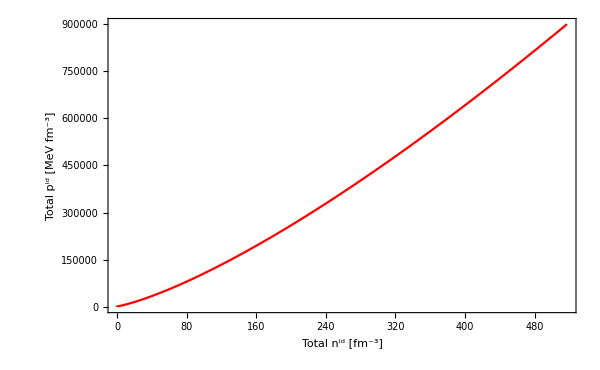

```mathematica
ListPlot[SortBy[Transpose@{npϵtotal[[2]],npϵtotal[[3]]},First],
Joined->True,
PlotStyle->Red,
PlotRange->Automatic,
FrameStyle->Directive[Black, Thick,25],
ImageSize->600,
Frame->True,
FrameLabel->{"Total n^id [fm^-3]","Total p^id [MeV fm^-3] "}]
```

#### Plot of P_total vs ϵ_total

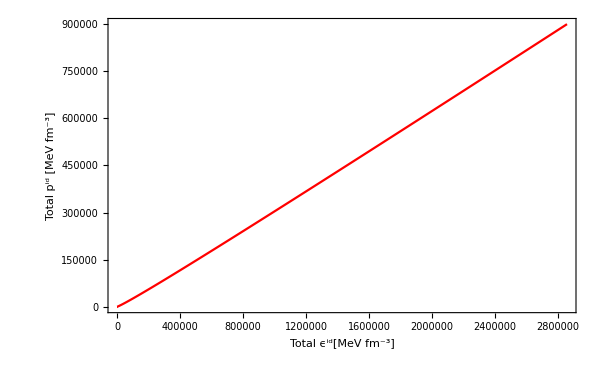

```mathematica
ListPlot[SortBy[Transpose@{npϵtotal[[4]],npϵtotal[[3]]},First],
Joined->True,
PlotStyle->Red,
PlotRange->Automatic,
FrameStyle->Directive[Black, Thick,25],
ImageSize->600,
Frame->True,
FrameLabel->{"Total ϵ^id[MeV fm^-3]","Total p^id [MeV fm^-3] "}]
```

#### Speed of sound

We want to plot the speed of sound  as a function of the total pressure, i.e taking the derivative of dpid_total/dϵid_total as a function of ϵid_total.

```mathematica
g1= Interpolation[SortBy[Transpose@{npϵtotal[[4]],npϵtotal[[3]]},First]]
```

Interpolation::inddp: The point 0. in dimension 1 is duplicated.

Plot of the speed of sound as a function chemical potential

```mathematica
ListPlot[SortBy[Transpose@{npϵtotal[[1]],g1'[npϵtotal[[4]]]},First],
Joined->True,
PlotStyle->Red,
PlotRange->{Automatic},
FrameStyle->Directive[Black, Thick,25],
ImageSize->600,
Frame->True,
FrameLabel->{"μ [MeV]","c_s^2"}]
```

Transpose::nmtx: The first two levels of {{0,1,2,3,4,5,6,7,8,9,«3991»},Interpolation[{{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},«3991»}]'[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«3991»}]} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,1.,2.,3.,4.,5.,6.,7.,8.,9.,«3991»},Interpolation[{{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},«3991»}]'[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«3991»}]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPlot::prng: Value of option PlotRange -> {Automatic} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: Transpose[{{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,«3991»},Interpolation[{{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},«3991»}]'[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«3991»}]}] is not a list of numbers or pairs of numbers.

Or as a function of pressure

```mathematica
ListPlot[SortBy[Transpose@{npϵtotal[[3]],g1'[npϵtotal[[4]]]},First],
Joined->True,
PlotStyle->Red,
PlotRange->{Automatic},
FrameStyle->Directive[Black, Thick,25],
ImageSize->600,
Frame->True,
FrameLabel->{"p [MeV fm^-3]","c_s^2"}]
```

Transpose::nmtx: The first two levels of {{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«3991»},Interpolation[{{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},«3991»}]'[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«3991»}]} cannot be transposed.

ListPlot::prng: Value of option PlotRange -> {Automatic} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: Transpose[{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«3991»},Interpolation[{{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},«3991»}]'[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«3991»}]}] is not a list of numbers or pairs of numbers.

Or as a function of energy density

```mathematica
ListPlot[SortBy[Transpose@{npϵtotal[[4]],g1'[npϵtotal[[4]]]},First],
Joined->True,
PlotStyle->Red,
FrameStyle->Directive[Black, Thick,25],
ImageSize->600,
Frame->True,
FrameLabel->{"ϵ [MeV fm^-3]","c_s^2"}]
```

Transpose::nmtx: The first two levels of {{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«3991»},Interpolation[{{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},«3991»}]'[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«3991»}]} cannot be transposed.

ListPlot::lpn: Transpose[{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«3991»},Interpolation[{{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},«3991»}]'[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«3991»}]}] is not a list of numbers or pairs of numbers.

## Van der Waals

1. Calculate table of pressure (ideal) vs mub for a wide range of muB=0-4000 with steps in 5 MeV
2. Calculate table of  nid (ideal) vs mub for a wide range of muB=0-4000 with steps in 5 MeV
3. Interpolate both
4. put interpolated function into the function below instead of nid total[μStar] and pid total[μStar]

Figure out github, talk to other group members

```mathematica
npϵtotal=Transpose@ArrayFlatten@Parallelize@Table[{μB,nid total[μB],pid total[μB],ϵid total[μB]},{μB,0,4000,1}]
Transpose@npϵtotal//TableForm;
```

```mathematica
ptotal interpolated= Interpolation[SortBy[Transpose@{npϵtotal[[1]],npϵtotal[[3]]},First]];
 ntotal interpolated= Interpolation[SortBy[Transpose@{npϵtotal[[1]],npϵtotal[[2]]},First]];
ϵtotal interpolated= Interpolation[SortBy[Transpose@{npϵtotal[[1]],npϵtotal[[4]]},First]];
p ideal total[μStar_]:= ptotal interpolated[μStar]
n ideal total[μStar_]:= ntotal interpolated[μStar]
ϵ ideal total[μStar_]:= ϵtotal interpolated[μStar]
```

```mathematica
p ideal total[940]
n ideal total[940]
ϵ ideal total[940]
```

1206.85

0.00202449

3778.53

```mathematica
a=329;
b=3.42;
```

```mathematica
p[μ_]:= Module[{p,aunits,bunits,f,n interpolated,μStar,μStarSolution},

aunits=a (hbarc)^-3;
bunits=b(hbarc)^-3;

f[μStar_]:=μ+2*aunits*(n ideal total[μStar])/(1+bunits * n ideal total[μStar])-aunits*bunits*((n ideal total[μStar])/(1+bunits *n ideal total[μStar]))^2;

μStarSolution=μStar/.FindRoot[μStar-f[μStar],{μStar,μ}];

p=p ideal total[μStarSolution]-aunits*((n ideal total[μStarSolution])/(1+bunits *n ideal total[μStarSolution]))^2;

Return[{μ,p ideal total[μ](hbarc)^-3,p (hbarc)^-3}];
]
(* Testing *)
```

```mathematica
p[920]
```

{920,0.000143773,0.000143773}

```mathematica
Table[p[μ],{μ,900,3900,100}]//TableForm
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

900 | 0.000131274 | 0.000131274
1000 | 0.000203949 | 0.000203949
1100 | 0.000313451 | 0.000313452
1200 | 0.000475595 | 0.000475595
1300 | 0.000705508 | 0.000705509
1400 | 0.00101899 | 0.001019
1500 | 0.0014328 | 0.00143281
1600 | 0.00196475 | 0.00196476
1700 | 0.00263375 | 0.00263376
1800 | 0.00345986 | 0.00345988
1900 | 0.00446429 | 0.00446432
2000 | 0.00566944 | 0.00566948
2100 | 0.00709886 | 0.00709892
2200 | 0.0087773 | 0.00877738
2300 | 0.0107307 | 0.0107308
2400 | 0.0129862 | 0.0129863
2500 | 0.015572 | 0.0155722
2600 | 0.0185178 | 0.0185181
2700 | 0.0218542 | 0.0218545
2800 | 0.0256131 | 0.0256135
2900 | 0.0298276 | 0.0298281
3000 | 0.0345321 | 0.0345327
3100 | 0.0397619 | 0.0397627
3200 | 0.0455539 | 0.0455548
3300 | 0.0519458 | 0.051947
3400 | 0.0589769 | 0.0589783
3500 | 0.0666874 | 0.0666891
3600 | 0.0751188 | 0.0751209
3700 | 0.0843138 | 0.0843162
3800 | 0.0943163 | 0.0943192
3900 | 0.105171 | 0.105175

```mathematica
n[μ_]:= Module[{n,aunits,bunits,f,n interpolated,μStar,μStarSolution},

aunits=a (hbarc)^-3;
bunits=b(hbarc)^-3;

f[μStar_]:=μ+2*aunits*(n ideal total[μStar])/(1+bunits * n ideal total[μStar])-aunits*bunits*((n ideal total[μStar])/(1+bunits *n ideal total[μStar]))^2;

μStarSolution=μStar/.FindRoot[μStar-f[μStar],{μStar,μ}];

n=(n ideal total[μStarSolution])/(1+bunits* n ideal total[μStarSolution]);

 Return[{μ,n ideal total[μ](hbarc)^-3,n (hbarc)^-3}];
]
(* Testing *)
```

```mathematica
n[2550]
```

{2550,0.0000152672,0.0000152666}

```mathematica
Table[n[μ],{μ,900,3900,100}]//TableForm
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

900 | 0. | 0.
1000 | 4.76941×10^-8 | 4.76941×10^-8
1100 | 2.17233×10^-7 | 2.17233×10^-7
1200 | 4.80076×10^-7 | 4.80076×10^-7
1300 | 8.35025×10^-7 | 8.35025×10^-7
1400 | 1.28551×10^-6 | 1.28551×10^-6
1500 | 1.83654×10^-6 | 1.83654×10^-6
1600 | 2.49385×10^-6 | 2.49384×10^-6
1700 | 3.26356×10^-6 | 3.26354×10^-6
1800 | 4.152×10^-6 | 4.15197×10^-6
1900 | 5.16568×10^-6 | 5.16563×10^-6
2000 | 6.31119×10^-6 | 6.3111×10^-6
2100 | 7.59517×10^-6 | 7.59504×10^-6
2200 | 9.02433×10^-6 | 9.02414×10^-6
2300 | 0.0000106054 | 0.0000106051
2400 | 0.0000123452 | 0.0000123448
2500 | 0.0000142504 | 0.0000142499
2600 | 0.0000163279 | 0.0000163272
2700 | 0.0000185844 | 0.0000185835
2800 | 0.0000210269 | 0.0000210257
2900 | 0.0000236621 | 0.0000236606
3000 | 0.0000264968 | 0.0000264949
3100 | 0.0000295379 | 0.0000295355
3200 | 0.0000327922 | 0.0000327893
3300 | 0.0000362667 | 0.000036263
3400 | 0.000039968 | 0.0000399636
3500 | 0.0000439032 | 0.0000438978
3600 | 0.000048079 | 0.0000480724
3700 | 0.0000525023 | 0.0000524944
3800 | 0.0000571799 | 0.0000571705
3900 | 0.0000621188 | 0.0000621076

```mathematica
ϵ[μ_]:= Module[{ϵ,aunits,bunits,f,n interpolated,μStar,μStarSolution},

aunits=a (hbarc)^-3;
bunits=b(hbarc)^-3;

f[μStar_]:=μ+2*aunits*(n ideal total[μStar])/(1+bunits * n ideal total[μStar])-aunits*bunits*((n ideal total[μStar])/(1+bunits *n ideal total[μStar]))^2;

μStarSolution=μStar/.FindRoot[μStar-f[μStar],{μStar,μ}];

ϵ = (ϵ ideal total[μStarSolution])/(1+bunits* n ideal total[μStarSolution])- aunits*( (n ideal total[μStarSolution])/(1+bunits* n ideal total[μStarSolution]))^2;

 Return[{μ,ϵ ideal total[μ](hbarc)^-3,ϵ (hbarc)^-3}];
]
(* Testing *)
```

```mathematica
ϵ[2200]
```

{2200,0.0310756,0.031075}

```mathematica
μϵtable=Table[ϵ[μ],{μ,900,3900,100}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{{900,0.00041235,0.00041235},{1000,0.000678036,0.000678036},{1100,0.0011532,0.0011532},{1200,0.00184598,0.00184598},{1300,0.00279138,0.00279137},{1400,0.0040318,0.00403179},{1500,0.00561448,0.00561447},{1600,0.00759084,0.00759081},{1700,0.0100162,0.0100161},{1800,0.0129496,0.0129495},{1900,0.016454,0.0164538},{2000,0.0205957,0.0205954},{2100,0.025445,0.0254446},{2200,0.0310756,0.031075},{2300,0.037565,0.0375641},{2400,0.0449943,0.044993},{2500,0.053448,0.0534462},{2600,0.0630146,0.0630121},{2700,0.0737859,0.0737825},{2800,0.0858575,0.085853},{2900,0.0993286,0.0993226},{3000,0.114302,0.114294},{3100,0.130884,0.130873},{3200,0.149184,0.149171},{3300,0.169316,0.1693},{3400,0.191398,0.191378},{3500,0.21555,0.215524},{3600,0.241897,0.241865},{3700,0.270566,0.270527},{3800,0.301689,0.301641},{3900,0.335402,0.335344}}

```mathematica
Transpose@μϵtable
```

{{900,1000,1100,1200,1300,1400,1500,1600,1700,1800,1900,2000,2100,2200,2300,2400,2500,2600,2700,2800,2900,3000,3100,3200,3300,3400,3500,3600,3700,3800,3900},{0.00041235,0.000678036,0.0011532,0.00184598,0.00279138,0.0040318,0.00561448,0.00759084,0.0100162,0.0129496,0.016454,0.0205957,0.025445,0.0310756,0.037565,0.0449943,0.053448,0.0630146,0.0737859,0.0858575,0.0993286,0.114302,0.130884,0.149184,0.169316,0.191398,0.21555,0.241897,0.270566,0.301689,0.335402},{0.00041235,0.000678036,0.0011532,0.00184598,0.00279137,0.00403179,0.00561447,0.00759081,0.0100161,0.0129495,0.0164538,0.0205954,0.0254446,0.031075,0.0375641,0.044993,0.0534462,0.0630121,0.0737825,0.085853,0.0993226,0.114294,0.130873,0.149171,0.1693,0.191378,0.215524,0.241865,0.270527,0.301641,0.335344}}

```mathematica
Transpose@{Transpose[μϵtable][[1]],Transpose[μϵtable][[3]],Transpose[μϵtable][[2]] }
```

{{900,0.00041235,0.00041235},{1000,0.000678036,0.000678036},{1100,0.0011532,0.0011532},{1200,0.00184598,0.00184598},{1300,0.00279137,0.00279138},{1400,0.00403179,0.0040318},{1500,0.00561447,0.00561448},{1600,0.00759081,0.00759084},{1700,0.0100161,0.0100162},{1800,0.0129495,0.0129496},{1900,0.0164538,0.016454},{2000,0.0205954,0.0205957},{2100,0.0254446,0.025445},{2200,0.031075,0.0310756},{2300,0.0375641,0.037565},{2400,0.044993,0.0449943},{2500,0.0534462,0.053448},{2600,0.0630121,0.0630146},{2700,0.0737825,0.0737859},{2800,0.085853,0.0858575},{2900,0.0993226,0.0993286},{3000,0.114294,0.114302},{3100,0.130873,0.130884},{3200,0.149171,0.149184},{3300,0.1693,0.169316},{3400,0.191378,0.191398},{3500,0.215524,0.21555},{3600,0.241865,0.241897},{3700,0.270527,0.270566},{3800,0.301641,0.301689},{3900,0.335344,0.335402}}

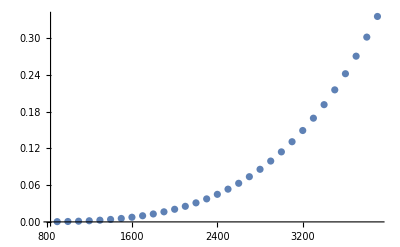

```mathematica
ListPlot[ Transpose@{Transpose[μϵtable][[1]],Transpose[μϵtable][[3]]}]
```

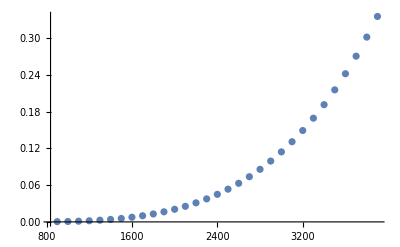

```mathematica
ListPlot[ Transpose@{Transpose[μϵtable][[1]],Transpose[μϵtable][[2]]}]
```